```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[12],Join[Table[{i,i-1},{i,Range[2,12,1]}],Table[{i,i+1},{i,Range[1,12,1]}]]->-t]
```

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[12]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[12]-A.T.J.T].A,132000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-g[ω,δ,t,ϵ].T[t].LEFT[ω,δ,t,ϵ].T[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-g[ω,δ,t,ϵ].T[t].LEFT[ω,δ,t,ϵ].T[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-SL[ω,δ,t,ϵ].T[t].SR[ω,δ,t,ϵ].T[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[12]-SR[ω,δ,t,ϵ].T[t].SL[ω,δ,t,ϵ].T[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T[t].grr[ω,δ,t,ϵ].T[t]-T[t].GNON[ω,δ,t,ϵ].T[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]]
```

$Aborted

```mathematica
F[i_]:=ListLinePlot[Table[{ω,-Im[IL[ω,0.001,1,0][[i,i]]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
deltae[ω_,ϵ1_]:=Module[{Tin=T[1],T1=T[1],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}],μ8=RandomInteger[{1,12}], μ9=RandomInteger[{1,12}], μ10=RandomInteger[{1,12}], μ11=RandomInteger[{1,12}],μ12=RandomInteger[{1,12}], μ13=RandomInteger[{1,12}], μ14=RandomInteger[{1,12}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];tra:= Module[{},list={RandomSample[{imp,imp,imp,imp1,imp3,imp5,imp14,imp,imp,imp,imp2,imp,imp5,imp,imp4,imp,imp12,imp1,imp,imp,imp8,imp,imp,imp8,imp3,imp,imp,imp,imp,imp,imp4,imp,imp11,imp3,imp,imp,imp,imp,imp,imp13,imp7,imp,imp4,imp7,imp9,imp,imp2,imp14,imp5,imp,imp,imp,imp,imp13,imp6,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp14,imp,imp,imp,imp11,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp13,imp9,imp10,imp2,imp10,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp9}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[12]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[12]-sl1.T1.SR[ω,0.0001,1,0].T1].sl1;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.0001,1,0].T1.sl1.T1].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b];
tra]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp1.dat",%39]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp1.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.1],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000160671},{-3.99,0.0000243125},{-3.98,0.0000402465},{-3.97,0.0000757466},{-3.96,0.000180842},{-3.95,0.000625225},{-3.94,0.0652007},{-3.93,0.93039},{-3.92,0.962252},{-3.91,0.975934},{-3.9,0.982605},{-3.89,0.986897},{-3.88,0.988733},{-3.87,0.989986},{-3.86,0.991525},{-3.85,0.992173},{-3.84,0.993145},{-3.83,0.99356},{-3.82,0.994181},{-3.81,0.99449},{-3.8,0.994767},{-3.79,0.994784},{-3.78,0.994095},{-3.77,0.998919},{-3.76,1.86324},{-3.75,1.92935},{-3.74,1.95176},{-3.73,1.96225},{-3.72,1.96987},{-3.71,1.97322},{-3.7,1.97607},{-3.69,1.9788},{-3.68,1.98051},{-3.67,1.98212},{-3.66,1.98346},{-3.65,1.98446},{-3.64,1.98548},{-3.63,1.98622},{-3.62,1.9869},{-3.61,1.98773},{-3.6,1.98818},{-3.59,1.98854},{-3.58,1.98916},{-3.57,1.98942},{-3.56,1.98978},{-3.55,1.99007},{-3.54,1.99039},{-3.53,1.99046},{-3.52,1.99045},{-3.51,1.98972},{-3.5,1.98333},{-3.49,2.69478},{-3.48,2.88313},{-3.47,2.92443},{-3.46,2.9422},{-3.45,2.95117},{-3.44,2.9576},{-3.43,2.96306},{-3.42,2.96592},{-3.41,2.96909},{-3.4,2.97119},{-3.39,2.97329},{-3.38,2.97462},{-3.37,2.97597},{-3.36,2.97722},{-3.35,2.97811},{-3.34,2.97903},{-3.33,2.9798},{-3.32,2.98065},{-3.31,2.98129},{-3.3,2.98185},{-3.29,2.98234},{-3.28,2.98311},{-3.27,2.98358},{-3.26,2.98388},{-3.25,2.98429},{-3.24,2.98478},{-3.23,2.98501},{-3.22,2.9855},{-3.21,2.98588},{-3.2,2.98594},{-3.19,2.98615},{-3.18,2.98628},{-3.17,2.98626},{-3.16,2.98615},{-3.15,2.98497},{-3.14,2.977},{-3.13,3.52197},{-3.12,3.83776},{-3.11,3.89889},{-3.1,3.92132},{-3.09,3.93452},{-3.08,3.94282},{-3.07,3.94964},{-3.06,3.95384},{-3.05,3.9576},{-3.04,3.96053},{-3.03,3.96308},{-3.02,3.96501},{-3.01,3.9668},{-3.,3.96813},{-2.99,3.96941},{-2.98,3.97039},{-2.97,3.97169},{-2.96,3.97259},{-2.95,3.97342},{-2.94,3.97427},{-2.93,3.97497},{-2.92,3.97565},{-2.91,3.97604},{-2.9,3.97668},{-2.89,3.97719},{-2.88,3.9778},{-2.87,3.97811},{-2.86,3.97856},{-2.85,3.97897},{-2.84,3.97925},{-2.83,3.97964},{-2.82,3.98009},{-2.81,3.98033},{-2.8,3.98068},{-2.79,3.98096},{-2.78,3.98122},{-2.77,3.98133},{-2.76,3.98164},{-2.75,3.98146},{-2.74,3.98125},{-2.73,3.98064},{-2.72,3.97802},{-2.71,3.93828},{-2.7,4.632},{-2.69,4.83192},{-2.68,4.88133},{-2.67,4.90657},{-2.66,4.92067},{-2.65,4.92973},{-2.64,4.93677},{-2.63,4.94215},{-2.62,4.94604},{-2.61,4.94981},{-2.6,4.95245},{-2.59,4.9549},{-2.58,4.95677},{-2.57,4.95861},{-2.56,4.95994},{-2.55,4.96152},{-2.54,4.96268},{-2.53,4.96375},{-2.52,4.96477},{-2.51,4.96569},{-2.5,4.96641},{-2.49,4.96727},{-2.48,4.96801},{-2.47,4.96859},{-2.46,4.96925},{-2.45,4.96978},{-2.44,4.97062},{-2.43,4.97103},{-2.42,4.97148},{-2.41,4.97195},{-2.4,4.97235},{-2.39,4.97272},{-2.38,4.97307},{-2.37,4.97341},{-2.36,4.97392},{-2.35,4.97417},{-2.34,4.97433},{-2.33,4.97464},{-2.32,4.97491},{-2.31,4.97505},{-2.3,4.97532},{-2.29,4.97536},{-2.28,4.97508},{-2.27,4.97488},{-2.26,4.97355},{-2.25,4.96849},{-2.24,4.83452},{-2.23,5.63975},{-2.22,5.80266},{-2.21,5.85651},{-2.2,5.88409},{-2.19,5.90141},{-2.18,5.91291},{-2.17,5.92107},{-2.16,5.92728},{-2.15,5.93252},{-2.14,5.93622},{-2.13,5.93924},{-2.12,5.94213},{-2.11,5.94452},{-2.1,5.94662},{-2.09,5.94875},{-2.08,5.95042},{-2.07,5.95165},{-2.06,5.95307},{-2.05,5.95426},{-2.04,5.95513},{-2.03,5.95634},{-2.02,5.95733},{-2.01,5.95813},{-2.,5.95898},{-1.99,5.95968},{-1.98,5.96027},{-1.97,5.96097},{-1.96,5.96153},{-1.95,5.9621},{-1.94,5.96278},{-1.93,5.96317},{-1.92,5.96354},{-1.91,5.964},{-1.9,5.96454},{-1.89,5.96476},{-1.88,5.96511},{-1.87,5.96539},{-1.86,5.96591},{-1.85,5.96607},{-1.84,5.96646},{-1.83,5.96677},{-1.82,5.96678},{-1.81,5.96688},{-1.8,5.96684},{-1.79,5.96625},{-1.78,5.96494},{-1.77,5.95966},{-1.76,5.88693},{-1.75,6.39515},{-1.74,6.71127},{-1.73,6.79734},{-1.72,6.83922},{-1.71,6.86382},{-1.7,6.87927},{-1.69,6.89121},{-1.68,6.90008},{-1.67,6.90612},{-1.66,6.91181},{-1.65,6.91674},{-1.64,6.92082},{-1.63,6.92381},{-1.62,6.92662},{-1.61,6.92917},{-1.6,6.93124},{-1.59,6.93325},{-1.58,6.93508},{-1.57,6.93674},{-1.56,6.93799},{-1.55,6.93937},{-1.54,6.94072},{-1.53,6.94176},{-1.52,6.94287},{-1.51,6.9439},{-1.5,6.94435},{-1.49,6.94537},{-1.48,6.94625},{-1.47,6.94714},{-1.46,6.94783},{-1.45,6.94854},{-1.44,6.94879},{-1.43,6.94949},{-1.42,6.94996},{-1.41,6.95058},{-1.4,6.95079},{-1.39,6.95141},{-1.38,6.95188},{-1.37,6.9523},{-1.36,6.95248},{-1.35,6.95244},{-1.34,6.95254},{-1.33,6.95214},{-1.32,6.95115},{-1.31,6.94902},{-1.3,6.93891},{-1.29,6.67219},{-1.28,7.35883},{-1.27,7.65381},{-1.26,7.74874},{-1.25,7.79766},{-1.24,7.82627},{-1.23,7.84433},{-1.22,7.85822},{-1.21,7.86923},{-1.2,7.87703},{-1.19,7.88466},{-1.18,7.88975},{-1.17,7.89508},{-1.16,7.89928},{-1.15,7.90183},{-1.14,7.90536},{-1.13,7.90817},{-1.12,7.91064},{-1.11,7.91297},{-1.1,7.91444},{-1.09,7.91625},{-1.08,7.9179},{-1.07,7.91927},{-1.06,7.92023},{-1.05,7.92197},{-1.04,7.92286},{-1.03,7.9242},{-1.02,7.92467},{-1.01,7.92554},{-1.,7.92672},{-0.99,7.92764},{-0.98,7.92835},{-0.97,7.92875},{-0.96,7.92945},{-0.95,7.92976},{-0.94,7.93036},{-0.93,7.93045},{-0.92,7.93082},{-0.91,7.93065},{-0.9,7.93019},{-0.89,7.92869},{-0.88,7.92349},{-0.87,7.89767},{-0.86,6.62482},{-0.85,8.34164},{-0.84,8.58605},{-0.83,8.68628},{-0.82,8.73773},{-0.81,8.77308},{-0.8,8.79393},{-0.79,8.81174},{-0.78,8.82371},{-0.77,8.83529},{-0.76,8.84287},{-0.75,8.84999},{-0.74,8.85543},{-0.73,8.86016},{-0.72,8.86451},{-0.71,8.86837},{-0.7,8.87172},{-0.69,8.87437},{-0.68,8.8779},{-0.67,8.87962},{-0.66,8.88166},{-0.65,8.88346},{-0.64,8.88501},{-0.63,8.88645},{-0.62,8.88772},{-0.61,8.88933},{-0.6,8.88943},{-0.59,8.89135},{-0.58,8.89131},{-0.57,8.89207},{-0.56,8.89277},{-0.55,8.89232},{-0.54,8.89181},{-0.53,8.88967},{-0.52,8.88336},{-0.51,8.85272},{-0.5,7.20829},{-0.49,9.02274},{-0.48,9.40265},{-0.47,9.54716},{-0.46,9.62216},{-0.45,9.66908},{-0.44,9.70039},{-0.43,9.72351},{-0.42,9.74146},{-0.41,9.75507},{-0.4,9.76665},{-0.39,9.77469},{-0.38,9.78319},{-0.37,9.78895},{-0.36,9.79433},{-0.35,9.79954},{-0.34,9.80357},{-0.33,9.80625},{-0.32,9.8091},{-0.31,9.81128},{-0.3,9.8117},{-0.29,9.81464},{-0.28,9.81484},{-0.27,9.81418},{-0.26,9.81271},{-0.25,9.80623},{-0.24,9.78183},{-0.23,9.42725},{-0.22,8.93312},{-0.21,9.92707},{-0.2,10.2209},{-0.19,10.3576},{-0.18,10.436},{-0.17,10.491},{-0.16,10.5285},{-0.15,10.5532},{-0.14,10.5711},{-0.13,10.5896},{-0.12,10.5985},{-0.11,10.6034},{-0.1,10.6072},{-0.09,10.6046},{-0.08,10.5931},{-0.07,10.5556},{-0.06,10.1203},{-0.05,7.8409},{-0.04,9.81024},{-0.03,10.346},{-0.02,10.5786},{-0.01,10.6861},{0.,10.7403},{0.01,10.7202},{0.02,10.6319},{0.03,10.449},{0.04,10.0778},{0.05,8.82655},{0.06,6.89301},{0.07,10.3922},{0.08,10.5286},{0.09,10.5609},{0.1,10.5717},{0.11,10.5732},{0.12,10.5714},{0.13,10.5674},{0.14,10.5562},{0.15,10.5359},{0.16,10.5146},{0.17,10.4817},{0.18,10.4331},{0.19,10.3658},{0.2,10.2534},{0.21,10.0186},{0.22,9.42275},{0.23,4.45511},{0.24,9.67783},{0.25,9.76582},{0.26,9.78438},{0.27,9.79075},{0.28,9.79433},{0.29,9.79587},{0.3,9.79596},{0.31,9.7949},{0.32,9.79366},{0.33,9.79234},{0.34,9.7889},{0.35,9.78599},{0.36,9.782},{0.37,9.77763},{0.38,9.77089},{0.39,9.76347},{0.4,9.75458},{0.41,9.74528},{0.42,9.73123},{0.43,9.71414},{0.44,9.69455},{0.45,9.66576},{0.46,9.62244},{0.47,9.55601},{0.48,9.44237},{0.49,9.1769},{0.5,7.86368},{0.51,8.66095},{0.52,8.8511},{0.53,8.86998},{0.54,8.87595},{0.55,8.87879},{0.56,8.87984},{0.57,8.8803},{0.58,8.8803},{0.59,8.88079},{0.6,8.87943},{0.61,8.87928},{0.62,8.87824},{0.63,8.87687},{0.64,8.87588},{0.65,8.87372},{0.66,8.87245},{0.67,8.87116},{0.68,8.86855},{0.69,8.86576},{0.7,8.86337},{0.71,8.86045},{0.72,8.85695},{0.73,8.853},{0.74,8.84807},{0.75,8.84297},{0.76,8.83526},{0.77,8.82779},{0.78,8.81659},{0.79,8.80521},{0.8,8.78969},{0.81,8.76856},{0.82,8.73928},{0.83,8.69339},{0.84,8.61282},{0.85,8.43665},{0.86,7.6616},{0.87,7.6867},{0.88,7.8999},{0.89,7.91456},{0.9,7.91917},{0.91,7.92071},{0.92,7.92189},{0.93,7.92229},{0.94,7.92227},{0.95,7.9223},{0.96,7.92198},{0.97,7.92142},{0.98,7.92099},{0.99,7.92092},{1.,7.92001},{1.01,7.91915},{1.02,7.91886},{1.03,7.91756},{1.04,7.91697},{1.05,7.91558},{1.06,7.91377},{1.07,7.91313},{1.08,7.91193},{1.09,7.90995},{1.1,7.90835},{1.11,7.90641},{1.12,7.90409},{1.13,7.90246},{1.14,7.89967},{1.15,7.89617},{1.16,7.89232},{1.17,7.88887},{1.18,7.88487},{1.19,7.87941},{1.2,7.8724},{1.21,7.86362},{1.22,7.85409},{1.23,7.84131},{1.24,7.82312},{1.25,7.79766},{1.26,7.75664},{1.27,7.6836},{1.28,7.4958},{1.29,5.54336},{1.3,6.8924},{1.31,6.93507},{1.32,6.94209},{1.33,6.9445},{1.34,6.94576},{1.35,6.9461},{1.36,6.9463},{1.37,6.94626},{1.38,6.94604},{1.39,6.94583},{1.4,6.94561},{1.41,6.94522},{1.42,6.94481},{1.43,6.94451},{1.44,6.94405},{1.45,6.94359},{1.46,6.94301},{1.47,6.94236},{1.48,6.94148},{1.49,6.94088},{1.5,6.93994},{1.51,6.9391},{1.52,6.93837},{1.53,6.9374},{1.54,6.93626},{1.55,6.93534},{1.56,6.93351},{1.57,6.93212},{1.58,6.93039},{1.59,6.92873},{1.6,6.92679},{1.61,6.92438},{1.62,6.92203},{1.63,6.91936},{1.64,6.91649},{1.65,6.91221},{1.66,6.90806},{1.67,6.90254},{1.68,6.8962},{1.69,6.88724},{1.7,6.87624},{1.71,6.86079},{1.72,6.84053},{1.73,6.80407},{1.74,6.73794},{1.75,6.54772},{1.76,3.32129},{1.77,5.93588},{1.78,5.95541},{1.79,5.95936},{1.8,5.96083},{1.81,5.96162},{1.82,5.96191},{1.83,5.9618},{1.84,5.96168},{1.85,5.96174},{1.86,5.96138},{1.87,5.96154},{1.88,5.96106},{1.89,5.96089},{1.9,5.96054},{1.91,5.95999},{1.92,5.95962},{1.93,5.95924},{1.94,5.95863},{1.95,5.95818},{1.96,5.95769},{1.97,5.95691},{1.98,5.9566},{1.99,5.95567},{2.,5.95514},{2.01,5.95411},{2.02,5.95366},{2.03,5.95235},{2.04,5.95114},{2.05,5.95027},{2.06,5.94903},{2.07,5.94783},{2.08,5.94647},{2.09,5.94443},{2.1,5.94267},{2.11,5.94051},{2.12,5.9383},{2.13,5.9356},{2.14,5.93192},{2.15,5.92838},{2.16,5.92291},{2.17,5.91704},{2.18,5.90955},{2.19,5.89864},{2.2,5.88303},{2.21,5.86149},{2.22,5.82032},{2.23,5.7134},{2.24,4.75842},{2.25,4.94278},{2.26,4.96663},{2.27,4.97011},{2.28,4.97132},{2.29,4.97168},{2.3,4.97179},{2.31,4.97192},{2.32,4.97181},{2.33,4.97167},{2.34,4.97133},{2.35,4.97124},{2.36,4.97082},{2.37,4.97056},{2.38,4.9702},{2.39,4.96996},{2.4,4.96956},{2.41,4.96914},{2.42,4.9687},{2.43,4.96839},{2.44,4.96778},{2.45,4.96717},{2.46,4.96668},{2.47,4.96576},{2.48,4.96526},{2.49,4.96455},{2.5,4.964},{2.51,4.96298},{2.52,4.96179},{2.53,4.96089},{2.54,4.95967},{2.55,4.95851},{2.56,4.9572},{2.57,4.95563},{2.58,4.95399},{2.59,4.95192},{2.6,4.94986},{2.61,4.94691},{2.62,4.94338},{2.63,4.93922},{2.64,4.93363},{2.65,4.92844},{2.66,4.91846},{2.67,4.90538},{2.68,4.88525},{2.69,4.84676},{2.7,4.735},{2.71,2.97482},{2.72,3.96587},{2.73,3.97595},{2.74,3.97801},{2.75,3.97854},{2.76,3.97875},{2.77,3.97889},{2.78,3.97864},{2.79,3.97849},{2.8,3.97829},{2.81,3.97812},{2.82,3.9778},{2.83,3.97744},{2.84,3.97709},{2.85,3.97682},{2.86,3.97642},{2.87,3.97584},{2.88,3.97537},{2.89,3.9751},{2.9,3.97438},{2.91,3.97394},{2.92,3.97338},{2.93,3.97258},{2.94,3.97209},{2.95,3.97115},{2.96,3.97017},{2.97,3.96945},{2.98,3.96838},{2.99,3.96707},{3.,3.96575},{3.01,3.96414},{3.02,3.96263},{3.03,3.96038},{3.04,3.95871},{3.05,3.95535},{3.06,3.95152},{3.07,3.94747},{3.08,3.94159},{3.09,3.93466},{3.1,3.92163},{3.11,3.90198},{3.12,3.85946},{3.13,3.74327},{3.14,2.46669},{3.15,2.97914},{3.16,2.98283},{3.17,2.98393},{3.18,2.98402},{3.19,2.98406},{3.2,2.98392},{3.21,2.98371},{3.22,2.9834},{3.23,2.98311},{3.24,2.98306},{3.25,2.98251},{3.26,2.98215},{3.27,2.98161},{3.28,2.98133},{3.29,2.98056},{3.3,2.98006},{3.31,2.97958},{3.32,2.97878},{3.33,2.97801},{3.34,2.97723},{3.35,2.97627},{3.36,2.97548},{3.37,2.97395},{3.38,2.97274},{3.39,2.97098},{3.4,2.96951},{3.41,2.96672},{3.42,2.96437},{3.43,2.96019},{3.44,2.95595},{3.45,2.95119},{3.46,2.94116},{3.47,2.92605},{3.48,2.89564},{3.49,2.81333},{3.5,1.51583},{3.51,1.9853},{3.52,1.98806},{3.53,1.98873},{3.54,1.98865},{3.55,1.98857},{3.56,1.98845},{3.57,1.9878},{3.58,1.98768},{3.59,1.98716},{3.6,1.98668},{3.61,1.98622},{3.62,1.98548},{3.63,1.98471},{3.64,1.98388},{3.65,1.98311},{3.66,1.98204},{3.67,1.98043},{3.68,1.97915},{3.69,1.97734},{3.7,1.97473},{3.71,1.97231},{3.72,1.96794},{3.73,1.96151},{3.74,1.95461},{3.75,1.94098},{3.76,1.89929},{3.77,1.58397},{3.78,0.989943},{3.79,0.993246},{3.8,0.993753},{3.81,0.99347},{3.82,0.993196},{3.83,0.992916},{3.84,0.992183},{3.85,0.991603},{3.86,0.990577},{3.87,0.989297},{3.88,0.988367},{3.89,0.985235},{3.9,0.982858},{3.91,0.979629},{3.92,0.972076},{3.93,0.952122},{3.94,0.789912},{3.95,0.00103374},{3.96,0.000205233},{3.97,0.0000817364},{3.98,0.0000432486},{3.99,0.0000258978},{4.,0.000017235}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp2.dat",%40]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp2.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.2],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.000020537},{-3.99,0.000032155},{-3.98,0.0000539407},{-3.97,0.000105841},{-3.96,0.000256789},{-3.95,0.00116336},{-3.94,0.0197424},{-3.93,0.674634},{-3.92,0.86213},{-3.91,0.911648},{-3.9,0.936051},{-3.89,0.949275},{-3.88,0.955493},{-3.87,0.962979},{-3.86,0.967779},{-3.85,0.97073},{-3.84,0.974584},{-3.83,0.976236},{-3.82,0.978567},{-3.81,0.979114},{-3.8,0.980432},{-3.79,0.980732},{-3.78,0.979022},{-3.77,0.955856},{-3.76,1.4616},{-3.75,1.7324},{-3.74,1.82321},{-3.73,1.86078},{-3.72,1.88333},{-3.71,1.89726},{-3.7,1.91075},{-3.69,1.9201},{-3.68,1.92745},{-3.67,1.93362},{-3.66,1.93747},{-3.65,1.94147},{-3.64,1.94497},{-3.63,1.94845},{-3.62,1.95068},{-3.61,1.95298},{-3.6,1.9555},{-3.59,1.95721},{-3.58,1.95913},{-3.57,1.96077},{-3.56,1.9619},{-3.55,1.96316},{-3.54,1.96401},{-3.53,1.96465},{-3.52,1.96481},{-3.51,1.96309},{-3.5,1.94737},{-3.49,1.95274},{-3.48,2.55227},{-3.47,2.70544},{-3.46,2.77337},{-3.45,2.81526},{-3.44,2.84304},{-3.43,2.85995},{-3.42,2.87271},{-3.41,2.88422},{-3.4,2.89046},{-3.39,2.89908},{-3.38,2.90369},{-3.37,2.91025},{-3.36,2.91387},{-3.35,2.91859},{-3.34,2.92152},{-3.33,2.92456},{-3.32,2.92707},{-3.31,2.92925},{-3.3,2.93243},{-3.29,2.93427},{-3.28,2.93668},{-3.27,2.93828},{-3.26,2.93929},{-3.25,2.94106},{-3.24,2.94281},{-3.23,2.94419},{-3.22,2.94548},{-3.21,2.94675},{-3.2,2.9479},{-3.19,2.94848},{-3.18,2.94914},{-3.17,2.94928},{-3.16,2.94907},{-3.15,2.94624},{-3.14,2.92697},{-3.13,2.71065},{-3.12,3.39684},{-3.11,3.6093},{-3.1,3.70166},{-3.09,3.75389},{-3.08,3.78742},{-3.07,3.81058},{-3.06,3.82636},{-3.05,3.84066},{-3.04,3.85162},{-3.03,3.86016},{-3.02,3.86721},{-3.01,3.87463},{-3.,3.87921},{-2.99,3.88573},{-2.98,3.88931},{-2.97,3.89328},{-2.96,3.8964},{-2.95,3.90003},{-2.94,3.90302},{-2.93,3.90524},{-2.92,3.90827},{-2.91,3.91018},{-2.9,3.91267},{-2.89,3.91495},{-2.88,3.91577},{-2.87,3.91762},{-2.86,3.9199},{-2.85,3.92208},{-2.84,3.92203},{-2.83,3.92406},{-2.82,3.92548},{-2.81,3.92644},{-2.8,3.92748},{-2.79,3.92896},{-2.78,3.92957},{-2.77,3.93015},{-2.76,3.93147},{-2.75,3.93162},{-2.74,3.93153},{-2.73,3.92944},{-2.72,3.92215},{-2.71,3.84418},{-2.7,3.7022},{-2.69,4.35301},{-2.68,4.55196},{-2.67,4.64579},{-2.66,4.69777},{-2.65,4.73772},{-2.64,4.76431},{-2.63,4.78256},{-2.62,4.79892},{-2.61,4.81044},{-2.6,4.82072},{-2.59,4.82933},{-2.58,4.83789},{-2.57,4.84336},{-2.56,4.85022},{-2.55,4.85488},{-2.54,4.85948},{-2.53,4.86372},{-2.52,4.86647},{-2.51,4.87048},{-2.5,4.87442},{-2.49,4.87709},{-2.48,4.88012},{-2.47,4.88134},{-2.46,4.88469},{-2.45,4.88641},{-2.44,4.88853},{-2.43,4.89112},{-2.42,4.89327},{-2.41,4.89443},{-2.4,4.89606},{-2.39,4.89803},{-2.38,4.89888},{-2.37,4.90068},{-2.36,4.9017},{-2.35,4.90372},{-2.34,4.90403},{-2.33,4.90512},{-2.32,4.90591},{-2.31,4.9072},{-2.3,4.90783},{-2.29,4.90829},{-2.28,4.90857},{-2.27,4.90664},{-2.26,4.9039},{-2.25,4.89061},{-2.24,4.6841},{-2.23,4.64227},{-2.22,5.2624},{-2.21,5.46932},{-2.2,5.57503},{-2.19,5.63182},{-2.18,5.67221},{-2.17,5.70469},{-2.16,5.72558},{-2.15,5.74448},{-2.14,5.75971},{-2.13,5.77224},{-2.12,5.78268},{-2.11,5.79142},{-2.1,5.80043},{-2.09,5.8067},{-2.08,5.81248},{-2.07,5.81885},{-2.06,5.82281},{-2.05,5.82728},{-2.04,5.83222},{-2.03,5.8353},{-2.02,5.83948},{-2.01,5.84259},{-2.,5.8451},{-1.99,5.84818},{-1.98,5.85152},{-1.97,5.85324},{-1.96,5.85528},{-1.95,5.85898},{-1.94,5.86015},{-1.93,5.86217},{-1.92,5.86361},{-1.91,5.86469},{-1.9,5.86696},{-1.89,5.86877},{-1.88,5.87053},{-1.87,5.87155},{-1.86,5.87273},{-1.85,5.87415},{-1.84,5.87552},{-1.83,5.87556},{-1.82,5.87725},{-1.81,5.87757},{-1.8,5.87762},{-1.79,5.87645},{-1.78,5.8724},{-1.77,5.85932},{-1.76,5.71909},{-1.75,4.98077},{-1.74,5.93734},{-1.73,6.25142},{-1.72,6.4002},{-1.71,6.48912},{-1.7,6.54927},{-1.69,6.59363},{-1.68,6.6251},{-1.67,6.65159},{-1.66,6.66951},{-1.65,6.68684},{-1.64,6.70082},{-1.63,6.71528},{-1.62,6.72557},{-1.61,6.7347},{-1.6,6.74221},{-1.59,6.74897},{-1.58,6.75549},{-1.57,6.76169},{-1.56,6.76764},{-1.55,6.77182},{-1.54,6.77854},{-1.53,6.78135},{-1.52,6.78536},{-1.51,6.78926},{-1.5,6.79292},{-1.49,6.79567},{-1.48,6.79844},{-1.47,6.80089},{-1.46,6.8037},{-1.45,6.80633},{-1.44,6.80996},{-1.43,6.81109},{-1.42,6.81376},{-1.41,6.81435},{-1.4,6.81632},{-1.39,6.81876},{-1.38,6.82025},{-1.37,6.82142},{-1.36,6.82246},{-1.35,6.82337},{-1.34,6.82337},{-1.33,6.82366},{-1.32,6.82206},{-1.31,6.81452},{-1.3,6.79008},{-1.29,6.39667},{-1.28,5.78623},{-1.27,6.73629},{-1.26,7.08286},{-1.25,7.24886},{-1.24,7.35003},{-1.23,7.4201},{-1.22,7.47524},{-1.21,7.51096},{-1.2,7.5417},{-1.19,7.56873},{-1.18,7.59025},{-1.17,7.60704},{-1.16,7.62076},{-1.15,7.635},{-1.14,7.64527},{-1.13,7.65509},{-1.12,7.66441},{-1.11,7.67163},{-1.1,7.68077},{-1.09,7.68613},{-1.08,7.69268},{-1.07,7.69773},{-1.06,7.70314},{-1.05,7.70715},{-1.04,7.71135},{-1.03,7.71541},{-1.02,7.71806},{-1.01,7.72282},{-1.,7.72652},{-0.99,7.72939},{-0.98,7.73119},{-0.97,7.73335},{-0.96,7.73749},{-0.95,7.73896},{-0.94,7.73945},{-0.93,7.74183},{-0.92,7.74399},{-0.91,7.74419},{-0.9,7.74347},{-0.89,7.73839},{-0.88,7.72553},{-0.87,7.66098},{-0.86,6.61065},{-0.85,6.69561},{-0.84,7.51913},{-0.83,7.85823},{-0.82,8.04477},{-0.81,8.16473},{-0.8,8.2436},{-0.79,8.30266},{-0.78,8.35067},{-0.77,8.38838},{-0.76,8.41551},{-0.75,8.44204},{-0.74,8.46513},{-0.73,8.47963},{-0.72,8.49348},{-0.71,8.50955},{-0.7,8.5221},{-0.69,8.53226},{-0.68,8.54353},{-0.67,8.5507},{-0.66,8.55846},{-0.65,8.56424},{-0.64,8.57062},{-0.63,8.57872},{-0.62,8.58326},{-0.61,8.58823},{-0.6,8.59141},{-0.59,8.5968},{-0.58,8.5988},{-0.57,8.60244},{-0.56,8.60212},{-0.55,8.60391},{-0.54,8.60223},{-0.53,8.59654},{-0.52,8.58049},{-0.51,8.50241},{-0.5,7.26741},{-0.49,6.73475},{-0.48,7.9062},{-0.47,8.38143},{-0.46,8.63337},{-0.45,8.79762},{-0.44,8.90725},{-0.43,8.98937},{-0.42,9.05467},{-0.41,9.09966},{-0.4,9.13972},{-0.39,9.17126},{-0.38,9.20084},{-0.37,9.22169},{-0.36,9.24515},{-0.35,9.25995},{-0.34,9.27287},{-0.33,9.28885},{-0.32,9.29796},{-0.31,9.30488},{-0.3,9.3103},{-0.29,9.31892},{-0.28,9.32153},{-0.27,9.32046},{-0.26,9.31688},{-0.25,9.30305},{-0.24,9.23775},{-0.23,8.57015},{-0.22,5.20406},{-0.21,7.40536},{-0.2,8.29566},{-0.19,8.75786},{-0.18,9.01303},{-0.17,9.1923},{-0.16,9.30896},{-0.15,9.39727},{-0.14,9.47054},{-0.13,9.51785},{-0.12,9.55421},{-0.11,9.57881},{-0.1,9.58946},{-0.09,9.59322},{-0.08,9.56407},{-0.07,9.45089},{-0.06,8.54019},{-0.05,3.96232},{-0.04,5.49655},{-0.03,6.72449},{-0.02,7.32822},{-0.01,7.66983},{0.,7.85262},{0.01,7.96701},{0.02,7.61225},{0.03,7.14424},{0.04,6.27965},{0.05,4.50922},{0.06,8.12054},{0.07,7.58943},{0.08,9.03488},{0.09,9.27924},{0.1,9.34738},{0.11,9.37686},{0.12,9.38743},{0.13,9.36725},{0.14,9.33428},{0.15,9.29571},{0.16,9.22677},{0.17,9.12763},{0.18,8.9862},{0.19,8.77532},{0.2,8.4601},{0.21,7.81672},{0.22,6.32592},{0.23,5.87249},{0.24,7.61107},{0.25,8.96267},{0.26,9.09804},{0.27,9.14802},{0.28,9.17146},{0.29,9.17782},{0.3,9.18742},{0.31,9.18856},{0.32,9.18823},{0.33,9.18054},{0.34,9.17142},{0.35,9.16119},{0.36,9.14857},{0.37,9.13754},{0.38,9.11463},{0.39,9.0921},{0.4,9.05989},{0.41,9.02699},{0.42,8.98308},{0.43,8.92604},{0.44,8.8567},{0.45,8.76112},{0.46,8.63068},{0.47,8.42799},{0.48,8.09465},{0.49,7.38516},{0.5,4.38661},{0.51,5.21728},{0.52,8.26656},{0.53,8.4348},{0.54,8.47942},{0.55,8.49682},{0.56,8.50599},{0.57,8.51287},{0.58,8.51484},{0.59,8.51371},{0.6,8.51259},{0.61,8.51329},{0.62,8.51113},{0.63,8.50846},{0.64,8.50356},{0.65,8.50012},{0.66,8.49392},{0.67,8.4853},{0.68,8.48017},{0.69,8.46884},{0.7,8.46186},{0.71,8.45051},{0.72,8.43791},{0.73,8.4232},{0.74,8.40496},{0.75,8.3872},{0.76,8.36198},{0.77,8.33481},{0.78,8.30135},{0.79,8.25886},{0.8,8.20392},{0.81,8.1346},{0.82,8.03424},{0.83,7.89498},{0.84,7.65176},{0.85,7.16433},{0.86,5.37326},{0.87,4.47749},{0.88,7.48271},{0.89,7.62244},{0.9,7.65432},{0.91,7.66769},{0.92,7.67514},{0.93,7.67783},{0.94,7.67979},{0.95,7.67977},{0.96,7.68147},{0.97,7.67874},{0.98,7.67953},{0.99,7.67758},{1.,7.67467},{1.01,7.67226},{1.02,7.67085},{1.03,7.66741},{1.04,7.664},{1.05,7.65957},{1.06,7.65532},{1.07,7.65225},{1.08,7.64601},{1.09,7.64097},{1.1,7.63328},{1.11,7.62682},{1.12,7.62081},{1.13,7.6105},{1.14,7.60263},{1.15,7.59034},{1.16,7.57969},{1.17,7.5652},{1.18,7.54696},{1.19,7.52865},{1.2,7.50921},{1.21,7.47484},{1.22,7.44217},{1.23,7.39599},{1.24,7.33445},{1.25,7.25133},{1.26,7.12305},{1.27,6.90088},{1.28,6.37659},{1.29,3.1796},{1.3,5.46953},{1.31,6.68834},{1.32,6.74493},{1.33,6.76233},{1.34,6.77045},{1.35,6.7736},{1.36,6.7758},{1.37,6.77688},{1.38,6.77679},{1.39,6.77658},{1.4,6.77551},{1.41,6.77598},{1.42,6.77334},{1.43,6.77308},{1.44,6.77063},{1.45,6.76874},{1.46,6.76614},{1.47,6.76483},{1.48,6.76233},{1.49,6.76078},{1.5,6.75632},{1.51,6.75274},{1.52,6.75116},{1.53,6.74497},{1.54,6.74187},{1.55,6.73813},{1.56,6.73297},{1.57,6.72839},{1.58,6.72223},{1.59,6.71522},{1.6,6.70908},{1.61,6.70094},{1.62,6.6906},{1.63,6.68259},{1.64,6.66839},{1.65,6.65712},{1.66,6.63877},{1.67,6.61882},{1.68,6.59567},{1.69,6.56644},{1.7,6.52896},{1.71,6.47754},{1.72,6.40751},{1.73,6.30022},{1.74,6.10152},{1.75,5.59627},{1.76,2.86641},{1.77,5.35514},{1.78,5.78695},{1.79,5.8195},{1.8,5.83074},{1.81,5.83566},{1.82,5.83807},{1.83,5.83992},{1.84,5.83998},{1.85,5.84012},{1.86,5.83983},{1.87,5.83909},{1.88,5.8384},{1.89,5.83681},{1.9,5.83642},{1.91,5.83484},{1.92,5.83365},{1.93,5.83224},{1.94,5.8301},{1.95,5.82781},{1.96,5.82606},{1.97,5.8238},{1.98,5.82148},{1.99,5.81847},{2.,5.81578},{2.01,5.81282},{2.02,5.80966},{2.03,5.807},{2.04,5.80324},{2.05,5.79925},{2.06,5.79418},{2.07,5.78985},{2.08,5.78449},{2.09,5.77606},{2.1,5.76951},{2.11,5.7633},{2.12,5.75241},{2.13,5.74252},{2.14,5.72948},{2.15,5.7173},{2.16,5.69794},{2.17,5.67441},{2.18,5.64994},{2.19,5.61274},{2.2,5.56344},{2.21,5.4868},{2.22,5.34924},{2.23,5.05571},{2.24,3.15528},{2.25,3.94595},{2.26,4.83582},{2.27,4.86621},{2.28,4.87531},{2.29,4.87925},{2.3,4.88125},{2.31,4.88155},{2.32,4.88146},{2.33,4.88205},{2.34,4.88054},{2.35,4.87997},{2.36,4.87934},{2.37,4.8785},{2.38,4.87711},{2.39,4.87529},{2.4,4.87489},{2.41,4.87261},{2.42,4.87135},{2.43,4.86984},{2.44,4.86751},{2.45,4.86528},{2.46,4.86263},{2.47,4.86154},{2.48,4.85873},{2.49,4.85572},{2.5,4.85239},{2.51,4.8489},{2.52,4.84613},{2.53,4.84096},{2.54,4.8368},{2.55,4.83377},{2.56,4.82735},{2.57,4.82112},{2.58,4.81467},{2.59,4.80848},{2.6,4.80002},{2.61,4.78846},{2.62,4.77695},{2.63,4.76107},{2.64,4.74439},{2.65,4.72128},{2.66,4.68796},{2.67,4.64615},{2.68,4.5808},{2.69,4.45939},{2.7,4.1798},{2.71,2.14426},{2.72,3.60719},{2.73,3.88682},{2.74,3.90211},{2.75,3.9073},{2.76,3.90945},{2.77,3.91002},{2.78,3.91005},{2.79,3.90971},{2.8,3.90893},{2.81,3.90808},{2.82,3.90713},{2.83,3.90685},{2.84,3.90512},{2.85,3.90352},{2.86,3.9025},{2.87,3.90082},{2.88,3.89939},{2.89,3.89821},{2.9,3.89552},{2.91,3.89278},{2.92,3.89113},{2.93,3.88824},{2.94,3.8851},{2.95,3.88213},{2.96,3.87889},{2.97,3.8756},{2.98,3.87129},{2.99,3.86683},{3.,3.86184},{3.01,3.85693},{3.02,3.85004},{3.03,3.84294},{3.04,3.83382},{3.05,3.82285},{3.06,3.81212},{3.07,3.79635},{3.08,3.77614},{3.09,3.74812},{3.1,3.7099},{3.11,3.64884},{3.12,3.53484},{3.13,3.19848},{3.14,1.82996},{3.15,2.86984},{3.16,2.92124},{3.17,2.92883},{3.18,2.93117},{3.19,2.93184},{3.2,2.93245},{3.21,2.93124},{3.22,2.93016},{3.23,2.92936},{3.24,2.92859},{3.25,2.92734},{3.26,2.9265},{3.27,2.92418},{3.28,2.92188},{3.29,2.92022},{3.3,2.91798},{3.31,2.9155},{3.32,2.91281},{3.33,2.90973},{3.34,2.90685},{3.35,2.90273},{3.36,2.89882},{3.37,2.89497},{3.38,2.89023},{3.39,2.88462},{3.4,2.87818},{3.41,2.86936},{3.42,2.85934},{3.43,2.84753},{3.44,2.83319},{3.45,2.81335},{3.46,2.78058},{3.47,2.73947},{3.48,2.66037},{3.49,2.44133},{3.5,1.27446},{3.51,1.8957},{3.52,1.94462},{3.53,1.95044},{3.54,1.9515},{3.55,1.95036},{3.56,1.95118},{3.57,1.95002},{3.58,1.94834},{3.59,1.9471},{3.6,1.94445},{3.61,1.94342},{3.62,1.94042},{3.63,1.93724},{3.64,1.93515},{3.65,1.93003},{3.66,1.92693},{3.67,1.92194},{3.68,1.91786},{3.69,1.9084},{3.7,1.90345},{3.71,1.89102},{3.72,1.87602},{3.73,1.86099},{3.74,1.83081},{3.75,1.78147},{3.76,1.68623},{3.77,1.11},{3.78,0.808773},{3.79,0.967257},{3.8,0.971982},{3.81,0.972868},{3.82,0.9714},{3.83,0.970721},{3.84,0.967453},{3.85,0.966409},{3.86,0.960848},{3.87,0.959664},{3.88,0.951379},{3.89,0.944976},{3.9,0.936409},{3.91,0.917105},{3.92,0.886905},{3.93,0.830958},{3.94,0.629925},{3.95,0.00221217},{3.96,0.000311664},{3.97,0.000117092},{3.98,0.000058637},{3.99,0.0000339824},{4.,0.0000220521}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp3.dat",%41]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp3.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.3],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000224465},{-3.99,0.0000345978},{-3.98,0.0000585869},{-3.97,0.000119141},{-3.96,0.000298819},{-3.95,0.00141578},{-3.94,0.0221037},{-3.93,0.380478},{-3.92,0.697011},{-3.91,0.80935},{-3.9,0.860598},{-3.89,0.887653},{-3.88,0.907807},{-3.87,0.922971},{-3.86,0.931543},{-3.85,0.939403},{-3.84,0.944958},{-3.83,0.949549},{-3.82,0.95376},{-3.81,0.957285},{-3.8,0.959438},{-3.79,0.961036},{-3.78,0.958093},{-3.77,0.923849},{-3.76,1.05735},{-3.75,1.45809},{-3.74,1.6213},{-3.73,1.70464},{-3.72,1.75276},{-3.71,1.78958},{-3.7,1.81448},{-3.69,1.83275},{-3.68,1.84843},{-3.67,1.85767},{-3.66,1.87005},{-3.65,1.87667},{-3.64,1.88529},{-3.63,1.89066},{-3.62,1.89808},{-3.61,1.90136},{-3.6,1.90751},{-3.59,1.91042},{-3.58,1.91478},{-3.57,1.9176},{-3.56,1.92128},{-3.55,1.92452},{-3.54,1.92491},{-3.53,1.92728},{-3.52,1.92791},{-3.51,1.92547},{-3.5,1.9026},{-3.49,1.75915},{-3.48,2.11961},{-3.47,2.41396},{-3.46,2.54525},{-3.45,2.62366},{-3.44,2.67214},{-3.43,2.70716},{-3.42,2.73481},{-3.41,2.75605},{-3.4,2.77283},{-3.39,2.78783},{-3.38,2.79873},{-3.37,2.81121},{-3.36,2.81991},{-3.35,2.82961},{-3.34,2.83614},{-3.33,2.84048},{-3.32,2.84778},{-3.31,2.85409},{-3.3,2.85816},{-3.29,2.8619},{-3.28,2.86659},{-3.27,2.87067},{-3.26,2.87464},{-3.25,2.87649},{-3.24,2.87984},{-3.23,2.8827},{-3.22,2.88597},{-3.21,2.88877},{-3.2,2.89067},{-3.19,2.8927},{-3.18,2.89361},{-3.17,2.8947},{-3.16,2.89437},{-3.15,2.88979},{-3.14,2.86185},{-3.13,2.63271},{-3.12,2.83857},{-3.11,3.21285},{-3.1,3.39383},{-3.09,3.49283},{-3.08,3.56297},{-3.07,3.60325},{-3.06,3.64066},{-3.05,3.66896},{-3.04,3.68949},{-3.03,3.70762},{-3.02,3.72145},{-3.01,3.73854},{-3.,3.74861},{-2.99,3.75865},{-2.98,3.76789},{-2.97,3.77509},{-2.96,3.78406},{-2.95,3.78906},{-2.94,3.79462},{-2.93,3.80053},{-2.92,3.80557},{-2.91,3.81214},{-2.9,3.81534},{-2.89,3.82083},{-2.88,3.82451},{-2.87,3.82768},{-2.86,3.82964},{-2.85,3.83397},{-2.84,3.83745},{-2.83,3.84132},{-2.82,3.84403},{-2.81,3.84649},{-2.8,3.8488},{-2.79,3.84988},{-2.78,3.85311},{-2.77,3.85581},{-2.76,3.85575},{-2.75,3.85726},{-2.74,3.8579},{-2.73,3.85491},{-2.72,3.84287},{-2.71,3.73751},{-2.7,3.19735},{-2.69,3.73323},{-2.68,4.10069},{-2.67,4.27919},{-2.66,4.38339},{-2.65,4.46046},{-2.64,4.50888},{-2.63,4.54918},{-2.62,4.58073},{-2.61,4.60434},{-2.6,4.62765},{-2.59,4.64123},{-2.58,4.66134},{-2.57,4.67356},{-2.56,4.6859},{-2.55,4.69523},{-2.54,4.70451},{-2.53,4.71391},{-2.52,4.7215},{-2.51,4.72867},{-2.5,4.73535},{-2.49,4.74129},{-2.48,4.74785},{-2.47,4.75328},{-2.46,4.75738},{-2.45,4.7624},{-2.44,4.76705},{-2.43,4.77166},{-2.42,4.77548},{-2.41,4.7781},{-2.4,4.78036},{-2.39,4.78475},{-2.38,4.78883},{-2.37,4.79088},{-2.36,4.7925},{-2.35,4.79644},{-2.34,4.80031},{-2.33,4.80181},{-2.32,4.8041},{-2.31,4.80643},{-2.3,4.80715},{-2.29,4.8094},{-2.28,4.8097},{-2.27,4.80875},{-2.26,4.80298},{-2.25,4.78032},{-2.24,4.53165},{-2.23,3.87435},{-2.22,4.55356},{-2.21,4.92821},{-2.2,5.12431},{-2.19,5.24742},{-2.18,5.32884},{-2.17,5.39155},{-2.16,5.43687},{-2.15,5.46986},{-2.14,5.50038},{-2.13,5.52797},{-2.12,5.54733},{-2.11,5.56823},{-2.1,5.58314},{-2.09,5.59731},{-2.08,5.60978},{-2.07,5.62025},{-2.06,5.63193},{-2.05,5.63918},{-2.04,5.64843},{-2.03,5.6568},{-2.02,5.66395},{-2.01,5.67099},{-2.,5.67794},{-1.99,5.6814},{-1.98,5.68905},{-1.97,5.69344},{-1.96,5.69844},{-1.95,5.7028},{-1.94,5.70766},{-1.93,5.71051},{-1.92,5.71524},{-1.91,5.71807},{-1.9,5.72208},{-1.89,5.72592},{-1.88,5.72874},{-1.87,5.73169},{-1.86,5.73566},{-1.85,5.73791},{-1.84,5.73987},{-1.83,5.74071},{-1.82,5.74477},{-1.81,5.74618},{-1.8,5.74693},{-1.79,5.74545},{-1.78,5.73981},{-1.77,5.71719},{-1.76,5.52739},{-1.75,4.44714},{-1.74,5.00221},{-1.73,5.53852},{-1.72,5.80112},{-1.71,5.97495},{-1.7,6.08759},{-1.69,6.16791},{-1.68,6.23082},{-1.67,6.2808},{-1.66,6.31958},{-1.65,6.35248},{-1.64,6.38399},{-1.63,6.41015},{-1.62,6.42773},{-1.61,6.44907},{-1.6,6.46435},{-1.59,6.48038},{-1.58,6.49263},{-1.57,6.50462},{-1.56,6.51683},{-1.55,6.52611},{-1.54,6.53453},{-1.53,6.54531},{-1.52,6.55286},{-1.51,6.56055},{-1.5,6.56628},{-1.49,6.5741},{-1.48,6.57815},{-1.47,6.586},{-1.46,6.58953},{-1.45,6.59608},{-1.44,6.60187},{-1.43,6.60604},{-1.42,6.60773},{-1.41,6.61609},{-1.4,6.61912},{-1.39,6.62188},{-1.38,6.62641},{-1.37,6.62884},{-1.36,6.63206},{-1.35,6.63394},{-1.34,6.63674},{-1.33,6.63633},{-1.32,6.63378},{-1.31,6.62262},{-1.3,6.58017},{-1.29,6.10991},{-1.28,4.78411},{-1.27,5.63979},{-1.26,6.2049},{-1.25,6.52346},{-1.24,6.69295},{-1.23,6.83631},{-1.22,6.93617},{-1.21,7.00536},{-1.2,7.06781},{-1.19,7.11418},{-1.18,7.15472},{-1.17,7.18521},{-1.16,7.21889},{-1.15,7.24249},{-1.14,7.27004},{-1.13,7.28783},{-1.12,7.30509},{-1.11,7.32345},{-1.1,7.33542},{-1.09,7.3494},{-1.08,7.3612},{-1.07,7.37278},{-1.06,7.38094},{-1.05,7.39302},{-1.04,7.40228},{-1.03,7.40998},{-1.02,7.41735},{-1.01,7.42612},{-1.,7.43112},{-0.99,7.43865},{-0.98,7.44265},{-0.97,7.44872},{-0.96,7.45719},{-0.95,7.45962},{-0.94,7.46353},{-0.93,7.46711},{-0.92,7.46943},{-0.91,7.47225},{-0.9,7.47169},{-0.89,7.46653},{-0.88,7.44306},{-0.87,7.34106},{-0.86,6.38126},{-0.85,5.21935},{-0.84,6.23339},{-0.83,6.78541},{-0.82,7.12092},{-0.81,7.33544},{-0.8,7.48502},{-0.79,7.59686},{-0.78,7.68403},{-0.77,7.75823},{-0.76,7.81015},{-0.75,7.86297},{-0.74,7.90059},{-0.73,7.93922},{-0.72,7.96792},{-0.71,7.99595},{-0.7,8.01718},{-0.69,8.04011},{-0.68,8.05672},{-0.67,8.07504},{-0.66,8.09502},{-0.65,8.10623},{-0.64,8.12214},{-0.63,8.13302},{-0.62,8.14219},{-0.61,8.15329},{-0.6,8.15877},{-0.59,8.17136},{-0.58,8.17572},{-0.57,8.18341},{-0.56,8.18752},{-0.55,8.19141},{-0.54,8.18848},{-0.53,8.18233},{-0.52,8.15214},{-0.51,8.03214},{-0.5,6.76815},{-0.49,4.97157},{-0.48,6.20175},{-0.47,6.94553},{-0.46,7.36736},{-0.45,7.65631},{-0.44,7.86308},{-0.43,8.00018},{-0.42,8.11583},{-0.41,8.21231},{-0.4,8.28434},{-0.39,8.34384},{-0.38,8.39223},{-0.37,8.43624},{-0.36,8.47676},{-0.35,8.5073},{-0.34,8.53431},{-0.33,8.55705},{-0.32,8.57773},{-0.31,8.59392},{-0.3,8.61},{-0.29,8.62314},{-0.28,8.63637},{-0.27,8.63246},{-0.26,8.62746},{-0.25,8.60056},{-0.24,8.4928},{-0.23,7.58956},{-0.22,4.22883},{-0.21,4.98846},{-0.2,6.13234},{-0.19,6.83601},{-0.18,7.24525},{-0.17,7.55201},{-0.16,7.73766},{-0.15,7.91468},{-0.14,8.02296},{-0.13,8.11518},{-0.12,8.17235},{-0.11,8.23362},{-0.1,8.2462},{-0.09,8.24395},{-0.08,8.19885},{-0.07,8.00955},{-0.06,6.69213},{-0.05,3.52201},{-0.04,3.11995},{-0.03,3.72323},{-0.02,4.2863},{-0.01,4.60289},{0.,4.87123},{0.01,5.18935},{0.02,4.79316},{0.03,4.22052},{0.04,3.52401},{0.05,3.31775},{0.06,8.66748},{0.07,4.57074},{0.08,6.44504},{0.09,7.29195},{0.1,7.57527},{0.11,7.68037},{0.12,7.72444},{0.13,7.70538},{0.14,7.67088},{0.15,7.63119},{0.16,7.50059},{0.17,7.34702},{0.18,7.12459},{0.19,6.81594},{0.2,6.32064},{0.21,5.50124},{0.22,3.6552},{0.23,6.58451},{0.24,4.66828},{0.25,7.20852},{0.26,7.89772},{0.27,8.0801},{0.28,8.17353},{0.29,8.2096},{0.3,8.24228},{0.31,8.24786},{0.32,8.25465},{0.33,8.24423},{0.34,8.23097},{0.35,8.22027},{0.36,8.19882},{0.37,8.17252},{0.38,8.1369},{0.39,8.10502},{0.4,8.05074},{0.41,7.98661},{0.42,7.91126},{0.43,7.81955},{0.44,7.70865},{0.45,7.54018},{0.46,7.32413},{0.47,7.01483},{0.48,6.48526},{0.49,5.44151},{0.5,2.65552},{0.51,4.43594},{0.52,6.4737},{0.53,7.58835},{0.54,7.77451},{0.55,7.84306},{0.56,7.87999},{0.57,7.8981},{0.58,7.90934},{0.59,7.92198},{0.6,7.92177},{0.61,7.92223},{0.62,7.92122},{0.63,7.9142},{0.64,7.91124},{0.65,7.90097},{0.66,7.8931},{0.67,7.87983},{0.68,7.86943},{0.69,7.85258},{0.7,7.83312},{0.71,7.81734},{0.72,7.7862},{0.73,7.76464},{0.74,7.73023},{0.75,7.69452},{0.76,7.65417},{0.77,7.60289},{0.78,7.53859},{0.79,7.46251},{0.8,7.37042},{0.81,7.24517},{0.82,7.08358},{0.83,6.83747},{0.84,6.44916},{0.85,5.69521},{0.86,3.36602},{0.87,3.99137},{0.88,5.89681},{0.89,7.01292},{0.9,7.16599},{0.91,7.22132},{0.92,7.24666},{0.93,7.26126},{0.94,7.26907},{0.95,7.27573},{0.96,7.27703},{0.97,7.2759},{0.98,7.27817},{0.99,7.27624},{1.,7.27035},{1.01,7.27074},{1.02,7.26395},{1.03,7.2602},{1.04,7.25173},{1.05,7.24636},{1.06,7.23744},{1.07,7.22892},{1.08,7.22078},{1.09,7.20822},{1.1,7.19458},{1.11,7.18425},{1.12,7.1679},{1.13,7.15219},{1.14,7.13239},{1.15,7.11676},{1.16,7.09208},{1.17,7.05991},{1.18,7.03139},{1.19,6.99169},{1.2,6.95143},{1.21,6.89993},{1.22,6.83227},{1.23,6.7492},{1.24,6.64291},{1.25,6.49595},{1.26,6.27393},{1.27,5.91587},{1.28,5.14785},{1.29,2.43544},{1.3,3.71899},{1.31,5.92553},{1.32,6.34709},{1.33,6.42479},{1.34,6.45702},{1.35,6.47254},{1.36,6.47967},{1.37,6.48592},{1.38,6.48663},{1.39,6.48964},{1.4,6.49013},{1.41,6.48933},{1.42,6.48716},{1.43,6.48536},{1.44,6.48269},{1.45,6.47899},{1.46,6.47456},{1.47,6.47124},{1.48,6.46735},{1.49,6.46289},{1.5,6.45469},{1.51,6.44826},{1.52,6.44163},{1.53,6.43568},{1.54,6.42903},{1.55,6.42051},{1.56,6.40947},{1.57,6.39854},{1.58,6.38562},{1.59,6.37257},{1.6,6.36019},{1.61,6.34349},{1.62,6.32681},{1.63,6.30501},{1.64,6.28184},{1.65,6.25673},{1.66,6.22462},{1.67,6.1888},{1.68,6.1467},{1.69,6.08981},{1.7,6.02255},{1.71,5.92605},{1.72,5.80242},{1.73,5.61662},{1.74,5.29938},{1.75,4.57965},{1.76,2.91593},{1.77,3.52856},{1.78,5.32681},{1.79,5.53901},{1.8,5.58822},{1.81,5.60651},{1.82,5.61585},{1.83,5.62405},{1.84,5.62626},{1.85,5.62724},{1.86,5.62776},{1.87,5.62828},{1.88,5.62722},{1.89,5.62423},{1.9,5.62436},{1.91,5.62032},{1.92,5.61816},{1.93,5.61502},{1.94,5.6108},{1.95,5.60968},{1.96,5.60268},{1.97,5.60096},{1.98,5.59532},{1.99,5.58936},{2.,5.58444},{2.01,5.57757},{2.02,5.57162},{2.03,5.56389},{2.04,5.55767},{2.05,5.54695},{2.06,5.53858},{2.07,5.53313},{2.08,5.51569},{2.09,5.50558},{2.1,5.48831},{2.11,5.47593},{2.12,5.45602},{2.13,5.43615},{2.14,5.41189},{2.15,5.38437},{2.16,5.35107},{2.17,5.31143},{2.18,5.25797},{2.19,5.19606},{2.2,5.10114},{2.21,4.96836},{2.22,4.73979},{2.23,4.27317},{2.24,2.20773},{2.25,2.81606},{2.26,4.36679},{2.27,4.65336},{2.28,4.69537},{2.29,4.71127},{2.3,4.71783},{2.31,4.72351},{2.32,4.72291},{2.33,4.72424},{2.34,4.72263},{2.35,4.72205},{2.36,4.71902},{2.37,4.72061},{2.38,4.71748},{2.39,4.71441},{2.4,4.71139},{2.41,4.71008},{2.42,4.70564},{2.43,4.70149},{2.44,4.69912},{2.45,4.69414},{2.46,4.68897},{2.47,4.68523},{2.48,4.67878},{2.49,4.67325},{2.5,4.66783},{2.51,4.65938},{2.52,4.65256},{2.53,4.64598},{2.54,4.63741},{2.55,4.62577},{2.56,4.61844},{2.57,4.60701},{2.58,4.59183},{2.59,4.57512},{2.6,4.56154},{2.61,4.53746},{2.62,4.51619},{2.63,4.48771},{2.64,4.44988},{2.65,4.40912},{2.66,4.35099},{2.67,4.26956},{2.68,4.15282},{2.69,3.95725},{2.7,3.53353},{2.71,2.06082},{2.72,2.46388},{2.73,3.624},{2.74,3.74899},{2.75,3.77385},{2.76,3.78223},{2.77,3.78653},{2.78,3.78895},{2.79,3.78949},{2.8,3.78889},{2.81,3.78826},{2.82,3.7875},{2.83,3.78385},{2.84,3.78056},{2.85,3.77877},{2.86,3.77433},{2.87,3.77303},{2.88,3.77084},{2.89,3.76378},{2.9,3.76169},{2.91,3.75528},{2.92,3.75128},{2.93,3.74857},{2.94,3.74027},{2.95,3.73336},{2.96,3.72685},{2.97,3.7202},{2.98,3.71147},{2.99,3.70334},{3.,3.6925},{3.01,3.68205},{3.02,3.67016},{3.03,3.65437},{3.04,3.63605},{3.05,3.61812},{3.06,3.59094},{3.07,3.56492},{3.08,3.52168},{3.09,3.47285},{3.1,3.40942},{3.11,3.30365},{3.12,3.1194},{3.13,2.63114},{3.14,1.69745},{3.15,2.17333},{3.16,2.77087},{3.17,2.81932},{3.18,2.83371},{3.19,2.83781},{3.2,2.83875},{3.21,2.8395},{3.22,2.83779},{3.23,2.83575},{3.24,2.83378},{3.25,2.83155},{3.26,2.82972},{3.27,2.82512},{3.28,2.82194},{3.29,2.81747},{3.3,2.81225},{3.31,2.80869},{3.32,2.80232},{3.33,2.79583},{3.34,2.79103},{3.35,2.78358},{3.36,2.77545},{3.37,2.7668},{3.38,2.75374},{3.39,2.74427},{3.4,2.72983},{3.41,2.71604},{3.42,2.69372},{3.43,2.67071},{3.44,2.64251},{3.45,2.6019},{3.46,2.55631},{3.47,2.4759},{3.48,2.33222},{3.49,2.03042},{3.5,1.19625},{3.51,1.36331},{3.52,1.83278},{3.53,1.87331},{3.54,1.88118},{3.55,1.88266},{3.56,1.88319},{3.57,1.88353},{3.58,1.87829},{3.59,1.87643},{3.6,1.87377},{3.61,1.86672},{3.62,1.86392},{3.63,1.85729},{3.64,1.85237},{3.65,1.84386},{3.66,1.8369},{3.67,1.82849},{3.68,1.81411},{3.69,1.80339},{3.7,1.78619},{3.71,1.76722},{3.72,1.74106},{3.73,1.70896},{3.74,1.65564},{3.75,1.5811},{3.76,1.43617},{3.77,0.823685},{3.78,0.638208},{3.79,0.858924},{3.8,0.926365},{3.81,0.931946},{3.82,0.932455},{3.83,0.930294},{3.84,0.927554},{3.85,0.92199},{3.86,0.91608},{3.87,0.906228},{3.88,0.893631},{3.89,0.884478},{3.9,0.862312},{3.91,0.832928},{3.92,0.796665},{3.93,0.718399},{3.94,0.432845},{3.95,0.00245994},{3.96,0.000368125},{3.97,0.000133372},{3.98,0.0000657761},{3.99,0.0000378507},{4.,0.0000242827}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp4.dat",%42]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp4.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.4],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000235661},{-3.99,0.000036887},{-3.98,0.0000624119},{-3.97,0.000123482},{-3.96,0.000325162},{-3.95,0.00160957},{-3.94,0.0260429},{-3.93,0.18881},{-3.92,0.525933},{-3.91,0.681783},{-3.9,0.764783},{-3.89,0.813783},{-3.88,0.849421},{-3.87,0.872808},{-3.86,0.884463},{-3.85,0.901646},{-3.84,0.908566},{-3.83,0.918157},{-3.82,0.923127},{-3.81,0.930571},{-3.8,0.932389},{-3.79,0.93566},{-3.78,0.931986},{-3.77,0.888925},{-3.76,0.858776},{-3.75,1.18796},{-3.74,1.41078},{-3.73,1.52869},{-3.72,1.60745},{-3.71,1.66131},{-3.7,1.69712},{-3.69,1.72524},{-3.68,1.75336},{-3.67,1.76817},{-3.66,1.78702},{-3.65,1.79837},{-3.64,1.81302},{-3.63,1.82188},{-3.62,1.83066},{-3.61,1.8389},{-3.6,1.84572},{-3.59,1.85335},{-3.58,1.86041},{-3.57,1.86597},{-3.56,1.86841},{-3.55,1.87372},{-3.54,1.87784},{-3.53,1.87979},{-3.52,1.88096},{-3.51,1.87826},{-3.5,1.85025},{-3.49,1.72398},{-3.48,1.75182},{-3.47,2.08891},{-3.46,2.27783},{-3.45,2.39382},{-3.44,2.46987},{-3.43,2.52821},{-3.42,2.5735},{-3.41,2.60057},{-3.4,2.62927},{-3.39,2.65653},{-3.38,2.67262},{-3.37,2.6894},{-3.36,2.70278},{-3.35,2.71661},{-3.34,2.72902},{-3.33,2.73992},{-3.32,2.74992},{-3.31,2.7569},{-3.3,2.76489},{-3.29,2.77298},{-3.28,2.77954},{-3.27,2.78628},{-3.26,2.79134},{-3.25,2.79645},{-3.24,2.80319},{-3.23,2.80578},{-3.22,2.81126},{-3.21,2.81522},{-3.2,2.81888},{-3.19,2.82278},{-3.18,2.82581},{-3.17,2.82781},{-3.16,2.82771},{-3.15,2.82181},{-3.14,2.78589},{-3.13,2.59324},{-3.12,2.40324},{-3.11,2.81254},{-3.1,3.04784},{-3.09,3.19796},{-3.08,3.29729},{-3.07,3.3632},{-3.06,3.42002},{-3.05,3.45901},{-3.04,3.49285},{-3.03,3.52505},{-3.02,3.54862},{-3.01,3.5683},{-3.,3.58631},{-2.99,3.602},{-2.98,3.61883},{-2.97,3.6274},{-2.96,3.64456},{-2.95,3.65297},{-2.94,3.66316},{-2.93,3.67243},{-2.92,3.67951},{-2.91,3.68999},{-2.9,3.6969},{-2.89,3.70436},{-2.88,3.70958},{-2.87,3.71589},{-2.86,3.72276},{-2.85,3.7268},{-2.84,3.73205},{-2.83,3.73734},{-2.82,3.74146},{-2.81,3.74525},{-2.8,3.75149},{-2.79,3.75301},{-2.78,3.75813},{-2.77,3.7612},{-2.76,3.76364},{-2.75,3.76589},{-2.74,3.76735},{-2.73,3.76316},{-2.72,3.74873},{-2.71,3.61943},{-2.7,3.16786},{-2.69,3.1864},{-2.68,3.62051},{-2.67,3.87456},{-2.66,4.02277},{-2.65,4.12465},{-2.64,4.20894},{-2.63,4.27082},{-2.62,4.3163},{-2.61,4.36042},{-2.6,4.3935},{-2.59,4.419},{-2.58,4.44359},{-2.57,4.46582},{-2.56,4.48186},{-2.55,4.50159},{-2.54,4.51915},{-2.53,4.5325},{-2.52,4.54559},{-2.51,4.55544},{-2.5,4.56241},{-2.49,4.5741},{-2.48,4.5832},{-2.47,4.59234},{-2.46,4.6009},{-2.45,4.60899},{-2.44,4.6161},{-2.43,4.62299},{-2.42,4.63016},{-2.41,4.63556},{-2.4,4.64096},{-2.39,4.64382},{-2.38,4.65154},{-2.37,4.65563},{-2.36,4.6618},{-2.35,4.66578},{-2.34,4.66839},{-2.33,4.67128},{-2.32,4.67714},{-2.31,4.68076},{-2.3,4.68331},{-2.29,4.68599},{-2.28,4.6871},{-2.27,4.6853},{-2.26,4.67844},{-2.25,4.64931},{-2.24,4.368},{-2.23,3.64918},{-2.22,3.91316},{-2.21,4.36409},{-2.2,4.64162},{-2.19,4.81698},{-2.18,4.93482},{-2.17,5.02116},{-2.16,5.09667},{-2.15,5.14884},{-2.14,5.19429},{-2.13,5.2351},{-2.12,5.26893},{-2.11,5.29866},{-2.1,5.31862},{-2.09,5.34301},{-2.08,5.36358},{-2.07,5.38122},{-2.06,5.39764},{-2.05,5.41134},{-2.04,5.421},{-2.03,5.4389},{-2.02,5.45101},{-2.01,5.46288},{-2.,5.46826},{-1.99,5.48076},{-1.98,5.48654},{-1.97,5.49594},{-1.96,5.50543},{-1.95,5.51115},{-1.94,5.5203},{-1.93,5.52457},{-1.92,5.5336},{-1.91,5.53922},{-1.9,5.54374},{-1.89,5.55259},{-1.88,5.55376},{-1.87,5.56065},{-1.86,5.5657},{-1.85,5.56981},{-1.84,5.57566},{-1.83,5.57831},{-1.82,5.58184},{-1.81,5.58545},{-1.8,5.58735},{-1.79,5.58683},{-1.78,5.57778},{-1.77,5.546},{-1.76,5.31321},{-1.75,4.47006},{-1.74,4.25831},{-1.73,4.82505},{-1.72,5.17562},{-1.71,5.40195},{-1.7,5.57216},{-1.69,5.69048},{-1.68,5.78152},{-1.67,5.84637},{-1.66,5.9133},{-1.65,5.96506},{-1.64,6.00355},{-1.63,6.03729},{-1.62,6.07733},{-1.61,6.10648},{-1.6,6.13336},{-1.59,6.15498},{-1.58,6.17578},{-1.57,6.19397},{-1.56,6.20985},{-1.55,6.2265},{-1.54,6.24155},{-1.53,6.25824},{-1.52,6.26626},{-1.51,6.28329},{-1.5,6.29309},{-1.49,6.30598},{-1.48,6.31225},{-1.47,6.32472},{-1.46,6.33033},{-1.45,6.33866},{-1.44,6.34936},{-1.43,6.35603},{-1.42,6.36314},{-1.41,6.36894},{-1.4,6.37636},{-1.39,6.38316},{-1.38,6.38983},{-1.37,6.39374},{-1.36,6.4002},{-1.35,6.40223},{-1.34,6.41041},{-1.33,6.40952},{-1.32,6.4063},{-1.31,6.39279},{-1.3,6.33389},{-1.29,5.80069},{-1.28,4.6189},{-1.27,4.75633},{-1.26,5.35578},{-1.25,5.74513},{-1.24,5.99826},{-1.23,6.17859},{-1.22,6.32604},{-1.21,6.43004},{-1.2,6.51285},{-1.19,6.59284},{-1.18,6.6536},{-1.17,6.70221},{-1.16,6.7428},{-1.15,6.7828},{-1.14,6.81588},{-1.13,6.84863},{-1.12,6.87891},{-1.11,6.89861},{-1.1,6.92293},{-1.09,6.94514},{-1.08,6.96457},{-1.07,6.98126},{-1.06,6.99714},{-1.05,7.01557},{-1.04,7.02825},{-1.03,7.03948},{-1.02,7.05209},{-1.01,7.06456},{-1.,7.0787},{-0.99,7.08552},{-0.98,7.09664},{-0.97,7.10426},{-0.96,7.11559},{-0.95,7.12509},{-0.94,7.13083},{-0.93,7.13751},{-0.92,7.13972},{-0.91,7.14626},{-0.9,7.14485},{-0.89,7.1395},{-0.88,7.10725},{-0.87,6.97045},{-0.86,6.01288},{-0.85,4.51212},{-0.84,5.13303},{-0.83,5.7591},{-0.82,6.17706},{-0.81,6.45214},{-0.8,6.66046},{-0.79,6.81385},{-0.78,6.94376},{-0.77,7.0419},{-0.76,7.12548},{-0.75,7.19908},{-0.74,7.25381},{-0.73,7.30475},{-0.72,7.35209},{-0.71,7.39384},{-0.7,7.4271},{-0.69,7.46311},{-0.68,7.49031},{-0.67,7.51936},{-0.66,7.54297},{-0.65,7.5644},{-0.64,7.58393},{-0.63,7.60364},{-0.62,7.61726},{-0.61,7.63722},{-0.6,7.64828},{-0.59,7.66252},{-0.58,7.682},{-0.57,7.68872},{-0.56,7.69775},{-0.55,7.69795},{-0.54,7.69565},{-0.53,7.68468},{-0.52,7.64884},{-0.51,7.48065},{-0.5,6.16202},{-0.49,4.26858},{-0.48,4.83097},{-0.47,5.62056},{-0.46,6.12687},{-0.45,6.49081},{-0.44,6.73904},{-0.43,6.94417},{-0.42,7.0956},{-0.41,7.23204},{-0.4,7.32814},{-0.39,7.41617},{-0.38,7.48707},{-0.37,7.54779},{-0.36,7.61341},{-0.35,7.65182},{-0.34,7.68808},{-0.33,7.72284},{-0.32,7.75462},{-0.31,7.78533},{-0.3,7.80528},{-0.29,7.82868},{-0.28,7.843},{-0.27,7.84639},{-0.26,7.83593},{-0.25,7.79301},{-0.24,7.63797},{-0.23,6.54111},{-0.22,3.99212},{-0.21,3.39526},{-0.2,4.34782},{-0.19,5.06392},{-0.18,5.54977},{-0.17,5.91996},{-0.16,6.16723},{-0.15,6.39767},{-0.14,6.51947},{-0.13,6.64419},{-0.12,6.73438},{-0.11,6.77761},{-0.1,6.82629},{-0.09,6.8261},{-0.08,6.7222},{-0.07,6.4621},{-0.06,4.82632},{-0.05,3.15214},{-0.04,2.84484},{-0.03,2.53806},{-0.02,2.55499},{-0.01,2.67534},{0.,2.85105},{0.01,3.15565},{0.02,2.93069},{0.03,2.69966},{0.04,2.60037},{0.05,4.15974},{0.06,9.19197},{0.07,5.32801},{0.08,3.69348},{0.09,4.88051},{0.1,5.5104},{0.11,5.77515},{0.12,5.86715},{0.13,5.91728},{0.14,5.89628},{0.15,5.85643},{0.16,5.72499},{0.17,5.52798},{0.18,5.2748},{0.19,4.8869},{0.2,4.32542},{0.21,3.38183},{0.22,2.22973},{0.23,6.92671},{0.24,4.59152},{0.25,4.59634},{0.26,6.09469},{0.27,6.65616},{0.28,6.87618},{0.29,6.99829},{0.3,7.05407},{0.31,7.09354},{0.32,7.10855},{0.33,7.12095},{0.34,7.10842},{0.35,7.09055},{0.36,7.07509},{0.37,7.04528},{0.38,6.99002},{0.39,6.94678},{0.4,6.87103},{0.41,6.80425},{0.42,6.70338},{0.43,6.59093},{0.44,6.43148},{0.45,6.22589},{0.46,5.95044},{0.47,5.56649},{0.48,4.91099},{0.49,3.73065},{0.5,2.34314},{0.51,4.52298},{0.52,4.20759},{0.53,6.0036},{0.54,6.69695},{0.55,6.92713},{0.56,7.02918},{0.57,7.08034},{0.58,7.11068},{0.59,7.13379},{0.6,7.14527},{0.61,7.15929},{0.62,7.1586},{0.63,7.15566},{0.64,7.14653},{0.65,7.14697},{0.66,7.13529},{0.67,7.12579},{0.68,7.09884},{0.69,7.07933},{0.7,7.0596},{0.71,7.03348},{0.72,6.99795},{0.73,6.95766},{0.74,6.90955},{0.75,6.86402},{0.76,6.79684},{0.77,6.72661},{0.78,6.64734},{0.79,6.54435},{0.8,6.41303},{0.81,6.25766},{0.82,6.02521},{0.83,5.71359},{0.84,5.23468},{0.85,4.36894},{0.86,2.22897},{0.87,3.97303},{0.88,3.95964},{0.89,5.76375},{0.9,6.38191},{0.91,6.56187},{0.92,6.64052},{0.93,6.67796},{0.94,6.71105},{0.95,6.72068},{0.96,6.73291},{0.97,6.73953},{0.98,6.73974},{0.99,6.74568},{1.,6.73774},{1.01,6.73666},{1.02,6.729},{1.03,6.72231},{1.04,6.71284},{1.05,6.70483},{1.06,6.69728},{1.07,6.68299},{1.08,6.67038},{1.09,6.65407},{1.1,6.63199},{1.11,6.61824},{1.12,6.58903},{1.13,6.56961},{1.14,6.54365},{1.15,6.5124},{1.16,6.47479},{1.17,6.43727},{1.18,6.39109},{1.19,6.34108},{1.2,6.28187},{1.21,6.20442},{1.22,6.11191},{1.23,6.00161},{1.24,5.85661},{1.25,5.65322},{1.26,5.37854},{1.27,4.90401},{1.28,4.01773},{1.29,2.47907},{1.3,3.33283},{1.31,4.18651},{1.32,5.56102},{1.33,5.8838},{1.34,5.98795},{1.35,6.03317},{1.36,6.05835},{1.37,6.07293},{1.38,6.08623},{1.39,6.08801},{1.4,6.09478},{1.41,6.08969},{1.42,6.09501},{1.43,6.09129},{1.44,6.08879},{1.45,6.08403},{1.46,6.08015},{1.47,6.07532},{1.48,6.0673},{1.49,6.06155},{1.5,6.05233},{1.51,6.04568},{1.52,6.03704},{1.53,6.01918},{1.54,6.00976},{1.55,5.9948},{1.56,5.98207},{1.57,5.96562},{1.58,5.95228},{1.59,5.93131},{1.6,5.9099},{1.61,5.88521},{1.62,5.8618},{1.63,5.82972},{1.64,5.79078},{1.65,5.7557},{1.66,5.7057},{1.67,5.65155},{1.68,5.58733},{1.69,5.51468},{1.7,5.42413},{1.71,5.31012},{1.72,5.12918},{1.73,4.88324},{1.74,4.47131},{1.75,3.59137},{1.76,2.84186},{1.77,2.85114},{1.78,4.03618},{1.79,4.99536},{1.8,5.18515},{1.81,5.25648},{1.82,5.28471},{1.83,5.30721},{1.84,5.31662},{1.85,5.32341},{1.86,5.32503},{1.87,5.32827},{1.88,5.32935},{1.89,5.32835},{1.9,5.32661},{1.91,5.32357},{1.92,5.31964},{1.93,5.31485},{1.94,5.30889},{1.95,5.30446},{1.96,5.30121},{1.97,5.29314},{1.98,5.2876},{1.99,5.2772},{2.,5.27014},{2.01,5.26201},{2.02,5.24781},{2.03,5.23487},{2.04,5.22734},{2.05,5.21408},{2.06,5.19855},{2.07,5.18407},{2.08,5.16651},{2.09,5.14796},{2.1,5.1229},{2.11,5.10584},{2.12,5.07362},{2.13,5.04167},{2.14,5.00761},{2.15,4.96735},{2.16,4.91832},{2.17,4.85873},{2.18,4.78163},{2.19,4.68785},{2.2,4.56164},{2.21,4.38227},{2.22,4.08657},{2.23,3.51584},{2.24,1.80945},{2.25,2.50674},{2.26,3.15333},{2.27,4.15619},{2.28,4.38638},{2.29,4.44683},{2.3,4.47097},{2.31,4.48451},{2.32,4.49174},{2.33,4.4953},{2.34,4.49616},{2.35,4.49856},{2.36,4.49895},{2.37,4.49339},{2.38,4.4912},{2.39,4.48886},{2.4,4.48237},{2.41,4.4795},{2.42,4.47392},{2.43,4.47237},{2.44,4.46301},{2.45,4.45736},{2.46,4.44566},{2.47,4.44274},{2.48,4.43542},{2.49,4.42643},{2.5,4.41564},{2.51,4.40587},{2.52,4.39528},{2.53,4.38355},{2.54,4.37221},{2.55,4.35553},{2.56,4.33694},{2.57,4.31938},{2.58,4.30026},{2.59,4.27551},{2.6,4.25434},{2.61,4.21733},{2.62,4.18009},{2.63,4.14406},{2.64,4.08944},{2.65,4.02788},{2.66,3.95065},{2.67,3.83658},{2.68,3.68418},{2.69,3.41407},{2.7,2.88907},{2.71,2.00932},{2.72,2.09842},{2.73,2.73814},{2.74,3.42993},{2.75,3.55247},{2.76,3.58501},{2.77,3.59933},{2.78,3.60823},{2.79,3.61175},{2.8,3.61528},{2.81,3.61221},{2.82,3.61151},{2.83,3.60801},{2.84,3.60609},{2.85,3.60342},{2.86,3.59686},{2.87,3.59276},{2.88,3.58979},{2.89,3.58215},{2.9,3.57495},{2.91,3.56846},{2.92,3.55905},{2.93,3.55503},{2.94,3.5465},{2.95,3.53536},{2.96,3.52271},{2.97,3.50893},{2.98,3.49938},{2.99,3.48659},{3.,3.46636},{3.01,3.45234},{3.02,3.42869},{3.03,3.41089},{3.04,3.3848},{3.05,3.35042},{3.06,3.31524},{3.07,3.27477},{3.08,3.21337},{3.09,3.14825},{3.1,3.05223},{3.11,2.91499},{3.12,2.67476},{3.13,2.09072},{3.14,1.64006},{3.15,1.64973},{3.16,2.28015},{3.17,2.6145},{3.18,2.67227},{3.19,2.69207},{3.2,2.70133},{3.21,2.70173},{3.22,2.70178},{3.23,2.69904},{3.24,2.69632},{3.25,2.69107},{3.26,2.69138},{3.27,2.68508},{3.28,2.68018},{3.29,2.67616},{3.3,2.66789},{3.31,2.6596},{3.32,2.65139},{3.33,2.64084},{3.34,2.6316},{3.35,2.61826},{3.36,2.60779},{3.37,2.59401},{3.38,2.57646},{3.39,2.5614},{3.4,2.53751},{3.41,2.51278},{3.42,2.4832},{3.43,2.45406},{3.44,2.40925},{3.45,2.35609},{3.46,2.28418},{3.47,2.17699},{3.48,2.00455},{3.49,1.63398},{3.5,1.14223},{3.51,1.10145},{3.52,1.43202},{3.53,1.71866},{3.54,1.76446},{3.55,1.77739},{3.56,1.78169},{3.57,1.78036},{3.58,1.7776},{3.59,1.77344},{3.6,1.77266},{3.61,1.76254},{3.62,1.75953},{3.63,1.7478},{3.64,1.73985},{3.65,1.72884},{3.66,1.71247},{3.67,1.7003},{3.68,1.68127},{3.69,1.65947},{3.7,1.63779},{3.71,1.60896},{3.72,1.57052},{3.73,1.52561},{3.74,1.45936},{3.75,1.36683},{3.76,1.19217},{3.77,0.693463},{3.78,0.605168},{3.79,0.597412},{3.8,0.80161},{3.81,0.85927},{3.82,0.872407},{3.83,0.868085},{3.84,0.866989},{3.85,0.85669},{3.86,0.852053},{3.87,0.835741},{3.88,0.824945},{3.89,0.799001},{3.9,0.772682},{3.91,0.740319},{3.92,0.677037},{3.93,0.592149},{3.94,0.328875},{3.95,0.00242439},{3.96,0.000417766},{3.97,0.000144736},{3.98,0.0000709283},{3.99,0.0000409773},{4.,0.0000261298}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp5.dat",%43]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp5.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.5],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000248246},{-3.99,0.0000381055},{-3.98,0.0000651878},{-3.97,0.000130006},{-3.96,0.000335823},{-3.95,0.00173962},{-3.94,0.0312517},{-3.93,0.108189},{-3.92,0.372781},{-3.91,0.562699},{-3.9,0.677783},{-3.89,0.742176},{-3.88,0.785326},{-3.87,0.809746},{-3.86,0.836401},{-3.85,0.858238},{-3.84,0.869064},{-3.83,0.883191},{-3.82,0.889148},{-3.81,0.898391},{-3.8,0.903077},{-3.79,0.907311},{-3.78,0.904297},{-3.77,0.852251},{-3.76,0.797869},{-3.75,0.956718},{-3.74,1.19971},{-3.73,1.3496},{-3.72,1.45104},{-3.71,1.51977},{-3.7,1.57068},{-3.69,1.61113},{-3.68,1.64771},{-3.67,1.66961},{-3.66,1.69604},{-3.65,1.71406},{-3.64,1.72864},{-3.63,1.74261},{-3.62,1.75666},{-3.61,1.7675},{-3.6,1.7786},{-3.59,1.79166},{-3.58,1.79617},{-3.57,1.80446},{-3.56,1.8112},{-3.55,1.81853},{-3.54,1.82359},{-3.53,1.8284},{-3.52,1.82922},{-3.51,1.8279},{-3.5,1.79274},{-3.49,1.67769},{-3.48,1.50449},{-3.47,1.79959},{-3.46,2.01823},{-3.45,2.16729},{-3.44,2.26798},{-3.43,2.33257},{-3.42,2.39484},{-3.41,2.44089},{-3.4,2.47677},{-3.39,2.50676},{-3.38,2.53392},{-3.37,2.55794},{-3.36,2.57207},{-3.35,2.59415},{-3.34,2.6132},{-3.33,2.62354},{-3.32,2.63743},{-3.31,2.6501},{-3.3,2.66249},{-3.29,2.67261},{-3.28,2.68192},{-3.27,2.69157},{-3.26,2.7027},{-3.25,2.70531},{-3.24,2.71304},{-3.23,2.72167},{-3.22,2.72916},{-3.21,2.73766},{-3.2,2.7402},{-3.19,2.74433},{-3.18,2.75047},{-3.17,2.75187},{-3.16,2.75299},{-3.15,2.74702},{-3.14,2.70206},{-3.13,2.52274},{-3.12,2.15667},{-3.11,2.44249},{-3.1,2.71737},{-3.09,2.89185},{-3.08,3.01564},{-3.07,3.11428},{-3.06,3.18338},{-3.05,3.24144},{-3.04,3.28857},{-3.03,3.32197},{-3.02,3.35714},{-3.01,3.38431},{-3.,3.40625},{-2.99,3.43098},{-2.98,3.45463},{-2.97,3.47069},{-2.96,3.48794},{-2.95,3.50308},{-2.94,3.51697},{-2.93,3.53107},{-2.92,3.54407},{-2.91,3.55246},{-2.9,3.56113},{-2.89,3.57056},{-2.88,3.58353},{-2.87,3.59269},{-2.86,3.59723},{-2.85,3.60532},{-2.84,3.61229},{-2.83,3.62043},{-2.82,3.62913},{-2.81,3.63238},{-2.8,3.63996},{-2.79,3.64415},{-2.78,3.64974},{-2.77,3.65538},{-2.76,3.65834},{-2.75,3.66244},{-2.74,3.66441},{-2.73,3.66052},{-2.72,3.64127},{-2.71,3.49655},{-2.7,3.14664},{-2.69,2.8205},{-2.68,3.19051},{-2.67,3.46773},{-2.66,3.65481},{-2.65,3.79867},{-2.64,3.89903},{-2.63,3.98004},{-2.62,4.03311},{-2.61,4.08943},{-2.6,4.13388},{-2.59,4.17781},{-2.58,4.21145},{-2.57,4.23718},{-2.56,4.26247},{-2.55,4.2857},{-2.54,4.30766},{-2.53,4.32697},{-2.52,4.34246},{-2.51,4.36073},{-2.5,4.37439},{-2.49,4.38859},{-2.48,4.39984},{-2.47,4.41332},{-2.46,4.42548},{-2.45,4.43458},{-2.44,4.44578},{-2.43,4.4538},{-2.42,4.46193},{-2.41,4.47014},{-2.4,4.48093},{-2.39,4.48897},{-2.38,4.49706},{-2.37,4.5039},{-2.36,4.50987},{-2.35,4.51694},{-2.34,4.52365},{-2.33,4.5302},{-2.32,4.53207},{-2.31,4.54047},{-2.3,4.54508},{-2.29,4.54656},{-2.28,4.54912},{-2.27,4.54511},{-2.26,4.53712},{-2.25,4.50176},{-2.24,4.19391},{-2.23,3.62418},{-2.22,3.44191},{-2.21,3.8515},{-2.2,4.16334},{-2.19,4.37073},{-2.18,4.52294},{-2.17,4.63963},{-2.16,4.73529},{-2.15,4.80672},{-2.14,4.86327},{-2.13,4.91818},{-2.12,4.96265},{-2.11,4.99726},{-2.1,5.03701},{-2.09,5.06641},{-2.08,5.09552},{-2.07,5.11592},{-2.06,5.13639},{-2.05,5.15773},{-2.04,5.17792},{-2.03,5.19701},{-2.02,5.20971},{-2.01,5.23016},{-2.,5.23973},{-1.99,5.25399},{-1.98,5.26512},{-1.97,5.27764},{-1.96,5.28902},{-1.95,5.29699},{-1.94,5.30976},{-1.93,5.3184},{-1.92,5.32689},{-1.91,5.33573},{-1.9,5.34292},{-1.89,5.35171},{-1.88,5.36214},{-1.87,5.3675},{-1.86,5.37519},{-1.85,5.38243},{-1.84,5.39043},{-1.83,5.3951},{-1.82,5.40206},{-1.81,5.40518},{-1.8,5.40889},{-1.79,5.40895},{-1.78,5.39919},{-1.77,5.35757},{-1.76,5.09158},{-1.75,4.44047},{-1.74,3.78629},{-1.73,4.22443},{-1.72,4.58752},{-1.71,4.85438},{-1.7,5.04996},{-1.69,5.19792},{-1.68,5.30898},{-1.67,5.40991},{-1.66,5.48879},{-1.65,5.54272},{-1.64,5.6085},{-1.63,5.65639},{-1.62,5.70042},{-1.61,5.73902},{-1.6,5.76533},{-1.59,5.80338},{-1.58,5.83108},{-1.57,5.85444},{-1.56,5.87928},{-1.55,5.90259},{-1.54,5.91997},{-1.53,5.94155},{-1.52,5.95775},{-1.51,5.97488},{-1.5,5.98917},{-1.49,6.00497},{-1.48,6.02206},{-1.47,6.03214},{-1.46,6.04266},{-1.45,6.05387},{-1.44,6.07122},{-1.43,6.08121},{-1.42,6.08798},{-1.41,6.09928},{-1.4,6.10486},{-1.39,6.11644},{-1.38,6.12888},{-1.37,6.13538},{-1.36,6.14021},{-1.35,6.1517},{-1.34,6.15148},{-1.33,6.15146},{-1.32,6.15106},{-1.31,6.13363},{-1.3,6.06415},{-1.29,5.47617},{-1.28,4.57003},{-1.27,4.12723},{-1.26,4.62431},{-1.25,5.02934},{-1.24,5.32882},{-1.23,5.54644},{-1.22,5.71092},{-1.21,5.85011},{-1.2,5.95547},{-1.19,6.04432},{-1.18,6.12519},{-1.17,6.18878},{-1.16,6.2468},{-1.15,6.29253},{-1.14,6.3427},{-1.13,6.38382},{-1.12,6.42224},{-1.11,6.45431},{-1.1,6.48286},{-1.09,6.50713},{-1.08,6.5373},{-1.07,6.56263},{-1.06,6.58285},{-1.05,6.60313},{-1.04,6.62196},{-1.03,6.63769},{-1.02,6.65726},{-1.01,6.6767},{-1.,6.69383},{-0.99,6.70559},{-0.98,6.71885},{-0.97,6.73255},{-0.96,6.74337},{-0.95,6.75567},{-0.94,6.76363},{-0.93,6.7758},{-0.92,6.7827},{-0.91,6.79317},{-0.9,6.79014},{-0.89,6.77712},{-0.88,6.73826},{-0.87,6.57725},{-0.86,5.5909},{-0.85,4.25673},{-0.84,4.30446},{-0.83,4.87338},{-0.82,5.31052},{-0.81,5.62237},{-0.8,5.86315},{-0.79,6.04852},{-0.78,6.19037},{-0.77,6.33025},{-0.76,6.42447},{-0.75,6.51255},{-0.74,6.58935},{-0.73,6.65499},{-0.72,6.71205},{-0.71,6.76437},{-0.7,6.81302},{-0.69,6.85442},{-0.68,6.89228},{-0.67,6.93627},{-0.66,6.96514},{-0.65,6.99323},{-0.64,7.01602},{-0.63,7.04303},{-0.62,7.07213},{-0.61,7.08759},{-0.6,7.10871},{-0.59,7.12864},{-0.58,7.14426},{-0.57,7.15708},{-0.56,7.16617},{-0.55,7.17377},{-0.54,7.17284},{-0.53,7.15519},{-0.52,7.10698},{-0.51,6.90171},{-0.5,5.48842},{-0.49,3.95304},{-0.48,3.86734},{-0.47,4.48272},{-0.46,5.00514},{-0.45,5.41742},{-0.44,5.70188},{-0.43,5.92404},{-0.42,6.10996},{-0.41,6.25986},{-0.4,6.38344},{-0.39,6.48991},{-0.38,6.59392},{-0.37,6.65318},{-0.36,6.72638},{-0.35,6.78304},{-0.34,6.84076},{-0.33,6.88706},{-0.32,6.91409},{-0.31,6.95232},{-0.3,6.98746},{-0.29,7.00967},{-0.28,7.02481},{-0.27,7.04266},{-0.26,7.01824},{-0.25,6.95545},{-0.24,6.76863},{-0.23,5.48331},{-0.22,3.52335},{-0.21,2.53502},{-0.2,3.0077},{-0.19,3.60512},{-0.18,4.12695},{-0.17,4.48306},{-0.16,4.75223},{-0.15,4.98199},{-0.14,5.14391},{-0.13,5.25903},{-0.12,5.37206},{-0.11,5.42671},{-0.1,5.45512},{-0.09,5.43895},{-0.08,5.31209},{-0.07,4.95597},{-0.06,3.20331},{-0.05,3.08189},{-0.04,3.22804},{-0.03,2.62595},{-0.02,2.34437},{-0.01,2.17023},{0.,2.20156},{0.01,2.29078},{0.02,2.21093},{0.03,2.40319},{0.04,3.13191},{0.05,5.51789},{0.06,9.52184},{0.07,6.43313},{0.08,3.10966},{0.09,2.82279},{0.1,3.47403},{0.11,3.84865},{0.12,4.08465},{0.13,4.19813},{0.14,4.21481},{0.15,4.14904},{0.16,4.03004},{0.17,3.86573},{0.18,3.58249},{0.19,3.21934},{0.2,2.65192},{0.21,2.03934},{0.22,2.10207},{0.23,7.46272},{0.24,5.04095},{0.25,3.34031},{0.26,4.04726},{0.27,4.94695},{0.28,5.39709},{0.29,5.62473},{0.3,5.74736},{0.31,5.82884},{0.32,5.8889},{0.33,5.91212},{0.34,5.91417},{0.35,5.91584},{0.36,5.89187},{0.37,5.85809},{0.38,5.82075},{0.39,5.75883},{0.4,5.69041},{0.41,5.61694},{0.42,5.48416},{0.43,5.34864},{0.44,5.15524},{0.45,4.92826},{0.46,4.62643},{0.47,4.19653},{0.48,3.55496},{0.49,2.42744},{0.5,2.7613},{0.51,4.70705},{0.52,3.49871},{0.53,4.05807},{0.54,5.24369},{0.55,5.7574},{0.56,5.99052},{0.57,6.1133},{0.58,6.17734},{0.59,6.23208},{0.6,6.26728},{0.61,6.27945},{0.62,6.29743},{0.63,6.29818},{0.64,6.30159},{0.65,6.29615},{0.66,6.28176},{0.67,6.26461},{0.68,6.24153},{0.69,6.23278},{0.7,6.19832},{0.71,6.17088},{0.72,6.12933},{0.73,6.07826},{0.74,6.02542},{0.75,5.97436},{0.76,5.90046},{0.77,5.81361},{0.78,5.71075},{0.79,5.58748},{0.8,5.42946},{0.81,5.24642},{0.82,4.99941},{0.83,4.65546},{0.84,4.11088},{0.85,3.18535},{0.86,1.85965},{0.87,3.95048},{0.88,3.28428},{0.89,4.02554},{0.9,5.18193},{0.91,5.65422},{0.92,5.8561},{0.93,5.95305},{0.94,6.01543},{0.95,6.04404},{0.96,6.07191},{0.97,6.08625},{0.98,6.0914},{0.99,6.10345},{1.,6.11052},{1.01,6.10735},{1.02,6.10322},{1.03,6.09205},{1.04,6.08876},{1.05,6.07782},{1.06,6.06291},{1.07,6.04694},{1.08,6.03564},{1.09,6.01545},{1.1,5.99533},{1.11,5.9699},{1.12,5.94216},{1.13,5.91576},{1.14,5.8832},{1.15,5.84775},{1.16,5.80265},{1.17,5.74963},{1.18,5.695},{1.19,5.6289},{1.2,5.56169},{1.21,5.46456},{1.22,5.3617},{1.23,5.21205},{1.24,5.05484},{1.25,4.82267},{1.26,4.49161},{1.27,3.99103},{1.28,3.01036},{1.29,2.66557},{1.3,3.13149},{1.31,3.12321},{1.32,4.21559},{1.33,5.02828},{1.34,5.33203},{1.35,5.45036},{1.36,5.51676},{1.37,5.55774},{1.38,5.57725},{1.39,5.59368},{1.4,5.60131},{1.41,5.60993},{1.42,5.61197},{1.43,5.61407},{1.44,5.61153},{1.45,5.60609},{1.46,5.60206},{1.47,5.59947},{1.48,5.59045},{1.49,5.58602},{1.5,5.57366},{1.51,5.55982},{1.52,5.55368},{1.53,5.53877},{1.54,5.52213},{1.55,5.50607},{1.56,5.48365},{1.57,5.47128},{1.58,5.44423},{1.59,5.4158},{1.6,5.39471},{1.61,5.36396},{1.62,5.32841},{1.63,5.28927},{1.64,5.24517},{1.65,5.19771},{1.66,5.14632},{1.67,5.07676},{1.68,4.99923},{1.69,4.90542},{1.7,4.78079},{1.71,4.64392},{1.72,4.44949},{1.73,4.1624},{1.74,3.69128},{1.75,2.77491},{1.76,2.87706},{1.77,2.73521},{1.78,2.89691},{1.79,3.95735},{1.8,4.55487},{1.81,4.75672},{1.82,4.84102},{1.83,4.88631},{1.84,4.91445},{1.85,4.9314},{1.86,4.93868},{1.87,4.94842},{1.88,4.95676},{1.89,4.95532},{1.9,4.95361},{1.91,4.95546},{1.92,4.95118},{1.93,4.94298},{1.94,4.94038},{1.95,4.9376},{1.96,4.92636},{1.97,4.91974},{1.98,4.91411},{1.99,4.89924},{2.,4.89192},{2.01,4.87805},{2.02,4.86408},{2.03,4.85294},{2.04,4.83469},{2.05,4.81548},{2.06,4.79965},{2.07,4.77411},{2.08,4.75511},{2.09,4.73013},{2.1,4.70057},{2.11,4.67104},{2.12,4.63448},{2.13,4.60093},{2.14,4.54453},{2.15,4.49845},{2.16,4.43113},{2.17,4.35535},{2.18,4.26416},{2.19,4.148},{2.2,4.00242},{2.21,3.78508},{2.22,3.45581},{2.23,2.83234},{2.24,1.77476},{2.25,2.38264},{2.26,2.42824},{2.27,3.19645},{2.28,3.83035},{2.29,4.04665},{2.3,4.12939},{2.31,4.16603},{2.32,4.18636},{2.33,4.19663},{2.34,4.20314},{2.35,4.20865},{2.36,4.20569},{2.37,4.20967},{2.38,4.2065},{2.39,4.20214},{2.4,4.19993},{2.41,4.1938},{2.42,4.19176},{2.43,4.18146},{2.44,4.17325},{2.45,4.16681},{2.46,4.15519},{2.47,4.14855},{2.48,4.1347},{2.49,4.12074},{2.5,4.11287},{2.51,4.10008},{2.52,4.07956},{2.53,4.06298},{2.54,4.04904},{2.55,4.02617},{2.56,4.00618},{2.57,3.98136},{2.58,3.95353},{2.59,3.92326},{2.6,3.89529},{2.61,3.84554},{2.62,3.80553},{2.63,3.74878},{2.64,3.68327},{2.65,3.60783},{2.66,3.51338},{2.67,3.38118},{2.68,3.18963},{2.69,2.91122},{2.7,2.31267},{2.71,1.94996},{2.72,1.93312},{2.73,2.05635},{2.74,2.70929},{2.75,3.16711},{2.76,3.29632},{2.77,3.34043},{2.78,3.36478},{2.79,3.37774},{2.8,3.38403},{2.81,3.38595},{2.82,3.38871},{2.83,3.38428},{2.84,3.38348},{2.85,3.38097},{2.86,3.37312},{2.87,3.36563},{2.88,3.36145},{2.89,3.35257},{2.9,3.34528},{2.91,3.33327},{2.92,3.32425},{2.93,3.31556},{2.94,3.30244},{2.95,3.2848},{2.96,3.27156},{2.97,3.25883},{2.98,3.246},{2.99,3.22021},{3.,3.20347},{3.01,3.17669},{3.02,3.15485},{3.03,3.12573},{3.04,3.08916},{3.05,3.05214},{3.06,3.01076},{3.07,2.95303},{3.08,2.88273},{3.09,2.79309},{3.1,2.68407},{3.11,2.51552},{3.12,2.23604},{3.13,1.61355},{3.14,1.59895},{3.15,1.4901},{3.16,1.61317},{3.17,2.15287},{3.18,2.40614},{3.19,2.48052},{3.2,2.50371},{3.21,2.51949},{3.22,2.5274},{3.23,2.5271},{3.24,2.52018},{3.25,2.51927},{3.26,2.51381},{3.27,2.51022},{3.28,2.50249},{3.29,2.49237},{3.3,2.48487},{3.31,2.47472},{3.32,2.46263},{3.33,2.45167},{3.34,2.43603},{3.35,2.42142},{3.36,2.40431},{3.37,2.38786},{3.38,2.3662},{3.39,2.34315},{3.4,2.32083},{3.41,2.28395},{3.42,2.24467},{3.43,2.21121},{3.44,2.15266},{3.45,2.08649},{3.46,1.99962},{3.47,1.87905},{3.48,1.68002},{3.49,1.27161},{3.5,1.12742},{3.51,1.05008},{3.52,1.02854},{3.53,1.34896},{3.54,1.56174},{3.55,1.62328},{3.56,1.63848},{3.57,1.64806},{3.58,1.64736},{3.59,1.64527},{3.6,1.63773},{3.61,1.63182},{3.62,1.62142},{3.63,1.60847},{3.64,1.59989},{3.65,1.58518},{3.66,1.56855},{3.67,1.54376},{3.68,1.5238},{3.69,1.50131},{3.7,1.47493},{3.71,1.43656},{3.72,1.38589},{3.73,1.33256},{3.74,1.26573},{3.75,1.14863},{3.76,0.959673},{3.77,0.649316},{3.78,0.58867},{3.79,0.519891},{3.8,0.560704},{3.81,0.713835},{3.82,0.771717},{3.83,0.786962},{3.84,0.785675},{3.85,0.780218},{3.86,0.764265},{3.87,0.752961},{3.88,0.73538},{3.89,0.707018},{3.9,0.680214},{3.91,0.633306},{3.92,0.57161},{3.93,0.476062},{3.94,0.273092},{3.95,0.00237935},{3.96,0.000432183},{3.97,0.000155644},{3.98,0.0000744997},{3.99,0.0000426136},{4.,0.0000270309}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp6.dat",%44]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp6.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.6],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.000025627},{-3.99,0.0000391097},{-3.98,0.000067499},{-3.97,0.000132741},{-3.96,0.000349818},{-3.95,0.00180696},{-3.94,0.0358389},{-3.93,0.0791779},{-3.92,0.255995},{-3.91,0.456946},{-3.9,0.578095},{-3.89,0.664008},{-3.88,0.714316},{-3.87,0.752367},{-3.86,0.787646},{-3.85,0.809473},{-3.84,0.823823},{-3.83,0.840772},{-3.82,0.850829},{-3.81,0.864915},{-3.8,0.86976},{-3.79,0.877221},{-3.78,0.873654},{-3.77,0.818859},{-3.76,0.764358},{-3.75,0.79114},{-3.74,1.0144},{-3.73,1.18206},{-3.72,1.2968},{-3.71,1.37424},{-3.7,1.44733},{-3.69,1.49647},{-3.68,1.53909},{-3.67,1.57097},{-3.66,1.59798},{-3.65,1.61859},{-3.64,1.64586},{-3.63,1.65923},{-3.62,1.67909},{-3.61,1.69622},{-3.6,1.70831},{-3.59,1.7213},{-3.58,1.73231},{-3.57,1.74048},{-3.56,1.75064},{-3.55,1.75832},{-3.54,1.76662},{-3.53,1.77106},{-3.52,1.77467},{-3.51,1.7708},{-3.5,1.73216},{-3.49,1.62237},{-3.48,1.3803},{-3.47,1.55595},{-3.46,1.7827},{-3.45,1.94258},{-3.44,2.05979},{-3.43,2.14614},{-3.42,2.20928},{-3.41,2.27},{-3.4,2.32128},{-3.39,2.35619},{-3.38,2.3906},{-3.37,2.41274},{-3.36,2.44803},{-3.35,2.46681},{-3.34,2.48892},{-3.33,2.50734},{-3.32,2.52095},{-3.31,2.54079},{-3.3,2.54995},{-3.29,2.56614},{-3.28,2.57996},{-3.27,2.5915},{-3.26,2.60234},{-3.25,2.61228},{-3.24,2.62417},{-3.23,2.62704},{-3.22,2.63803},{-3.21,2.64681},{-3.2,2.65091},{-3.19,2.66195},{-3.18,2.66918},{-3.17,2.67153},{-3.16,2.67067},{-3.15,2.66503},{-3.14,2.61589},{-3.13,2.44065},{-3.12,2.04695},{-3.11,2.15835},{-3.1,2.41414},{-3.09,2.61213},{-3.08,2.75876},{-3.07,2.86089},{-3.06,2.94844},{-3.05,3.01142},{-3.04,3.0721},{-3.03,3.12105},{-3.02,3.1603},{-3.01,3.19514},{-3.,3.22906},{-2.99,3.25328},{-2.98,3.27773},{-2.97,3.30376},{-2.96,3.32674},{-2.95,3.34455},{-2.94,3.35976},{-2.93,3.37594},{-2.92,3.38824},{-2.91,3.40767},{-2.9,3.41994},{-2.89,3.42783},{-2.88,3.43979},{-2.87,3.45471},{-2.86,3.46508},{-2.85,3.48033},{-2.84,3.48742},{-2.83,3.49238},{-2.82,3.5067},{-2.81,3.51096},{-2.8,3.51893},{-2.79,3.52671},{-2.78,3.53545},{-2.77,3.54108},{-2.76,3.54711},{-2.75,3.551},{-2.74,3.55335},{-2.73,3.5498},{-2.72,3.52588},{-2.71,3.36618},{-2.7,3.08018},{-2.69,2.58803},{-2.68,2.82287},{-2.67,3.11526},{-2.66,3.32127},{-2.65,3.46965},{-2.64,3.59221},{-2.63,3.6891},{-2.62,3.75785},{-2.61,3.82722},{-2.6,3.87462},{-2.59,3.92446},{-2.58,3.96306},{-2.57,4.00585},{-2.56,4.03117},{-2.55,4.06413},{-2.54,4.08772},{-2.53,4.11054},{-2.52,4.13434},{-2.51,4.1546},{-2.5,4.17493},{-2.49,4.1939},{-2.48,4.20739},{-2.47,4.22414},{-2.46,4.23899},{-2.45,4.25145},{-2.44,4.26477},{-2.43,4.27671},{-2.42,4.28952},{-2.41,4.30005},{-2.4,4.31332},{-2.39,4.3211},{-2.38,4.33205},{-2.37,4.34145},{-2.36,4.3506},{-2.35,4.35821},{-2.34,4.36709},{-2.33,4.37489},{-2.32,4.37984},{-2.31,4.38725},{-2.3,4.39397},{-2.29,4.40052},{-2.28,4.40446},{-2.27,4.40284},{-2.26,4.38968},{-2.25,4.34872},{-2.24,4.01497},{-2.23,3.58123},{-2.22,3.12576},{-2.21,3.43287},{-2.2,3.72761},{-2.19,3.96128},{-2.18,4.13934},{-2.17,4.27717},{-2.16,4.38155},{-2.15,4.46157},{-2.14,4.53896},{-2.13,4.60233},{-2.12,4.65217},{-2.11,4.69451},{-2.1,4.7403},{-2.09,4.77729},{-2.08,4.80823},{-2.07,4.84081},{-2.06,4.86865},{-2.05,4.89203},{-2.04,4.91927},{-2.03,4.93811},{-2.02,4.9601},{-2.01,4.97846},{-2.,4.99837},{-1.99,5.01377},{-1.98,5.03292},{-1.97,5.04345},{-1.96,5.06178},{-1.95,5.07196},{-1.94,5.0874},{-1.93,5.0985},{-1.92,5.11161},{-1.91,5.12229},{-1.9,5.13733},{-1.89,5.14481},{-1.88,5.15385},{-1.87,5.16413},{-1.86,5.17401},{-1.85,5.18501},{-1.84,5.19088},{-1.83,5.20298},{-1.82,5.20663},{-1.81,5.21472},{-1.8,5.21824},{-1.79,5.21718},{-1.78,5.20634},{-1.77,5.16086},{-1.76,4.86937},{-1.75,4.30922},{-1.74,3.52883},{-1.73,3.73226},{-1.72,4.0786},{-1.71,4.35171},{-1.7,4.56955},{-1.69,4.73272},{-1.68,4.8657},{-1.67,4.96823},{-1.66,5.05592},{-1.65,5.14161},{-1.64,5.20512},{-1.63,5.26144},{-1.62,5.32074},{-1.61,5.3585},{-1.6,5.40718},{-1.59,5.44025},{-1.58,5.48113},{-1.57,5.50995},{-1.56,5.53726},{-1.55,5.56587},{-1.54,5.59125},{-1.53,5.61199},{-1.52,5.63968},{-1.51,5.65128},{-1.5,5.67544},{-1.49,5.69421},{-1.48,5.71623},{-1.47,5.72958},{-1.46,5.74634},{-1.45,5.75891},{-1.44,5.77384},{-1.43,5.78895},{-1.42,5.80345},{-1.41,5.81636},{-1.4,5.82797},{-1.39,5.83571},{-1.38,5.85031},{-1.37,5.85849},{-1.36,5.87308},{-1.35,5.87674},{-1.34,5.88335},{-1.33,5.88902},{-1.32,5.88389},{-1.31,5.86184},{-1.3,5.78018},{-1.29,5.15329},{-1.28,4.46502},{-1.27,3.72872},{-1.26,4.04813},{-1.25,4.42235},{-1.24,4.72962},{-1.23,4.96525},{-1.22,5.13923},{-1.21,5.29552},{-1.2,5.41643},{-1.19,5.51786},{-1.18,5.60279},{-1.17,5.69042},{-1.16,5.75104},{-1.15,5.81502},{-1.14,5.86588},{-1.13,5.91486},{-1.12,5.96027},{-1.11,5.99919},{-1.1,6.03757},{-1.09,6.07422},{-1.08,6.10532},{-1.07,6.12231},{-1.06,6.1611},{-1.05,6.17827},{-1.04,6.2041},{-1.03,6.22712},{-1.02,6.25452},{-1.01,6.26824},{-1.,6.29116},{-0.99,6.30561},{-0.98,6.32619},{-0.97,6.34251},{-0.96,6.36203},{-0.95,6.37646},{-0.94,6.38662},{-0.93,6.39982},{-0.92,6.41161},{-0.91,6.41643},{-0.9,6.42031},{-0.89,6.40798},{-0.88,6.35739},{-0.87,6.1662},{-0.86,5.14804},{-0.85,4.08381},{-0.84,3.73754},{-0.83,4.16874},{-0.82,4.56323},{-0.81,4.87587},{-0.8,5.13696},{-0.79,5.33474},{-0.78,5.50438},{-0.77,5.64214},{-0.76,5.75304},{-0.75,5.8634},{-0.74,5.9494},{-0.73,6.02013},{-0.72,6.08335},{-0.71,6.15478},{-0.7,6.19984},{-0.69,6.26239},{-0.68,6.30997},{-0.67,6.34071},{-0.66,6.39295},{-0.65,6.4223},{-0.64,6.44537},{-0.63,6.4837},{-0.62,6.51339},{-0.61,6.53429},{-0.6,6.56584},{-0.59,6.58528},{-0.58,6.61053},{-0.57,6.63056},{-0.56,6.63721},{-0.55,6.64045},{-0.54,6.64814},{-0.53,6.62329},{-0.52,6.55913},{-0.51,6.31116},{-0.5,4.86201},{-0.49,3.70033},{-0.48,3.15336},{-0.47,3.60032},{-0.46,4.10531},{-0.45,4.465},{-0.44,4.76977},{-0.43,5.00483},{-0.42,5.21366},{-0.41,5.37155},{-0.4,5.52764},{-0.39,5.63018},{-0.38,5.73386},{-0.37,5.81235},{-0.36,5.90922},{-0.35,5.96479},{-0.34,6.01823},{-0.33,6.08179},{-0.32,6.12346},{-0.31,6.14842},{-0.3,6.19323},{-0.29,6.21816},{-0.28,6.23349},{-0.27,6.22996},{-0.26,6.21644},{-0.25,6.13734},{-0.24,5.89834},{-0.23,4.45537},{-0.22,2.9189},{-0.21,2.04812},{-0.2,2.13186},{-0.19,2.53527},{-0.18,2.91979},{-0.17,3.27415},{-0.16,3.54636},{-0.15,3.76086},{-0.14,3.92115},{-0.13,4.06255},{-0.12,4.14677},{-0.11,4.20764},{-0.1,4.21313},{-0.09,4.17151},{-0.08,4.01488},{-0.07,3.57536},{-0.06,2.23395},{-0.05,3.28159},{-0.04,3.75936},{-0.03,3.34124},{-0.02,2.87977},{-0.01,2.69279},{0.,2.58381},{0.01,2.47859},{0.02,2.51705},{0.03,3.06604},{0.04,4.20349},{0.05,6.7515},{0.06,9.88694},{0.07,7.24934},{0.08,4.01378},{0.09,2.22838},{0.1,2.00481},{0.11,2.28959},{0.12,2.47137},{0.13,2.63624},{0.14,2.70219},{0.15,2.66251},{0.16,2.59451},{0.17,2.43185},{0.18,2.19328},{0.19,1.91032},{0.2,1.62155},{0.21,1.57719},{0.22,2.78978},{0.23,7.88716},{0.24,5.60265},{0.25,3.3353},{0.26,2.73836},{0.27,3.27261},{0.28,3.8534},{0.29,4.22013},{0.3,4.45412},{0.31,4.56744},{0.32,4.65847},{0.33,4.7108},{0.34,4.72493},{0.35,4.74653},{0.36,4.73933},{0.37,4.7051},{0.38,4.66665},{0.39,4.61402},{0.4,4.5464},{0.41,4.45304},{0.42,4.34469},{0.43,4.21296},{0.44,4.00242},{0.45,3.7536},{0.46,3.44975},{0.47,3.00723},{0.48,2.3334},{0.49,1.60123},{0.5,3.39347},{0.51,4.91863},{0.52,3.49681},{0.53,2.98294},{0.54,3.65961},{0.55,4.40734},{0.56,4.81133},{0.57,5.02297},{0.58,5.16607},{0.59,5.25749},{0.6,5.31404},{0.61,5.35805},{0.62,5.38129},{0.63,5.39738},{0.64,5.40698},{0.65,5.40559},{0.66,5.40458},{0.67,5.38771},{0.68,5.3831},{0.69,5.35306},{0.7,5.33362},{0.71,5.29161},{0.72,5.26083},{0.73,5.2112},{0.74,5.15658},{0.75,5.08692},{0.76,5.01702},{0.77,4.90892},{0.78,4.8063},{0.79,4.67449},{0.8,4.52221},{0.81,4.29974},{0.82,4.03477},{0.83,3.67656},{0.84,3.09412},{0.85,2.19941},{0.86,1.94592},{0.87,4.08485},{0.88,3.15347},{0.89,3.00021},{0.9,3.74633},{0.91,4.47979},{0.92,4.87605},{0.93,5.09066},{0.94,5.2202},{0.95,5.29192},{0.96,5.34073},{0.97,5.373},{0.98,5.39654},{0.99,5.40989},{1.,5.415},{1.01,5.41476},{1.02,5.42513},{1.03,5.42381},{1.04,5.40475},{1.05,5.39748},{1.06,5.38302},{1.07,5.37308},{1.08,5.35857},{1.09,5.34022},{1.1,5.31353},{1.11,5.29539},{1.12,5.26255},{1.13,5.23279},{1.14,5.18695},{1.15,5.15553},{1.16,5.0978},{1.17,5.04279},{1.18,4.97707},{1.19,4.90845},{1.2,4.82728},{1.21,4.72234},{1.22,4.60615},{1.23,4.46201},{1.24,4.27629},{1.25,4.01695},{1.26,3.66313},{1.27,3.13328},{1.28,2.14007},{1.29,2.89815},{1.3,3.16523},{1.31,2.71215},{1.32,3.03045},{1.33,3.85438},{1.34,4.44796},{1.35,4.71548},{1.36,4.85629},{1.37,4.93378},{1.38,4.98235},{1.39,5.0175},{1.4,5.04343},{1.41,5.06133},{1.42,5.07321},{1.43,5.07597},{1.44,5.08007},{1.45,5.08778},{1.46,5.07623},{1.47,5.07225},{1.48,5.06247},{1.49,5.06213},{1.5,5.0502},{1.51,5.03808},{1.52,5.01972},{1.53,5.00744},{1.54,4.9922},{1.55,4.97668},{1.56,4.95369},{1.57,4.93686},{1.58,4.90201},{1.59,4.88064},{1.6,4.84105},{1.61,4.81132},{1.62,4.76664},{1.63,4.72825},{1.64,4.68447},{1.65,4.62146},{1.66,4.55908},{1.67,4.49164},{1.68,4.40344},{1.69,4.29755},{1.7,4.16232},{1.71,4.00075},{1.72,3.78547},{1.73,3.48749},{1.74,2.99},{1.75,2.0455},{1.76,2.93965},{1.77,2.66829},{1.78,2.42273},{1.79,2.87369},{1.8,3.60624},{1.81,4.05918},{1.82,4.26443},{1.83,4.36655},{1.84,4.41966},{1.85,4.45809},{1.86,4.48838},{1.87,4.50711},{1.88,4.51688},{1.89,4.52347},{1.9,4.52367},{1.91,4.52747},{1.92,4.52485},{1.93,4.51807},{1.94,4.52184},{1.95,4.51362},{1.96,4.50791},{1.97,4.49201},{1.98,4.48704},{1.99,4.47446},{2.,4.46635},{2.01,4.44861},{2.02,4.43698},{2.03,4.41683},{2.04,4.39962},{2.05,4.37794},{2.06,4.35876},{2.07,4.33444},{2.08,4.30116},{2.09,4.26754},{2.1,4.24893},{2.11,4.20933},{2.12,4.16265},{2.13,4.12272},{2.14,4.06708},{2.15,4.00464},{2.16,3.93156},{2.17,3.85283},{2.18,3.75044},{2.19,3.60699},{2.2,3.44066},{2.21,3.21785},{2.22,2.85508},{2.23,2.1988},{2.24,1.82939},{2.25,2.30852},{2.26,2.14792},{2.27,2.3517},{2.28,2.96051},{2.29,3.4317},{2.3,3.64587},{2.31,3.75046},{2.32,3.79668},{2.33,3.8251},{2.34,3.85203},{2.35,3.85803},{2.36,3.86833},{2.37,3.86987},{2.38,3.86465},{2.39,3.86918},{2.4,3.86771},{2.41,3.86509},{2.42,3.86004},{2.43,3.85337},{2.44,3.84143},{2.45,3.83788},{2.46,3.82561},{2.47,3.81129},{2.48,3.79836},{2.49,3.77769},{2.5,3.76307},{2.51,3.75211},{2.52,3.73505},{2.53,3.70936},{2.54,3.68956},{2.55,3.6732},{2.56,3.64651},{2.57,3.61624},{2.58,3.5881},{2.59,3.54498},{2.6,3.50654},{2.61,3.46147},{2.62,3.41118},{2.63,3.3477},{2.64,3.28144},{2.65,3.18329},{2.66,3.07169},{2.67,2.92953},{2.68,2.7225},{2.69,2.40596},{2.7,1.80554},{2.71,1.96466},{2.72,1.91919},{2.73,1.76806},{2.74,1.96787},{2.75,2.48662},{2.76,2.84555},{2.77,2.98246},{2.78,3.05023},{2.79,3.0837},{2.8,3.10115},{2.81,3.11349},{2.82,3.11804},{2.83,3.11655},{2.84,3.11584},{2.85,3.11544},{2.86,3.11396},{2.87,3.11023},{2.88,3.09729},{2.89,3.08565},{2.9,3.07632},{2.91,3.06602},{2.92,3.05743},{2.93,3.04863},{2.94,3.02734},{2.95,3.01513},{2.96,2.99713},{2.97,2.97305},{2.98,2.96273},{2.99,2.93579},{3.,2.91402},{3.01,2.88274},{3.02,2.8543},{3.03,2.82021},{3.04,2.78045},{3.05,2.73704},{3.06,2.68364},{3.07,2.617},{3.08,2.53586},{3.09,2.44238},{3.1,2.30234},{3.11,2.13044},{3.12,1.83836},{3.13,1.27197},{3.14,1.5413},{3.15,1.42919},{3.16,1.33525},{3.17,1.55388},{3.18,1.9456},{3.19,2.15668},{3.2,2.24256},{3.21,2.27447},{3.22,2.30041},{3.23,2.30907},{3.24,2.31272},{3.25,2.31177},{3.26,2.30665},{3.27,2.30562},{3.28,2.2905},{3.29,2.28274},{3.3,2.27384},{3.31,2.26372},{3.32,2.24565},{3.33,2.23569},{3.34,2.21992},{3.35,2.19644},{3.36,2.17622},{3.37,2.16012},{3.38,2.13849},{3.39,2.10715},{3.4,2.07537},{3.41,2.03626},{3.42,2.00093},{3.43,1.94072},{3.44,1.89093},{3.45,1.81917},{3.46,1.7175},{3.47,1.59097},{3.48,1.38055},{3.49,1.00188},{3.5,1.08569},{3.51,1.0155},{3.52,0.90432},{3.53,0.945357},{3.54,1.19993},{3.55,1.37729},{3.56,1.43799},{3.57,1.46989},{3.58,1.49045},{3.59,1.48205},{3.6,1.4789},{3.61,1.47676},{3.62,1.46347},{3.63,1.45498},{3.64,1.43595},{3.65,1.42062},{3.66,1.4039},{3.67,1.3753},{3.68,1.36255},{3.69,1.31969},{3.7,1.29156},{3.71,1.25136},{3.72,1.19778},{3.73,1.14148},{3.74,1.05852},{3.75,0.942948},{3.76,0.760153},{3.77,0.644925},{3.78,0.585461},{3.79,0.5162},{3.8,0.450184},{3.81,0.494854},{3.82,0.600025},{3.83,0.657521},{3.84,0.677075},{3.85,0.675619},{3.86,0.667733},{3.87,0.655323},{3.88,0.631836},{3.89,0.611659},{3.9,0.571299},{3.91,0.525408},{3.92,0.470387},{3.93,0.379816},{3.94,0.248691},{3.95,0.00233645},{3.96,0.000435177},{3.97,0.000160921},{3.98,0.0000781697},{3.99,0.0000441376},{4.,0.0000279106}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp7.dat",%45]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp7.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.7],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000254744},{-3.99,0.0000405308},{-3.98,0.0000688522},{-3.97,0.000137221},{-3.96,0.000359387},{-3.95,0.00185151},{-3.94,0.0402505},{-3.93,0.0655253},{-3.92,0.183187},{-3.91,0.353616},{-3.9,0.481057},{-3.89,0.579392},{-3.88,0.645715},{-3.87,0.692442},{-3.86,0.730017},{-3.85,0.760656},{-3.84,0.778667},{-3.83,0.798568},{-3.82,0.816262},{-3.81,0.830344},{-3.8,0.838807},{-3.79,0.845709},{-3.78,0.841667},{-3.77,0.784186},{-3.76,0.74288},{-3.75,0.682916},{-3.74,0.862608},{-3.73,1.02293},{-3.72,1.14972},{-3.71,1.24804},{-3.7,1.31981},{-3.69,1.37975},{-3.68,1.42622},{-3.67,1.46937},{-3.66,1.50397},{-3.65,1.53138},{-3.64,1.5583},{-3.63,1.57886},{-3.62,1.59936},{-3.61,1.61875},{-3.6,1.63359},{-3.59,1.65136},{-3.58,1.66286},{-3.57,1.67524},{-3.56,1.68801},{-3.55,1.69826},{-3.54,1.70198},{-3.53,1.71351},{-3.52,1.71735},{-3.51,1.71369},{-3.5,1.67133},{-3.49,1.56735},{-3.48,1.31314},{-3.47,1.36818},{-3.46,1.5765},{-3.45,1.73864},{-3.44,1.86926},{-3.43,1.96686},{-3.42,2.04652},{-3.41,2.09959},{-3.4,2.16529},{-3.39,2.20959},{-3.38,2.24546},{-3.37,2.28095},{-3.36,2.31723},{-3.35,2.3352},{-3.34,2.3621},{-3.33,2.38852},{-3.32,2.40602},{-3.31,2.42578},{-3.3,2.44089},{-3.29,2.46193},{-3.28,2.47338},{-3.27,2.48824},{-3.26,2.50434},{-3.25,2.51464},{-3.24,2.52597},{-3.23,2.5393},{-3.22,2.54963},{-3.21,2.55637},{-3.2,2.56973},{-3.19,2.57402},{-3.18,2.58313},{-3.17,2.58797},{-3.16,2.58791},{-3.15,2.57918},{-3.14,2.52291},{-3.13,2.34941},{-3.12,1.98211},{-3.11,1.94667},{-3.1,2.1741},{-3.09,2.36149},{-3.08,2.51315},{-3.07,2.61694},{-3.06,2.72155},{-3.05,2.798},{-3.04,2.86224},{-3.03,2.9204},{-3.02,2.96613},{-3.01,3.00352},{-3.,3.0431},{-2.99,3.07622},{-2.98,3.10633},{-2.97,3.13207},{-2.96,3.15811},{-2.95,3.18214},{-2.94,3.2005},{-2.93,3.22099},{-2.92,3.23823},{-2.91,3.25809},{-2.9,3.2718},{-2.89,3.28972},{-2.88,3.30289},{-2.87,3.3167},{-2.86,3.32918},{-2.85,3.34144},{-2.84,3.35872},{-2.83,3.36351},{-2.82,3.37417},{-2.81,3.38869},{-2.8,3.3976},{-2.79,3.41029},{-2.78,3.41406},{-2.77,3.42298},{-2.76,3.43175},{-2.75,3.43493},{-2.74,3.43752},{-2.73,3.43513},{-2.72,3.41032},{-2.71,3.2313},{-2.7,2.99532},{-2.69,2.46429},{-2.68,2.53851},{-2.67,2.80642},{-2.66,2.9956},{-2.65,3.1664},{-2.64,3.30168},{-2.63,3.40393},{-2.62,3.48983},{-2.61,3.5556},{-2.6,3.62312},{-2.59,3.68012},{-2.58,3.726},{-2.57,3.76731},{-2.56,3.80115},{-2.55,3.83534},{-2.54,3.87224},{-2.53,3.89995},{-2.52,3.92656},{-2.51,3.94983},{-2.5,3.96876},{-2.49,3.99096},{-2.48,4.01315},{-2.47,4.03076},{-2.46,4.04715},{-2.45,4.06506},{-2.44,4.08045},{-2.43,4.09365},{-2.42,4.11011},{-2.41,4.11947},{-2.4,4.13776},{-2.39,4.14478},{-2.38,4.15839},{-2.37,4.17223},{-2.36,4.18012},{-2.35,4.19143},{-2.34,4.2036},{-2.33,4.21316},{-2.32,4.22272},{-2.31,4.23659},{-2.3,4.23969},{-2.29,4.245},{-2.28,4.25033},{-2.27,4.24856},{-2.26,4.23784},{-2.25,4.18555},{-2.24,3.8289},{-2.23,3.50282},{-2.22,2.93726},{-2.21,3.08576},{-2.2,3.36431},{-2.19,3.58794},{-2.18,3.76833},{-2.17,3.92245},{-2.16,4.03874},{-2.15,4.1346},{-2.14,4.21561},{-2.13,4.29141},{-2.12,4.34965},{-2.11,4.40063},{-2.1,4.45097},{-2.09,4.49348},{-2.08,4.53089},{-2.07,4.56576},{-2.06,4.60098},{-2.05,4.63151},{-2.04,4.66122},{-2.03,4.68912},{-2.02,4.70652},{-2.01,4.72935},{-2.,4.75641},{-1.99,4.77424},{-1.98,4.79233},{-1.97,4.81132},{-1.96,4.82991},{-1.95,4.84518},{-1.94,4.86463},{-1.93,4.87671},{-1.92,4.88919},{-1.91,4.90838},{-1.9,4.91723},{-1.89,4.93268},{-1.88,4.94552},{-1.87,4.9593},{-1.86,4.96759},{-1.85,4.97653},{-1.84,4.99065},{-1.83,5.00556},{-1.82,5.0102},{-1.81,5.0194},{-1.8,5.02726},{-1.79,5.02391},{-1.78,5.01174},{-1.77,4.955},{-1.76,4.63263},{-1.75,4.15711},{-1.74,3.3474},{-1.73,3.36781},{-1.72,3.65832},{-1.71,3.92694},{-1.7,4.12986},{-1.69,4.30093},{-1.68,4.44233},{-1.67,4.55971},{-1.66,4.66221},{-1.65,4.74586},{-1.64,4.82524},{-1.63,4.89219},{-1.62,4.94303},{-1.61,5.00248},{-1.6,5.04998},{-1.59,5.09189},{-1.58,5.13038},{-1.57,5.16874},{-1.56,5.20038},{-1.55,5.22822},{-1.54,5.26253},{-1.53,5.28778},{-1.52,5.31434},{-1.51,5.34191},{-1.5,5.36865},{-1.49,5.38662},{-1.48,5.40837},{-1.47,5.42675},{-1.46,5.44298},{-1.45,5.46646},{-1.44,5.48179},{-1.43,5.49663},{-1.42,5.51802},{-1.41,5.53474},{-1.4,5.5388},{-1.39,5.55993},{-1.38,5.57413},{-1.37,5.58744},{-1.36,5.60015},{-1.35,5.60558},{-1.34,5.61473},{-1.33,5.62014},{-1.32,5.6158},{-1.31,5.59318},{-1.3,5.48987},{-1.29,4.82605},{-1.28,4.27651},{-1.27,3.48787},{-1.26,3.58946},{-1.25,3.91494},{-1.24,4.19621},{-1.23,4.43452},{-1.22,4.61435},{-1.21,4.78367},{-1.2,4.91796},{-1.19,5.03105},{-1.18,5.12589},{-1.17,5.20682},{-1.16,5.28046},{-1.15,5.3472},{-1.14,5.4123},{-1.13,5.46241},{-1.12,5.51295},{-1.11,5.56305},{-1.1,5.60615},{-1.09,5.64403},{-1.08,5.68004},{-1.07,5.71204},{-1.06,5.74168},{-1.05,5.77562},{-1.04,5.80135},{-1.03,5.83102},{-1.02,5.85281},{-1.01,5.87695},{-1.,5.89773},{-0.99,5.92239},{-0.98,5.94339},{-0.97,5.95624},{-0.96,5.97953},{-0.95,5.99758},{-0.94,6.00938},{-0.93,6.02533},{-0.92,6.03757},{-0.91,6.05043},{-0.9,6.05539},{-0.89,6.03751},{-0.88,5.97635},{-0.87,5.75475},{-0.86,4.72157},{-0.85,3.8701},{-0.84,3.34242},{-0.83,3.55913},{-0.82,3.93936},{-0.81,4.25025},{-0.8,4.49623},{-0.79,4.6979},{-0.78,4.86087},{-0.77,5.01584},{-0.76,5.13556},{-0.75,5.24022},{-0.74,5.34075},{-0.73,5.42586},{-0.72,5.50471},{-0.71,5.57813},{-0.7,5.6351},{-0.69,5.68186},{-0.68,5.7436},{-0.67,5.79624},{-0.66,5.83281},{-0.65,5.88469},{-0.64,5.9234},{-0.63,5.95144},{-0.62,5.9835},{-0.61,6.00733},{-0.6,6.03761},{-0.59,6.05989},{-0.58,6.08917},{-0.57,6.1111},{-0.56,6.1269},{-0.55,6.13444},{-0.54,6.13129},{-0.53,6.10541},{-0.52,6.01628},{-0.51,5.73063},{-0.5,4.21448},{-0.49,3.37279},{-0.48,2.67992},{-0.47,2.90762},{-0.46,3.31239},{-0.45,3.68414},{-0.44,3.95943},{-0.43,4.21841},{-0.42,4.41887},{-0.41,4.58809},{-0.4,4.72515},{-0.39,4.83623},{-0.38,4.96006},{-0.37,5.06858},{-0.36,5.14621},{-0.35,5.20879},{-0.34,5.27306},{-0.33,5.33684},{-0.32,5.37954},{-0.31,5.42379},{-0.3,5.44942},{-0.29,5.47369},{-0.28,5.49324},{-0.27,5.50665},{-0.26,5.46617},{-0.25,5.36893},{-0.24,5.07107},{-0.23,3.49616},{-0.22,2.39246},{-0.21,1.81625},{-0.2,1.64126},{-0.19,1.78725},{-0.18,2.03709},{-0.17,2.30632},{-0.16,2.53821},{-0.15,2.71859},{-0.14,2.90525},{-0.13,3.00082},{-0.12,3.10489},{-0.11,3.13576},{-0.1,3.15869},{-0.09,3.09183},{-0.08,2.88191},{-0.07,2.42486},{-0.06,2.03754},{-0.05,3.93911},{-0.04,4.3895},{-0.03,4.17141},{-0.02,3.80819},{-0.01,3.6116},{0.,3.47244},{0.01,3.34162},{0.02,3.37912},{0.03,4.01836},{0.04,5.35797},{0.05,7.83398},{0.06,10.1005},{0.07,7.80232},{0.08,4.99194},{0.09,2.85539},{0.1,1.75418},{0.11,1.47202},{0.12,1.47827},{0.13,1.52031},{0.14,1.56687},{0.15,1.57174},{0.16,1.53108},{0.17,1.44939},{0.18,1.34426},{0.19,1.28327},{0.2,1.38951},{0.21,1.91862},{0.22,3.73561},{0.23,8.16051},{0.24,6.02208},{0.25,3.85353},{0.26,2.42598},{0.27,2.21157},{0.28,2.53941},{0.29,2.89895},{0.3,3.22123},{0.31,3.38383},{0.32,3.51152},{0.33,3.61311},{0.34,3.65338},{0.35,3.67486},{0.36,3.66502},{0.37,3.64786},{0.38,3.61736},{0.39,3.56771},{0.4,3.51017},{0.41,3.42456},{0.42,3.28967},{0.43,3.1497},{0.44,2.97237},{0.45,2.71089},{0.46,2.38951},{0.47,1.98183},{0.48,1.49917},{0.49,1.39252},{0.5,4.10432},{0.51,5.23568},{0.52,3.71629},{0.53,2.65485},{0.54,2.61566},{0.55,3.09439},{0.56,3.58682},{0.57,3.93511},{0.58,4.14312},{0.59,4.27573},{0.6,4.35598},{0.61,4.42863},{0.62,4.47707},{0.63,4.50991},{0.64,4.53269},{0.65,4.53987},{0.66,4.53514},{0.67,4.54384},{0.68,4.52006},{0.69,4.49682},{0.7,4.48521},{0.71,4.47092},{0.72,4.41356},{0.73,4.37585},{0.74,4.30989},{0.75,4.24136},{0.76,4.15124},{0.77,4.08025},{0.78,3.97085},{0.79,3.81925},{0.8,3.64596},{0.81,3.45312},{0.82,3.14139},{0.83,2.77041},{0.84,2.2075},{0.85,1.47766},{0.86,2.25885},{0.87,4.21958},{0.88,3.27137},{0.89,2.61135},{0.9,2.74046},{0.91,3.26659},{0.92,3.80045},{0.93,4.13197},{0.94,4.34982},{0.95,4.47757},{0.96,4.55239},{0.97,4.61918},{0.98,4.6618},{0.99,4.69289},{1.,4.70594},{1.01,4.71775},{1.02,4.72705},{1.03,4.72227},{1.04,4.72243},{1.05,4.72354},{1.06,4.70513},{1.07,4.69036},{1.08,4.67782},{1.09,4.66163},{1.1,4.63553},{1.11,4.62095},{1.12,4.58255},{1.13,4.55281},{1.14,4.51639},{1.15,4.46215},{1.16,4.41203},{1.17,4.35973},{1.18,4.29726},{1.19,4.21067},{1.2,4.13625},{1.21,4.01841},{1.22,3.88833},{1.23,3.73225},{1.24,3.53921},{1.25,3.27347},{1.26,2.90704},{1.27,2.34952},{1.28,1.52111},{1.29,3.16961},{1.3,3.20117},{1.31,2.64082},{1.32,2.43338},{1.33,2.84247},{1.34,3.40581},{1.35,3.8411},{1.36,4.08308},{1.37,4.23816},{1.38,4.33562},{1.39,4.38591},{1.4,4.43766},{1.41,4.46254},{1.42,4.49152},{1.43,4.50148},{1.44,4.51019},{1.45,4.51856},{1.46,4.51342},{1.47,4.51042},{1.48,4.5125},{1.49,4.512},{1.5,4.49285},{1.51,4.48787},{1.52,4.47667},{1.53,4.46201},{1.54,4.44521},{1.55,4.42547},{1.56,4.40643},{1.57,4.38305},{1.58,4.35438},{1.59,4.32419},{1.6,4.28607},{1.61,4.25339},{1.62,4.21505},{1.63,4.16623},{1.64,4.11078},{1.65,4.05128},{1.66,3.98617},{1.67,3.90286},{1.68,3.81159},{1.69,3.68245},{1.7,3.56306},{1.71,3.37899},{1.72,3.15428},{1.73,2.84843},{1.74,2.33679},{1.75,1.49068},{1.76,3.02578},{1.77,2.60835},{1.78,2.26147},{1.79,2.25398},{1.8,2.65989},{1.81,3.1995},{1.82,3.53806},{1.83,3.73816},{1.84,3.85343},{1.85,3.93043},{1.86,3.97839},{1.87,4.01312},{1.88,4.03025},{1.89,4.05373},{1.9,4.0564},{1.91,4.05987},{1.92,4.07263},{1.93,4.06961},{1.94,4.06698},{1.95,4.0635},{1.96,4.05391},{1.97,4.04869},{1.98,4.04232},{1.99,4.02661},{2.,4.0121},{2.01,3.99453},{2.02,3.9916},{2.03,3.96217},{2.04,3.94442},{2.05,3.92356},{2.06,3.89503},{2.07,3.8742},{2.08,3.84339},{2.09,3.81388},{2.1,3.78181},{2.11,3.73206},{2.12,3.69626},{2.13,3.64395},{2.14,3.59111},{2.15,3.51885},{2.16,3.43917},{2.17,3.34732},{2.18,3.23408},{2.19,3.10043},{2.2,2.92572},{2.21,2.67841},{2.22,2.3019},{2.23,1.644},{2.24,1.94603},{2.25,2.32075},{2.26,2.05612},{2.27,1.94526},{2.28,2.174},{2.29,2.63956},{2.3,3.01156},{2.31,3.21239},{2.32,3.32401},{2.33,3.39686},{2.34,3.43088},{2.35,3.45859},{2.36,3.48015},{2.37,3.48452},{2.38,3.49523},{2.39,3.502},{2.4,3.5006},{2.41,3.49721},{2.42,3.49172},{2.43,3.48117},{2.44,3.48225},{2.45,3.4709},{2.46,3.46077},{2.47,3.44548},{2.48,3.43185},{2.49,3.42249},{2.5,3.40795},{2.51,3.38773},{2.52,3.36091},{2.53,3.34674},{2.54,3.32097},{2.55,3.29705},{2.56,3.26431},{2.57,3.23732},{2.58,3.19597},{2.59,3.15978},{2.6,3.10955},{2.61,3.06276},{2.62,3.01037},{2.63,2.9424},{2.64,2.85985},{2.65,2.76721},{2.66,2.64739},{2.67,2.49279},{2.68,2.27757},{2.69,1.94348},{2.7,1.35489},{2.71,1.97714},{2.72,1.85004},{2.73,1.66535},{2.74,1.61827},{2.75,1.83158},{2.76,2.20126},{2.77,2.48332},{2.78,2.63604},{2.79,2.71937},{2.8,2.76485},{2.81,2.78823},{2.82,2.8125},{2.83,2.81109},{2.84,2.81375},{2.85,2.81767},{2.86,2.81715},{2.87,2.81813},{2.88,2.79586},{2.89,2.7997},{2.9,2.79195},{2.91,2.77568},{2.92,2.76506},{2.93,2.75376},{2.94,2.73743},{2.95,2.71213},{2.96,2.69509},{2.97,2.6773},{2.98,2.66104},{2.99,2.63608},{3.,2.59858},{3.01,2.57148},{3.02,2.53633},{3.03,2.50025},{3.04,2.45633},{3.05,2.40433},{3.06,2.34925},{3.07,2.28197},{3.08,2.20038},{3.09,2.09773},{3.1,1.96366},{3.11,1.77815},{3.12,1.47795},{3.13,0.96485},{3.14,1.52022},{3.15,1.41329},{3.16,1.27806},{3.17,1.21859},{3.18,1.40126},{3.19,1.69028},{3.2,1.87821},{3.21,1.97786},{3.22,2.02522},{3.23,2.04949},{3.24,2.06273},{3.25,2.07208},{3.26,2.06289},{3.27,2.06557},{3.28,2.05947},{3.29,2.05907},{3.3,2.0383},{3.31,2.0293},{3.32,2.01588},{3.33,1.99975},{3.34,1.98085},{3.35,1.96854},{3.36,1.94025},{3.37,1.91117},{3.38,1.88956},{3.39,1.85589},{3.4,1.83014},{3.41,1.78344},{3.42,1.73766},{3.43,1.68446},{3.44,1.62278},{3.45,1.54184},{3.46,1.44425},{3.47,1.31719},{3.48,1.09443},{3.49,0.782989},{3.5,1.09447},{3.51,1.00998},{3.52,0.897587},{3.53,0.798338},{3.54,0.844726},{3.55,1.02388},{3.56,1.16062},{3.57,1.24621},{3.58,1.26926},{3.59,1.29568},{3.6,1.29325},{3.61,1.29439},{3.62,1.28907},{3.63,1.28159},{3.64,1.25724},{3.65,1.24699},{3.66,1.23059},{3.67,1.20413},{3.68,1.17407},{3.69,1.1451},{3.7,1.10693},{3.71,1.06344},{3.72,1.0131},{3.73,0.936779},{3.74,0.867362},{3.75,0.754515},{3.76,0.606171},{3.77,0.661673},{3.78,0.573228},{3.79,0.518786},{3.8,0.45454},{3.81,0.396038},{3.82,0.420234},{3.83,0.478541},{3.84,0.529361},{3.85,0.555486},{3.86,0.551449},{3.87,0.545852},{3.88,0.530076},{3.89,0.498371},{3.9,0.463825},{3.91,0.429302},{3.92,0.371912},{3.93,0.311489},{3.94,0.23755},{3.95,0.00233901},{3.96,0.000430997},{3.97,0.000163193},{3.98,0.0000798006},{3.99,0.0000452461},{4.,0.0000284341}}

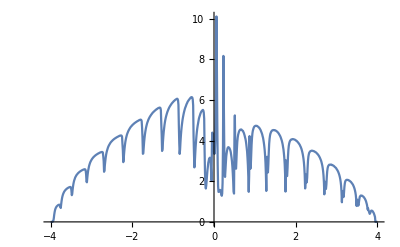

```mathematica
ListPlot[%45,Joined->True]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp8.dat",%46]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp8.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.8],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000258147},{-3.99,0.0000405944},{-3.98,0.0000699537},{-3.97,0.000139811},{-3.96,0.000363173},{-3.95,0.00186894},{-3.94,0.0445712},{-3.93,0.0645941},{-3.92,0.142735},{-3.91,0.270996},{-3.9,0.405861},{-3.89,0.505262},{-3.88,0.573593},{-3.87,0.634367},{-3.86,0.678559},{-3.85,0.711987},{-3.84,0.738916},{-3.83,0.757212},{-3.82,0.77859},{-3.81,0.79167},{-3.8,0.80663},{-3.79,0.811554},{-3.78,0.807783},{-3.77,0.749423},{-3.76,0.722252},{-3.75,0.615413},{-3.74,0.737228},{-3.73,0.899929},{-3.72,1.01836},{-3.71,1.13347},{-3.7,1.20164},{-3.69,1.2693},{-3.68,1.32462},{-3.67,1.36625},{-3.66,1.40542},{-3.65,1.444},{-3.64,1.46709},{-3.63,1.49774},{-3.62,1.5156},{-3.61,1.53945},{-3.6,1.55948},{-3.59,1.58136},{-3.58,1.59596},{-3.57,1.61201},{-3.56,1.62294},{-3.55,1.63067},{-3.54,1.64668},{-3.53,1.65127},{-3.52,1.65495},{-3.51,1.65133},{-3.5,1.60637},{-3.49,1.51221},{-3.48,1.26701},{-3.47,1.23505},{-3.46,1.4072},{-3.45,1.56393},{-3.44,1.69759},{-3.43,1.79498},{-3.42,1.87993},{-3.41,1.95566},{-3.4,2.01165},{-3.39,2.06208},{-3.38,2.10957},{-3.37,2.14349},{-3.36,2.1793},{-3.35,2.2136},{-3.34,2.23971},{-3.33,2.26657},{-3.32,2.28746},{-3.31,2.31626},{-3.3,2.33011},{-3.29,2.34713},{-3.28,2.36485},{-3.27,2.38459},{-3.26,2.40018},{-3.25,2.41737},{-3.24,2.42174},{-3.23,2.4417},{-3.22,2.45387},{-3.21,2.46496},{-3.2,2.47322},{-3.19,2.48752},{-3.18,2.49596},{-3.17,2.49923},{-3.16,2.50568},{-3.15,2.49226},{-3.14,2.4332},{-3.13,2.25866},{-3.12,1.93625},{-3.11,1.78058},{-3.1,1.95063},{-3.09,2.13793},{-3.08,2.28176},{-3.07,2.41241},{-3.06,2.5119},{-3.05,2.59142},{-3.04,2.66583},{-3.03,2.7303},{-3.02,2.7784},{-3.01,2.82292},{-3.,2.86488},{-2.99,2.90489},{-2.98,2.93936},{-2.97,2.96544},{-2.96,2.99747},{-2.95,3.02414},{-2.94,3.05128},{-2.93,3.07014},{-2.92,3.08526},{-2.91,3.11073},{-2.9,3.12777},{-2.89,3.14805},{-2.88,3.16292},{-2.87,3.1845},{-2.86,3.19162},{-2.85,3.20786},{-2.84,3.22309},{-2.83,3.23849},{-2.82,3.24961},{-2.81,3.26766},{-2.8,3.27571},{-2.79,3.28636},{-2.78,3.29655},{-2.77,3.30389},{-2.76,3.31019},{-2.75,3.31994},{-2.74,3.3249},{-2.73,3.31614},{-2.72,3.28921},{-2.71,3.10027},{-2.7,2.88737},{-2.69,2.37522},{-2.68,2.32432},{-2.67,2.53761},{-2.66,2.7318},{-2.65,2.88869},{-2.64,3.02682},{-2.63,3.14148},{-2.62,3.23629},{-2.61,3.32048},{-2.6,3.37861},{-2.59,3.44196},{-2.58,3.4907},{-2.57,3.53363},{-2.56,3.58757},{-2.55,3.6213},{-2.54,3.65704},{-2.53,3.68662},{-2.52,3.71652},{-2.51,3.74743},{-2.5,3.77394},{-2.49,3.79598},{-2.48,3.81735},{-2.47,3.84155},{-2.46,3.85545},{-2.45,3.88146},{-2.44,3.89821},{-2.43,3.91695},{-2.42,3.92719},{-2.41,3.94792},{-2.4,3.96102},{-2.39,3.97886},{-2.38,3.99507},{-2.37,4.00879},{-2.36,4.01691},{-2.35,4.0312},{-2.34,4.04091},{-2.33,4.05424},{-2.32,4.06396},{-2.31,4.07763},{-2.3,4.08245},{-2.29,4.09261},{-2.28,4.09922},{-2.27,4.09663},{-2.26,4.08446},{-2.25,4.03063},{-2.24,3.66341},{-2.23,3.3889},{-2.22,2.78721},{-2.21,2.81342},{-2.2,3.04532},{-2.19,3.26541},{-2.18,3.43695},{-2.17,3.59485},{-2.16,3.72195},{-2.15,3.82644},{-2.14,3.92044},{-2.13,3.99578},{-2.12,4.06206},{-2.11,4.11445},{-2.1,4.17569},{-2.09,4.22749},{-2.08,4.26461},{-2.07,4.30457},{-2.06,4.34255},{-2.05,4.37663},{-2.04,4.40998},{-2.03,4.43675},{-2.02,4.46184},{-2.01,4.49174},{-2.,4.51962},{-1.99,4.53556},{-1.98,4.56607},{-1.97,4.58076},{-1.96,4.60178},{-1.95,4.62563},{-1.94,4.63924},{-1.93,4.65848},{-1.92,4.67715},{-1.91,4.68831},{-1.9,4.71283},{-1.89,4.72071},{-1.88,4.73356},{-1.87,4.75238},{-1.86,4.75955},{-1.85,4.77866},{-1.84,4.78689},{-1.83,4.80925},{-1.82,4.81755},{-1.81,4.82161},{-1.8,4.83149},{-1.79,4.82552},{-1.78,4.8145},{-1.77,4.75919},{-1.76,4.4073},{-1.75,3.96908},{-1.74,3.24207},{-1.73,3.08441},{-1.72,3.29383},{-1.71,3.53801},{-1.7,3.74247},{-1.69,3.92891},{-1.68,4.06304},{-1.67,4.18698},{-1.66,4.29886},{-1.65,4.38807},{-1.64,4.47391},{-1.63,4.53752},{-1.62,4.60162},{-1.61,4.65746},{-1.6,4.71067},{-1.59,4.75674},{-1.58,4.79675},{-1.57,4.83924},{-1.56,4.87945},{-1.55,4.91426},{-1.54,4.94547},{-1.53,4.97905},{-1.52,5.00659},{-1.51,5.03525},{-1.5,5.05643},{-1.49,5.09321},{-1.48,5.11189},{-1.47,5.13349},{-1.46,5.16008},{-1.45,5.17102},{-1.44,5.1954},{-1.43,5.213},{-1.42,5.23204},{-1.41,5.2543},{-1.4,5.27717},{-1.39,5.28996},{-1.38,5.3002},{-1.37,5.31954},{-1.36,5.33005},{-1.35,5.34762},{-1.34,5.35091},{-1.33,5.35713},{-1.32,5.35738},{-1.31,5.31752},{-1.3,5.2127},{-1.29,4.48785},{-1.28,4.06309},{-1.27,3.26512},{-1.26,3.23548},{-1.25,3.4846},{-1.24,3.74468},{-1.23,3.97044},{-1.22,4.15938},{-1.21,4.33212},{-1.2,4.45455},{-1.19,4.57662},{-1.18,4.67677},{-1.17,4.7637},{-1.16,4.84962},{-1.15,4.9162},{-1.14,4.98776},{-1.13,5.03868},{-1.12,5.1023},{-1.11,5.14155},{-1.1,5.19346},{-1.09,5.23591},{-1.08,5.27205},{-1.07,5.31648},{-1.06,5.34305},{-1.05,5.38136},{-1.04,5.416},{-1.03,5.44202},{-1.02,5.4702},{-1.01,5.49746},{-1.,5.51923},{-0.99,5.54546},{-0.98,5.57301},{-0.97,5.59019},{-0.96,5.61658},{-0.95,5.63637},{-0.94,5.6552},{-0.93,5.67329},{-0.92,5.68459},{-0.91,5.68992},{-0.9,5.69776},{-0.89,5.6752},{-0.88,5.61253},{-0.87,5.35364},{-0.86,4.268},{-0.85,3.61365},{-0.84,3.00581},{-0.83,3.10865},{-0.82,3.40711},{-0.81,3.68678},{-0.8,3.93113},{-0.79,4.13908},{-0.78,4.29896},{-0.77,4.45911},{-0.76,4.58234},{-0.75,4.70114},{-0.74,4.80517},{-0.73,4.88924},{-0.72,4.96338},{-0.71,5.03447},{-0.7,5.10348},{-0.69,5.16846},{-0.68,5.21157},{-0.67,5.26458},{-0.66,5.32055},{-0.65,5.36919},{-0.64,5.40614},{-0.63,5.45199},{-0.62,5.48547},{-0.61,5.51202},{-0.6,5.53823},{-0.59,5.5772},{-0.58,5.59267},{-0.57,5.61618},{-0.56,5.64375},{-0.55,5.64537},{-0.54,5.6338},{-0.53,5.60059},{-0.52,5.50437},{-0.51,5.19048},{-0.5,3.61436},{-0.49,3.00302},{-0.48,2.32457},{-0.47,2.3676},{-0.46,2.69451},{-0.45,2.99313},{-0.44,3.29415},{-0.43,3.52256},{-0.42,3.70677},{-0.41,3.89331},{-0.4,4.03902},{-0.39,4.18075},{-0.38,4.27312},{-0.37,4.36357},{-0.36,4.46105},{-0.35,4.52717},{-0.34,4.60734},{-0.33,4.6543},{-0.32,4.70589},{-0.31,4.73838},{-0.3,4.76915},{-0.29,4.79553},{-0.28,4.82453},{-0.27,4.81078},{-0.26,4.76437},{-0.25,4.64587},{-0.24,4.31082},{-0.23,2.6728},{-0.22,1.97425},{-0.21,1.63922},{-0.2,1.44369},{-0.19,1.39318},{-0.18,1.45658},{-0.17,1.62283},{-0.16,1.77791},{-0.15,1.94638},{-0.14,2.0521},{-0.13,2.14678},{-0.12,2.21493},{-0.11,2.25091},{-0.1,2.25826},{-0.09,2.14683},{-0.08,1.95962},{-0.07,1.6395},{-0.06,2.41169},{-0.05,4.57924},{-0.04,5.00218},{-0.03,4.85806},{-0.02,4.56326},{-0.01,4.42707},{0.,4.40383},{0.01,4.19037},{0.02,4.26672},{0.03,5.03161},{0.04,6.24708},{0.05,8.58998},{0.06,10.2659},{0.07,8.35492},{0.08,5.77809},{0.09,3.64012},{0.1,2.31503},{0.11,1.5844},{0.12,1.27193},{0.13,1.14595},{0.14,1.11426},{0.15,1.10735},{0.16,1.09654},{0.17,1.11607},{0.18,1.16984},{0.19,1.33994},{0.2,1.67564},{0.21,2.54569},{0.22,4.74836},{0.23,8.37521},{0.24,6.41841},{0.25,4.38157},{0.26,2.73351},{0.27,1.90804},{0.28,1.7339},{0.29,1.90543},{0.3,2.11574},{0.31,2.3276},{0.32,2.48643},{0.33,2.58902},{0.34,2.66567},{0.35,2.69886},{0.36,2.74137},{0.37,2.70654},{0.38,2.68178},{0.39,2.64928},{0.4,2.57759},{0.41,2.48513},{0.42,2.37989},{0.43,2.24187},{0.44,2.05677},{0.45,1.82563},{0.46,1.56278},{0.47,1.27563},{0.48,1.13052},{0.49,1.63318},{0.5,4.77197},{0.51,5.45422},{0.52,4.06405},{0.53,2.79054},{0.54,2.20367},{0.55,2.21817},{0.56,2.5438},{0.57,2.88457},{0.58,3.14466},{0.59,3.33918},{0.6,3.45445},{0.61,3.53623},{0.62,3.61794},{0.63,3.65791},{0.64,3.68791},{0.65,3.71178},{0.66,3.72661},{0.67,3.7398},{0.68,3.72976},{0.69,3.70683},{0.7,3.68909},{0.71,3.67405},{0.72,3.62534},{0.73,3.5903},{0.74,3.5257},{0.75,3.46739},{0.76,3.39519},{0.77,3.28607},{0.78,3.17958},{0.79,3.03841},{0.8,2.86699},{0.81,2.63964},{0.82,2.3711},{0.83,1.98604},{0.84,1.49725},{0.85,1.16949},{0.86,2.70936},{0.87,4.42374},{0.88,3.38279},{0.89,2.61618},{0.9,2.26968},{0.91,2.3916},{0.92,2.78858},{0.93,3.17906},{0.94,3.44853},{0.95,3.65643},{0.96,3.76183},{0.97,3.86256},{0.98,3.92629},{0.99,3.97236},{1.,4.00203},{1.01,4.03121},{1.02,4.03875},{1.03,4.05406},{1.04,4.0524},{1.05,4.05874},{1.06,4.0401},{1.07,4.03028},{1.08,4.01927},{1.09,3.99878},{1.1,3.98109},{1.11,3.96298},{1.12,3.94054},{1.13,3.9013},{1.14,3.8567},{1.15,3.82278},{1.16,3.77456},{1.17,3.71255},{1.18,3.636},{1.19,3.56577},{1.2,3.47288},{1.21,3.3625},{1.22,3.23082},{1.23,3.07919},{1.24,2.86619},{1.25,2.60099},{1.26,2.23835},{1.27,1.7136},{1.28,1.17634},{1.29,3.43914},{1.3,3.34884},{1.31,2.65774},{1.32,2.21912},{1.33,2.20128},{1.34,2.50825},{1.35,2.94024},{1.36,3.27713},{1.37,3.4945},{1.38,3.63994},{1.39,3.73085},{1.4,3.79969},{1.41,3.84648},{1.42,3.88887},{1.43,3.91634},{1.44,3.93817},{1.45,3.94282},{1.46,3.95272},{1.47,3.95842},{1.48,3.95677},{1.49,3.95682},{1.5,3.95272},{1.51,3.95059},{1.52,3.93544},{1.53,3.92129},{1.54,3.90307},{1.55,3.8823},{1.56,3.86195},{1.57,3.84717},{1.58,3.8095},{1.59,3.78751},{1.6,3.74758},{1.61,3.70293},{1.62,3.6728},{1.63,3.62106},{1.64,3.56716},{1.65,3.50024},{1.66,3.43614},{1.67,3.35868},{1.68,3.25738},{1.69,3.13553},{1.7,3.00986},{1.71,2.81193},{1.72,2.58743},{1.73,2.25819},{1.74,1.77982},{1.75,1.14363},{1.76,3.11481},{1.77,2.61806},{1.78,2.22122},{1.79,1.95434},{1.8,2.03409},{1.81,2.38758},{1.82,2.75566},{1.83,3.03021},{1.84,3.22616},{1.85,3.33747},{1.86,3.42137},{1.87,3.47963},{1.88,3.51848},{1.89,3.54638},{1.9,3.56636},{1.91,3.5841},{1.92,3.59095},{1.93,3.59998},{1.94,3.59958},{1.95,3.59952},{1.96,3.59576},{1.97,3.5908},{1.98,3.58285},{1.99,3.56794},{2.,3.5611},{2.01,3.54541},{2.02,3.52636},{2.03,3.51113},{2.04,3.49809},{2.05,3.47358},{2.06,3.44298},{2.07,3.41203},{2.08,3.39011},{2.09,3.35148},{2.1,3.30968},{2.11,3.28161},{2.12,3.23922},{2.13,3.17363},{2.14,3.12146},{2.15,3.04258},{2.16,2.96718},{2.17,2.86208},{2.18,2.74934},{2.19,2.61064},{2.2,2.41952},{2.21,2.17151},{2.22,1.78845},{2.23,1.23026},{2.24,2.07392},{2.25,2.30442},{2.26,2.02561},{2.27,1.81804},{2.28,1.75166},{2.29,1.98112},{2.3,2.27935},{2.31,2.57713},{2.32,2.76169},{2.33,2.88538},{2.34,2.96957},{2.35,3.02027},{2.36,3.05531},{2.37,3.07724},{2.38,3.09394},{2.39,3.09612},{2.4,3.10757},{2.41,3.1064},{2.42,3.10972},{2.43,3.09938},{2.44,3.10474},{2.45,3.08995},{2.46,3.08748},{2.47,3.07021},{2.48,3.05502},{2.49,3.05124},{2.5,3.03266},{2.51,3.00499},{2.52,2.98924},{2.53,2.97011},{2.54,2.94485},{2.55,2.91653},{2.56,2.89053},{2.57,2.8554},{2.58,2.81493},{2.59,2.77774},{2.6,2.72532},{2.61,2.67066},{2.62,2.61314},{2.63,2.54774},{2.64,2.4612},{2.65,2.36081},{2.66,2.23424},{2.67,2.08479},{2.68,1.86673},{2.69,1.52261},{2.7,1.04738},{2.71,2.00986},{2.72,1.86408},{2.73,1.65144},{2.74,1.46755},{2.75,1.45418},{2.76,1.62364},{2.77,1.90296},{2.78,2.1215},{2.79,2.27488},{2.8,2.36207},{2.81,2.41551},{2.82,2.45327},{2.83,2.4745},{2.84,2.49183},{2.85,2.49802},{2.86,2.50563},{2.87,2.49869},{2.88,2.49657},{2.89,2.4911},{2.9,2.47586},{2.91,2.47548},{2.92,2.46023},{2.93,2.4449},{2.94,2.43748},{2.95,2.41324},{2.96,2.38981},{2.97,2.37716},{2.98,2.35164},{2.99,2.32394},{3.,2.29196},{3.01,2.25364},{3.02,2.22656},{3.03,2.19008},{3.04,2.13934},{3.05,2.08323},{3.06,2.0267},{3.07,1.96103},{3.08,1.87135},{3.09,1.75548},{3.1,1.63008},{3.11,1.43159},{3.12,1.13253},{3.13,0.826501},{3.14,1.52386},{3.15,1.41559},{3.16,1.26292},{3.17,1.10786},{3.18,1.0913},{3.19,1.22754},{3.2,1.429},{3.21,1.5932},{3.22,1.68637},{3.23,1.74998},{3.24,1.77945},{3.25,1.79836},{3.26,1.80508},{3.27,1.81457},{3.28,1.81591},{3.29,1.80627},{3.3,1.79838},{3.31,1.78318},{3.32,1.77348},{3.33,1.75573},{3.34,1.73941},{3.35,1.72562},{3.36,1.69364},{3.37,1.67338},{3.38,1.64631},{3.39,1.61258},{3.4,1.57816},{3.41,1.54371},{3.42,1.48953},{3.43,1.4295},{3.44,1.37036},{3.45,1.29685},{3.46,1.1913},{3.47,1.05069},{3.48,0.852661},{3.49,0.655415},{3.5,1.09053},{3.51,1.0168},{3.52,0.89699},{3.53,0.787142},{3.54,0.707648},{3.55,0.727247},{3.56,0.840303},{3.57,0.942446},{3.58,1.02518},{3.59,1.06152},{3.6,1.08959},{3.61,1.09489},{3.62,1.09504},{3.63,1.08744},{3.64,1.07749},{3.65,1.06144},{3.66,1.03958},{3.67,1.02727},{3.68,0.989589},{3.69,0.962698},{3.7,0.922787},{3.71,0.881043},{3.72,0.830592},{3.73,0.768347},{3.74,0.694137},{3.75,0.596158},{3.76,0.487439},{3.77,0.680343},{3.78,0.570013},{3.79,0.535869},{3.8,0.471021},{3.81,0.398663},{3.82,0.35528},{3.83,0.353676},{3.84,0.37733},{3.85,0.408426},{3.86,0.429421},{3.87,0.420297},{3.88,0.420042},{3.89,0.397509},{3.9,0.37454},{3.91,0.341184},{3.92,0.304511},{3.93,0.2715},{3.94,0.239138},{3.95,0.00233014},{3.96,0.000434294},{3.97,0.000162566},{3.98,0.0000809701},{3.99,0.0000463227},{4.,0.0000293076}}

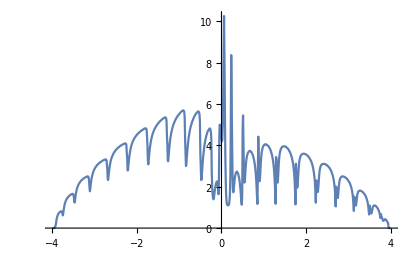

```mathematica
ListPlot[%46,Joined->True]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp9.dat",%47]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp9.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.9],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000262012},{-3.99,0.0000408376},{-3.98,0.0000705971},{-3.97,0.000140266},{-3.96,0.000367833},{-3.95,0.00194454},{-3.94,0.0471871},{-3.93,0.0661051},{-3.92,0.118805},{-3.91,0.21669},{-3.9,0.335272},{-3.89,0.440817},{-3.88,0.516662},{-3.87,0.574509},{-3.86,0.624693},{-3.85,0.65988},{-3.84,0.694621},{-3.83,0.721408},{-3.82,0.743656},{-3.81,0.758453},{-3.8,0.76962},{-3.79,0.774726},{-3.78,0.775718},{-3.77,0.710915},{-3.76,0.691331},{-3.75,0.575011},{-3.74,0.645332},{-3.73,0.786976},{-3.72,0.911646},{-3.71,1.01967},{-3.7,1.1035},{-3.69,1.16793},{-3.68,1.22426},{-3.67,1.27371},{-3.66,1.31555},{-3.65,1.36084},{-3.64,1.38964},{-3.63,1.41715},{-3.62,1.43989},{-3.61,1.46705},{-3.6,1.49124},{-3.59,1.50868},{-3.58,1.52746},{-3.57,1.54301},{-3.56,1.56283},{-3.55,1.57148},{-3.54,1.58362},{-3.53,1.59502},{-3.52,1.59818},{-3.51,1.59421},{-3.5,1.55227},{-3.49,1.45232},{-3.48,1.24468},{-3.47,1.13302},{-3.46,1.25931},{-3.45,1.40714},{-3.44,1.53054},{-3.43,1.64275},{-3.42,1.7326},{-3.41,1.80594},{-3.4,1.86675},{-3.39,1.92426},{-3.38,1.96891},{-3.37,2.01557},{-3.36,2.057},{-3.35,2.08649},{-3.34,2.11738},{-3.33,2.14759},{-3.32,2.17602},{-3.31,2.20201},{-3.3,2.22386},{-3.29,2.24045},{-3.28,2.26309},{-3.27,2.27954},{-3.26,2.29682},{-3.25,2.32037},{-3.24,2.33126},{-3.23,2.34747},{-3.22,2.36026},{-3.21,2.37522},{-3.2,2.38764},{-3.19,2.39602},{-3.18,2.40929},{-3.17,2.41483},{-3.16,2.4169},{-3.15,2.40766},{-3.14,2.34128},{-3.13,2.17265},{-3.12,1.90277},{-3.11,1.66488},{-3.1,1.77951},{-3.09,1.94631},{-3.08,2.08762},{-3.07,2.21794},{-3.06,2.3212},{-3.05,2.40533},{-3.04,2.47839},{-3.03,2.54864},{-3.02,2.60379},{-3.01,2.65115},{-3.,2.6975},{-2.99,2.73468},{-2.98,2.77089},{-2.97,2.81836},{-2.96,2.83705},{-2.95,2.86914},{-2.94,2.89995},{-2.93,2.91658},{-2.92,2.94477},{-2.91,2.96695},{-2.9,2.9904},{-2.89,3.00771},{-2.88,3.03341},{-2.87,3.04346},{-2.86,3.06526},{-2.85,3.07958},{-2.84,3.09336},{-2.83,3.10449},{-2.82,3.12337},{-2.81,3.14012},{-2.8,3.15529},{-2.79,3.16358},{-2.78,3.17385},{-2.77,3.18947},{-2.76,3.19398},{-2.75,3.20887},{-2.74,3.20948},{-2.73,3.20513},{-2.72,3.17026},{-2.71,2.97128},{-2.7,2.78062},{-2.69,2.30195},{-2.68,2.1573},{-2.67,2.30072},{-2.66,2.49028},{-2.65,2.65684},{-2.64,2.78996},{-2.63,2.89725},{-2.62,2.99822},{-2.61,3.08541},{-2.6,3.15621},{-2.59,3.21833},{-2.58,3.27337},{-2.57,3.32396},{-2.56,3.37359},{-2.55,3.41341},{-2.54,3.45319},{-2.53,3.49189},{-2.52,3.52121},{-2.51,3.55207},{-2.5,3.57936},{-2.49,3.60883},{-2.48,3.62802},{-2.47,3.65911},{-2.46,3.67155},{-2.45,3.69551},{-2.44,3.72009},{-2.43,3.73794},{-2.42,3.75931},{-2.41,3.77346},{-2.4,3.79177},{-2.39,3.80503},{-2.38,3.82346},{-2.37,3.84313},{-2.36,3.85368},{-2.35,3.86533},{-2.34,3.87921},{-2.33,3.89521},{-2.32,3.90644},{-2.31,3.92039},{-2.3,3.93286},{-2.29,3.93989},{-2.28,3.93743},{-2.27,3.93984},{-2.26,3.92981},{-2.25,3.86297},{-2.24,3.46738},{-2.23,3.24655},{-2.22,2.66737},{-2.21,2.58717},{-2.2,2.77126},{-2.19,2.97671},{-2.18,3.15625},{-2.17,3.31011},{-2.16,3.43423},{-2.15,3.53943},{-2.14,3.63281},{-2.13,3.71744},{-2.12,3.78145},{-2.11,3.85101},{-2.1,3.90477},{-2.09,3.96552},{-2.08,4.00624},{-2.07,4.04374},{-2.06,4.09212},{-2.05,4.12681},{-2.04,4.16489},{-2.03,4.19598},{-2.02,4.22393},{-2.01,4.26078},{-2.,4.28908},{-1.99,4.31591},{-1.98,4.3332},{-1.97,4.35382},{-1.96,4.38318},{-1.95,4.40327},{-1.94,4.42415},{-1.93,4.44197},{-1.92,4.46605},{-1.91,4.4816},{-1.9,4.5003},{-1.89,4.51443},{-1.88,4.53577},{-1.87,4.5495},{-1.86,4.56248},{-1.85,4.58026},{-1.84,4.5974},{-1.83,4.61119},{-1.82,4.61807},{-1.81,4.6351},{-1.8,4.63934},{-1.79,4.63929},{-1.78,4.62084},{-1.77,4.55393},{-1.76,4.18172},{-1.75,3.79506},{-1.74,3.12712},{-1.73,2.87521},{-1.72,3.00493},{-1.71,3.21028},{-1.7,3.4108},{-1.69,3.57391},{-1.68,3.71839},{-1.67,3.8481},{-1.66,3.96268},{-1.65,4.0591},{-1.64,4.13222},{-1.63,4.20417},{-1.62,4.27444},{-1.61,4.33519},{-1.6,4.39075},{-1.59,4.44556},{-1.58,4.49028},{-1.57,4.53412},{-1.56,4.57184},{-1.55,4.61066},{-1.54,4.6484},{-1.53,4.6816},{-1.52,4.71719},{-1.51,4.73708},{-1.5,4.7658},{-1.49,4.79933},{-1.48,4.82677},{-1.47,4.8511},{-1.46,4.87602},{-1.45,4.90017},{-1.44,4.92081},{-1.43,4.93911},{-1.42,4.96266},{-1.41,4.98022},{-1.4,5.00246},{-1.39,5.01846},{-1.38,5.03948},{-1.37,5.05706},{-1.36,5.0708},{-1.35,5.08994},{-1.34,5.1027},{-1.33,5.09854},{-1.32,5.08817},{-1.31,5.04818},{-1.3,4.93921},{-1.29,4.19153},{-1.28,3.81762},{-1.27,3.09713},{-1.26,2.92067},{-1.25,3.10852},{-1.24,3.356},{-1.23,3.55764},{-1.22,3.75405},{-1.21,3.90737},{-1.2,4.04739},{-1.19,4.15645},{-1.18,4.26435},{-1.17,4.35788},{-1.16,4.44112},{-1.15,4.531},{-1.14,4.59197},{-1.13,4.65395},{-1.12,4.71661},{-1.11,4.76345},{-1.1,4.81725},{-1.09,4.85636},{-1.08,4.90176},{-1.07,4.94322},{-1.06,4.97603},{-1.05,5.01442},{-1.04,5.04836},{-1.03,5.08112},{-1.02,5.10778},{-1.01,5.14091},{-1.,5.173},{-0.99,5.19731},{-0.98,5.22164},{-0.97,5.24451},{-0.96,5.26506},{-0.95,5.2877},{-0.94,5.30728},{-0.93,5.32472},{-0.92,5.34084},{-0.91,5.35255},{-0.9,5.35384},{-0.89,5.3273},{-0.88,5.24797},{-0.87,4.97315},{-0.86,3.88121},{-0.85,3.35835},{-0.84,2.70904},{-0.83,2.72572},{-0.82,2.9718},{-0.81,3.21339},{-0.8,3.44627},{-0.79,3.65161},{-0.78,3.80662},{-0.77,3.95292},{-0.76,4.08717},{-0.75,4.18697},{-0.74,4.30337},{-0.73,4.39141},{-0.72,4.47866},{-0.71,4.55622},{-0.7,4.61442},{-0.69,4.69992},{-0.68,4.74008},{-0.67,4.79007},{-0.66,4.84961},{-0.65,4.89846},{-0.64,4.93053},{-0.63,4.98526},{-0.62,5.01885},{-0.61,5.05347},{-0.6,5.08841},{-0.59,5.10462},{-0.58,5.14082},{-0.57,5.16225},{-0.56,5.18149},{-0.55,5.18726},{-0.54,5.17917},{-0.53,5.13331},{-0.52,5.02812},{-0.51,4.65959},{-0.5,3.07203},{-0.49,2.63892},{-0.48,2.03052},{-0.47,1.96958},{-0.46,2.16526},{-0.45,2.4193},{-0.44,2.7021},{-0.43,2.91358},{-0.42,3.11075},{-0.41,3.28901},{-0.4,3.43407},{-0.39,3.55625},{-0.38,3.67119},{-0.37,3.76758},{-0.36,3.85136},{-0.35,3.93551},{-0.34,3.99414},{-0.33,4.04506},{-0.32,4.103},{-0.31,4.14524},{-0.3,4.16829},{-0.29,4.199},{-0.28,4.20986},{-0.27,4.1816},{-0.26,4.1381},{-0.25,3.97931},{-0.24,3.61488},{-0.23,2.04047},{-0.22,1.74169},{-0.21,1.63142},{-0.2,1.41406},{-0.19,1.26963},{-0.18,1.22629},{-0.17,1.23575},{-0.16,1.31812},{-0.15,1.38402},{-0.14,1.45683},{-0.13,1.4989},{-0.12,1.55216},{-0.11,1.55985},{-0.1,1.55758},{-0.09,1.49412},{-0.08,1.39264},{-0.07,1.37813},{-0.06,3.18994},{-0.05,5.38476},{-0.04,5.58284},{-0.03,5.46137},{-0.02,5.30161},{-0.01,5.25165},{0.,5.15108},{0.01,5.08691},{0.02,5.16662},{0.03,5.83661},{0.04,7.03389},{0.05,9.13293},{0.06,10.3297},{0.07,8.62641},{0.08,6.47499},{0.09,4.53091},{0.1,3.09337},{0.11,2.23921},{0.12,1.67917},{0.13,1.40029},{0.14,1.28334},{0.15,1.22809},{0.16,1.24416},{0.17,1.33497},{0.18,1.48212},{0.19,1.79516},{0.2,2.3153},{0.21,3.35384},{0.22,5.47926},{0.23,8.65877},{0.24,6.70411},{0.25,4.8937},{0.26,3.21303},{0.27,2.04544},{0.28,1.55336},{0.29,1.37647},{0.3,1.39895},{0.31,1.4918},{0.32,1.63468},{0.33,1.73178},{0.34,1.80607},{0.35,1.8633},{0.36,1.90101},{0.37,1.88249},{0.38,1.86704},{0.39,1.83931},{0.4,1.78844},{0.41,1.70076},{0.42,1.58515},{0.43,1.46685},{0.44,1.34921},{0.45,1.19247},{0.46,1.03441},{0.47,0.968935},{0.48,1.18553},{0.49,2.13237},{0.5,5.43088},{0.51,5.75125},{0.52,4.31229},{0.53,3.01697},{0.54,2.16212},{0.55,1.83337},{0.56,1.84616},{0.57,2.0507},{0.58,2.27848},{0.59,2.47455},{0.6,2.61382},{0.61,2.75387},{0.62,2.82474},{0.63,2.89948},{0.64,2.92059},{0.65,2.96688},{0.66,2.97599},{0.67,2.99389},{0.68,2.99097},{0.69,2.99347},{0.7,2.96094},{0.71,2.94723},{0.72,2.92558},{0.73,2.88447},{0.74,2.82873},{0.75,2.7683},{0.76,2.68621},{0.77,2.59071},{0.78,2.47746},{0.79,2.34799},{0.8,2.15952},{0.81,1.95936},{0.82,1.67845},{0.83,1.35083},{0.84,1.0772},{0.85,1.17622},{0.86,3.29268},{0.87,4.54042},{0.88,3.56565},{0.89,2.70887},{0.9,2.13667},{0.91,1.98161},{0.92,2.098},{0.93,2.34659},{0.94,2.60784},{0.95,2.84141},{0.96,3.0145},{0.97,3.12262},{0.98,3.21492},{0.99,3.27216},{1.,3.32793},{1.01,3.3613},{1.02,3.3848},{1.03,3.40614},{1.04,3.42049},{1.05,3.42183},{1.06,3.42188},{1.07,3.41698},{1.08,3.40998},{1.09,3.39153},{1.1,3.37895},{1.11,3.35411},{1.12,3.32636},{1.13,3.29849},{1.14,3.26012},{1.15,3.21656},{1.16,3.18228},{1.17,3.10438},{1.18,3.03188},{1.19,2.95499},{1.2,2.87686},{1.21,2.76399},{1.22,2.63801},{1.23,2.45695},{1.24,2.26678},{1.25,1.99176},{1.26,1.62444},{1.27,1.17697},{1.28,1.08751},{1.29,3.7102},{1.3,3.46564},{1.31,2.77154},{1.32,2.22006},{1.33,1.91305},{1.34,1.94884},{1.35,2.20271},{1.36,2.49281},{1.37,2.75094},{1.38,2.93551},{1.39,3.05949},{1.4,3.16959},{1.41,3.24044},{1.42,3.28641},{1.43,3.34039},{1.44,3.37597},{1.45,3.38808},{1.46,3.40484},{1.47,3.41401},{1.48,3.4217},{1.49,3.41658},{1.5,3.41861},{1.51,3.4174},{1.52,3.40887},{1.53,3.39557},{1.54,3.38181},{1.55,3.36757},{1.56,3.34361},{1.57,3.32665},{1.58,3.30419},{1.59,3.27301},{1.6,3.2306},{1.61,3.20287},{1.62,3.15396},{1.63,3.11097},{1.64,3.0485},{1.65,2.98936},{1.66,2.92234},{1.67,2.83404},{1.68,2.74136},{1.69,2.62163},{1.7,2.48845},{1.71,2.29971},{1.72,2.06375},{1.73,1.73293},{1.74,1.25499},{1.75,1.03577},{1.76,3.2029},{1.77,2.70703},{1.78,2.25046},{1.79,1.89747},{1.8,1.73806},{1.81,1.83752},{1.82,2.07306},{1.83,2.33756},{1.84,2.56324},{1.85,2.73061},{1.86,2.8517},{1.87,2.93315},{1.88,2.991},{1.89,3.0386},{1.9,3.07181},{1.91,3.09432},{1.92,3.11245},{1.93,3.1259},{1.94,3.13822},{1.95,3.13613},{1.96,3.136},{1.97,3.13102},{1.98,3.13267},{1.99,3.12282},{2.,3.111},{2.01,3.10351},{2.02,3.08693},{2.03,3.07014},{2.04,3.05544},{2.05,3.02684},{2.06,3.00741},{2.07,2.97131},{2.08,2.94435},{2.09,2.90851},{2.1,2.8819},{2.11,2.83499},{2.12,2.77719},{2.13,2.72551},{2.14,2.66677},{2.15,2.60146},{2.16,2.51355},{2.17,2.41121},{2.18,2.30137},{2.19,2.15575},{2.2,1.97216},{2.21,1.7161},{2.22,1.33676},{2.23,0.958511},{2.24,2.21107},{2.25,2.33637},{2.26,2.05358},{2.27,1.80663},{2.28,1.58446},{2.29,1.57098},{2.3,1.72639},{2.31,1.9471},{2.32,2.16359},{2.33,2.33405},{2.34,2.4474},{2.35,2.53973},{2.36,2.60394},{2.37,2.63272},{2.38,2.67906},{2.39,2.68803},{2.4,2.70047},{2.41,2.7059},{2.42,2.71517},{2.43,2.71208},{2.44,2.71841},{2.45,2.71164},{2.46,2.70617},{2.47,2.69195},{2.48,2.68847},{2.49,2.66709},{2.5,2.65652},{2.51,2.63957},{2.52,2.62068},{2.53,2.59631},{2.54,2.57693},{2.55,2.54337},{2.56,2.51379},{2.57,2.47848},{2.58,2.44429},{2.59,2.39974},{2.6,2.35755},{2.61,2.29979},{2.62,2.23719},{2.63,2.16903},{2.64,2.08593},{2.65,1.99247},{2.66,1.85769},{2.67,1.69929},{2.68,1.47182},{2.69,1.17501},{2.7,0.84971},{2.71,2.0614},{2.72,1.86848},{2.73,1.66561},{2.74,1.44139},{2.75,1.30683},{2.76,1.28799},{2.77,1.41227},{2.78,1.59543},{2.79,1.78402},{2.8,1.91264},{2.81,2.00476},{2.82,2.07571},{2.83,2.12095},{2.84,2.14156},{2.85,2.15114},{2.86,2.16691},{2.87,2.17421},{2.88,2.1829},{2.89,2.17696},{2.9,2.16457},{2.91,2.15943},{2.92,2.14213},{2.93,2.14281},{2.94,2.13174},{2.95,2.11131},{2.96,2.08981},{2.97,2.07709},{2.98,2.04538},{2.99,2.0257},{3.,1.99364},{3.01,1.96176},{3.02,1.92302},{3.03,1.8807},{3.04,1.83548},{3.05,1.78148},{3.06,1.72427},{3.07,1.64755},{3.08,1.57393},{3.09,1.45887},{3.1,1.32015},{3.11,1.11768},{3.12,0.871885},{3.13,0.781449},{3.14,1.56624},{3.15,1.43029},{3.16,1.2555},{3.17,1.1042},{3.18,0.967225},{3.19,0.950426},{3.2,1.0378},{3.21,1.18581},{3.22,1.3059},{3.23,1.39805},{3.24,1.46242},{3.25,1.4978},{3.26,1.52442},{3.27,1.53411},{3.28,1.54952},{3.29,1.54312},{3.3,1.54319},{3.31,1.53656},{3.32,1.5301},{3.33,1.51754},{3.34,1.49981},{3.35,1.48521},{3.36,1.45376},{3.37,1.43745},{3.38,1.40571},{3.39,1.37687},{3.4,1.33936},{3.41,1.30142},{3.42,1.25617},{3.43,1.20286},{3.44,1.12954},{3.45,1.04929},{3.46,0.955064},{3.47,0.823459},{3.48,0.656969},{3.49,0.612182},{3.5,1.10486},{3.51,1.02368},{3.52,0.923686},{3.53,0.824455},{3.54,0.705478},{3.55,0.626055},{3.56,0.618505},{3.57,0.675398},{3.58,0.752501},{3.59,0.805481},{3.6,0.850143},{3.61,0.873838},{3.62,0.889746},{3.63,0.889092},{3.64,0.889854},{3.65,0.873045},{3.66,0.85223},{3.67,0.833829},{3.68,0.809135},{3.69,0.785215},{3.7,0.748015},{3.71,0.711514},{3.72,0.661664},{3.73,0.61028},{3.74,0.541743},{3.75,0.470574},{3.76,0.433367},{3.77,0.712258},{3.78,0.56925},{3.79,0.537895},{3.8,0.49057},{3.81,0.439833},{3.82,0.384531},{3.83,0.330067},{3.84,0.301702},{3.85,0.303168},{3.86,0.313093},{3.87,0.323124},{3.88,0.322437},{3.89,0.312702},{3.9,0.300907},{3.91,0.278735},{3.92,0.26168},{3.93,0.253253},{3.94,0.247441},{3.95,0.00235451},{3.96,0.00043282},{3.97,0.00016319},{3.98,0.0000812261},{3.99,0.0000468145},{4.,0.0000297911}}

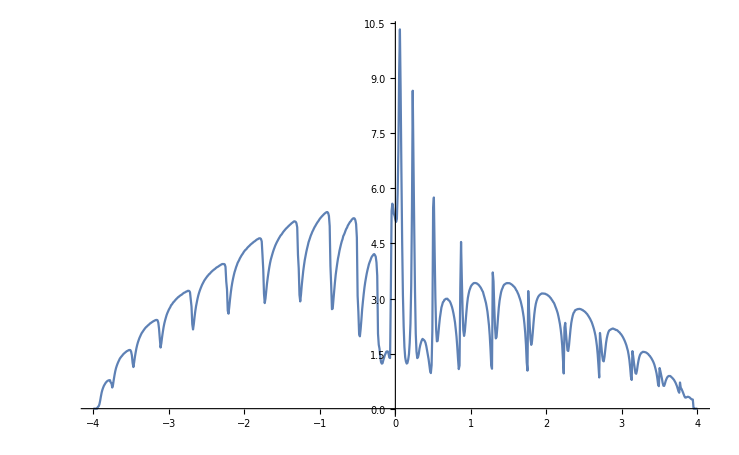

```mathematica
ListPlot[%47,Joined->True]
```

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp10.dat",%48]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp10.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,1.0],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000262011},{-3.99,0.0000414983},{-3.98,0.0000710896},{-3.97,0.000142492},{-3.96,0.000372727},{-3.95,0.00193273},{-3.94,0.0507362},{-3.93,0.0671834},{-3.92,0.105965},{-3.91,0.177883},{-3.9,0.287965},{-3.89,0.381569},{-3.88,0.454151},{-3.87,0.528154},{-3.86,0.578087},{-3.85,0.615446},{-3.84,0.652172},{-3.83,0.678709},{-3.82,0.70483},{-3.81,0.720053},{-3.8,0.738749},{-3.79,0.744798},{-3.78,0.74359},{-3.77,0.681399},{-3.76,0.662936},{-3.75,0.54647},{-3.74,0.569347},{-3.73,0.68777},{-3.72,0.819054},{-3.71,0.919489},{-3.7,1.00181},{-3.69,1.06832},{-3.68,1.12957},{-3.67,1.18811},{-3.66,1.22342},{-3.65,1.27028},{-3.64,1.30343},{-3.63,1.33931},{-3.62,1.36823},{-3.61,1.3917},{-3.6,1.42013},{-3.59,1.44112},{-3.58,1.46661},{-3.57,1.48024},{-3.56,1.49797},{-3.55,1.51231},{-3.54,1.52237},{-3.53,1.53453},{-3.52,1.5426},{-3.51,1.54272},{-3.5,1.48827},{-3.49,1.39152},{-3.48,1.20518},{-3.47,1.05123},{-3.46,1.13887},{-3.45,1.27543},{-3.44,1.39824},{-3.43,1.50319},{-3.42,1.59689},{-3.41,1.68079},{-3.4,1.73999},{-3.39,1.79977},{-3.38,1.85022},{-3.37,1.89236},{-3.36,1.92891},{-3.35,1.9721},{-3.34,2.00935},{-3.33,2.03686},{-3.32,2.06942},{-3.31,2.09135},{-3.3,2.11664},{-3.29,2.13837},{-3.28,2.16934},{-3.27,2.18566},{-3.26,2.20276},{-3.25,2.22017},{-3.24,2.23976},{-3.23,2.25634},{-3.22,2.2673},{-3.21,2.28376},{-3.2,2.30241},{-3.19,2.31388},{-3.18,2.32054},{-3.17,2.33547},{-3.16,2.33069},{-3.15,2.32494},{-3.14,2.25803},{-3.13,2.08089},{-3.12,1.86134},{-3.11,1.57391},{-3.1,1.629},{-3.09,1.77833},{-3.08,1.91927},{-3.07,2.04268},{-3.06,2.13982},{-3.05,2.23934},{-3.04,2.30696},{-3.03,2.37666},{-3.02,2.433},{-3.01,2.48704},{-3.,2.54059},{-2.99,2.5779},{-2.98,2.61729},{-2.97,2.66207},{-2.96,2.69104},{-2.95,2.72498},{-2.94,2.7529},{-2.93,2.77662},{-2.92,2.80779},{-2.91,2.8274},{-2.9,2.84891},{-2.89,2.87081},{-2.88,2.89356},{-2.87,2.91633},{-2.86,2.92885},{-2.85,2.95118},{-2.84,2.96708},{-2.83,2.98643},{-2.82,3.00473},{-2.81,3.01665},{-2.8,3.03219},{-2.79,3.04459},{-2.78,3.06012},{-2.77,3.07678},{-2.76,3.0806},{-2.75,3.09285},{-2.74,3.09818},{-2.73,3.08873},{-2.72,3.05485},{-2.71,2.84684},{-2.7,2.66674},{-2.69,2.25711},{-2.68,2.02649},{-2.67,2.12184},{-2.66,2.28365},{-2.65,2.43313},{-2.64,2.56675},{-2.63,2.68484},{-2.62,2.77486},{-2.61,2.86728},{-2.6,2.94317},{-2.59,3.0108},{-2.58,3.07167},{-2.57,3.12268},{-2.56,3.17043},{-2.55,3.22688},{-2.54,3.26283},{-2.53,3.30111},{-2.52,3.33543},{-2.51,3.36718},{-2.5,3.39073},{-2.49,3.42372},{-2.48,3.45145},{-2.47,3.47514},{-2.46,3.49976},{-2.45,3.52283},{-2.44,3.54462},{-2.43,3.57166},{-2.42,3.58822},{-2.41,3.61044},{-2.4,3.63092},{-2.39,3.64781},{-2.38,3.66448},{-2.37,3.68083},{-2.36,3.69375},{-2.35,3.71133},{-2.34,3.7273},{-2.33,3.73865},{-2.32,3.75484},{-2.31,3.77065},{-2.3,3.7772},{-2.29,3.78993},{-2.28,3.8006},{-2.27,3.79515},{-2.26,3.7767},{-2.25,3.71335},{-2.24,3.30192},{-2.23,3.11304},{-2.22,2.58338},{-2.21,2.42127},{-2.2,2.54085},{-2.19,2.72654},{-2.18,2.89724},{-2.17,3.04179},{-2.16,3.16317},{-2.15,3.28692},{-2.14,3.37813},{-2.13,3.45654},{-2.12,3.53737},{-2.11,3.60471},{-2.1,3.65945},{-2.09,3.71212},{-2.08,3.77091},{-2.07,3.81587},{-2.06,3.8568},{-2.05,3.90078},{-2.04,3.93277},{-2.03,3.96997},{-2.02,4.00483},{-2.01,4.03409},{-2.,4.06527},{-1.99,4.09106},{-1.98,4.11778},{-1.97,4.14467},{-1.96,4.16549},{-1.95,4.18845},{-1.94,4.21164},{-1.93,4.23933},{-1.92,4.25421},{-1.91,4.28222},{-1.9,4.29442},{-1.89,4.32065},{-1.88,4.33204},{-1.87,4.35526},{-1.86,4.37192},{-1.85,4.38908},{-1.84,4.40291},{-1.83,4.4207},{-1.82,4.43182},{-1.81,4.44288},{-1.8,4.4482},{-1.79,4.44833},{-1.78,4.42776},{-1.77,4.36314},{-1.76,3.9644},{-1.75,3.5925},{-1.74,3.02923},{-1.73,2.69912},{-1.72,2.75565},{-1.71,2.92744},{-1.7,3.1135},{-1.69,3.267},{-1.68,3.41347},{-1.67,3.54889},{-1.66,3.66077},{-1.65,3.74067},{-1.64,3.82728},{-1.63,3.91256},{-1.62,3.9757},{-1.61,4.03785},{-1.6,4.09853},{-1.59,4.1537},{-1.58,4.20509},{-1.57,4.25037},{-1.56,4.27784},{-1.55,4.3359},{-1.54,4.37018},{-1.53,4.39649},{-1.52,4.44841},{-1.51,4.47311},{-1.5,4.49833},{-1.49,4.5244},{-1.48,4.55859},{-1.47,4.58282},{-1.46,4.61264},{-1.45,4.63468},{-1.44,4.66725},{-1.43,4.6803},{-1.42,4.71037},{-1.41,4.72976},{-1.4,4.74656},{-1.39,4.77179},{-1.38,4.78671},{-1.37,4.8075},{-1.36,4.82457},{-1.35,4.83159},{-1.34,4.84495},{-1.33,4.84892},{-1.32,4.84572},{-1.31,4.80123},{-1.3,4.67038},{-1.29,3.8734},{-1.28,3.59477},{-1.27,2.93812},{-1.26,2.70768},{-1.25,2.81457},{-1.24,3.022},{-1.23,3.21849},{-1.22,3.3821},{-1.21,3.54082},{-1.2,3.6836},{-1.19,3.79778},{-1.18,3.89948},{-1.17,4.00068},{-1.16,4.07715},{-1.15,4.16187},{-1.14,4.23077},{-1.13,4.29072},{-1.12,4.35896},{-1.11,4.40566},{-1.1,4.45213},{-1.09,4.51123},{-1.08,4.5527},{-1.07,4.59829},{-1.06,4.64003},{-1.05,4.67008},{-1.04,4.70634},{-1.03,4.73603},{-1.02,4.76911},{-1.01,4.80453},{-1.,4.84068},{-0.99,4.86153},{-0.98,4.88549},{-0.97,4.914},{-0.96,4.93839},{-0.95,4.9599},{-0.94,4.99174},{-0.93,5.00835},{-0.92,5.01647},{-0.91,5.02837},{-0.9,5.02904},{-0.89,4.99983},{-0.88,4.90934},{-0.87,4.60558},{-0.86,3.49142},{-0.85,3.11163},{-0.84,2.51084},{-0.83,2.39553},{-0.82,2.58377},{-0.81,2.81343},{-0.8,3.04239},{-0.79,3.21835},{-0.78,3.38544},{-0.77,3.51431},{-0.76,3.6494},{-0.75,3.75974},{-0.74,3.86488},{-0.73,3.96461},{-0.72,4.03837},{-0.71,4.11627},{-0.7,4.18238},{-0.69,4.24883},{-0.68,4.31125},{-0.67,4.35671},{-0.66,4.42317},{-0.65,4.46962},{-0.64,4.51063},{-0.63,4.55877},{-0.62,4.59533},{-0.61,4.6277},{-0.6,4.66405},{-0.59,4.69176},{-0.58,4.72543},{-0.57,4.74591},{-0.56,4.75153},{-0.55,4.76992},{-0.54,4.75296},{-0.53,4.70306},{-0.52,4.56418},{-0.51,4.16185},{-0.5,2.59178},{-0.49,2.32071},{-0.48,1.77433},{-0.47,1.65648},{-0.46,1.73796},{-0.45,1.96731},{-0.44,2.20161},{-0.43,2.41569},{-0.42,2.58902},{-0.41,2.75196},{-0.4,2.8956},{-0.39,3.03846},{-0.38,3.14199},{-0.37,3.23742},{-0.36,3.32724},{-0.35,3.39563},{-0.34,3.45742},{-0.33,3.50543},{-0.32,3.54153},{-0.31,3.60017},{-0.3,3.6255},{-0.29,3.63982},{-0.28,3.64511},{-0.27,3.63396},{-0.26,3.56566},{-0.25,3.4154},{-0.24,2.98707},{-0.23,1.67225},{-0.22,1.68221},{-0.21,1.65344},{-0.2,1.49384},{-0.19,1.29849},{-0.18,1.17481},{-0.17,1.08947},{-0.16,1.07935},{-0.15,1.10061},{-0.14,1.10734},{-0.13,1.13604},{-0.12,1.15685},{-0.11,1.1635},{-0.1,1.16381},{-0.09,1.14478},{-0.08,1.18055},{-0.07,1.49937},{-0.06,3.9242},{-0.05,6.04302},{-0.04,6.178},{-0.03,6.08152},{-0.02,5.90782},{-0.01,5.83608},{0.,5.8373},{0.01,5.73877},{0.02,5.79582},{0.03,6.49579},{0.04,7.65695},{0.05,9.58318},{0.06,10.4035},{0.07,8.81679},{0.08,6.99878},{0.09,5.15791},{0.1,3.77481},{0.11,2.90323},{0.12,2.34845},{0.13,1.97822},{0.14,1.78007},{0.15,1.69811},{0.16,1.70059},{0.17,1.80988},{0.18,1.99576},{0.19,2.37583},{0.2,2.95292},{0.21,4.07205},{0.22,6.14944},{0.23,8.77293},{0.24,7.02217},{0.25,5.15231},{0.26,3.63447},{0.27,2.52168},{0.28,1.76845},{0.29,1.32214},{0.3,1.14658},{0.31,1.0897},{0.32,1.10333},{0.33,1.12792},{0.34,1.18588},{0.35,1.20817},{0.36,1.24378},{0.37,1.23844},{0.38,1.23075},{0.39,1.21019},{0.4,1.16905},{0.41,1.12079},{0.42,1.03972},{0.43,0.971683},{0.44,0.898837},{0.45,0.859102},{0.46,0.887177},{0.47,1.05087},{0.48,1.54396},{0.49,2.72831},{0.5,5.86938},{0.51,5.91973},{0.52,4.43165},{0.53,3.24587},{0.54,2.38195},{0.55,1.77654},{0.56,1.52162},{0.57,1.51555},{0.58,1.62705},{0.59,1.77841},{0.6,1.90211},{0.61,2.02306},{0.62,2.11389},{0.63,2.19776},{0.64,2.26217},{0.65,2.28498},{0.66,2.32829},{0.67,2.33072},{0.68,2.33979},{0.69,2.35001},{0.7,2.3319},{0.71,2.31936},{0.72,2.29344},{0.73,2.24986},{0.74,2.19902},{0.75,2.14529},{0.76,2.06978},{0.77,1.96996},{0.78,1.86417},{0.79,1.72924},{0.8,1.56755},{0.81,1.36542},{0.82,1.14008},{0.83,0.951163},{0.84,0.925048},{0.85,1.42114},{0.86,3.67981},{0.87,4.72534},{0.88,3.67873},{0.89,2.75883},{0.9,2.2235},{0.91,1.82398},{0.92,1.69687},{0.93,1.76863},{0.94,1.94687},{0.95,2.12684},{0.96,2.29705},{0.97,2.4434},{0.98,2.55619},{0.99,2.63875},{1.,2.70889},{1.01,2.74588},{1.02,2.77381},{1.03,2.8101},{1.04,2.83885},{1.05,2.84384},{1.06,2.84833},{1.07,2.84513},{1.08,2.82852},{1.09,2.82752},{1.1,2.81282},{1.11,2.7991},{1.12,2.75816},{1.13,2.74566},{1.14,2.69744},{1.15,2.66333},{1.16,2.61566},{1.17,2.56473},{1.18,2.49455},{1.19,2.41727},{1.2,2.31187},{1.21,2.19793},{1.22,2.07935},{1.23,1.91761},{1.24,1.71673},{1.25,1.45372},{1.26,1.15815},{1.27,0.89529},{1.28,1.24442},{1.29,4.03852},{1.3,3.56203},{1.31,2.86162},{1.32,2.25745},{1.33,1.87772},{1.34,1.70206},{1.35,1.73008},{1.36,1.88619},{1.37,2.08608},{1.38,2.28407},{1.39,2.42038},{1.4,2.55672},{1.41,2.65451},{1.42,2.71999},{1.43,2.78216},{1.44,2.82067},{1.45,2.85644},{1.46,2.87696},{1.47,2.89284},{1.48,2.89823},{1.49,2.91372},{1.5,2.91325},{1.51,2.92122},{1.52,2.91348},{1.53,2.91022},{1.54,2.89467},{1.55,2.8785},{1.56,2.86563},{1.57,2.84407},{1.58,2.82083},{1.59,2.79557},{1.6,2.76196},{1.61,2.71925},{1.62,2.68631},{1.63,2.6374},{1.64,2.58307},{1.65,2.52461},{1.66,2.44325},{1.67,2.36567},{1.68,2.26109},{1.69,2.15153},{1.7,1.99384},{1.71,1.81944},{1.72,1.58621},{1.73,1.27952},{1.74,0.94688},{1.75,1.07964},{1.76,3.316},{1.77,2.78672},{1.78,2.2946},{1.79,1.88627},{1.8,1.62452},{1.81,1.54758},{1.82,1.61417},{1.83,1.7774},{1.84,1.96577},{1.85,2.14768},{1.86,2.28518},{1.87,2.39014},{1.88,2.46879},{1.89,2.54095},{1.9,2.58125},{1.91,2.62228},{1.92,2.64547},{1.93,2.67334},{1.94,2.68977},{1.95,2.6842},{1.96,2.69752},{1.97,2.69754},{1.98,2.69894},{1.99,2.68258},{2.,2.68125},{2.01,2.68088},{2.02,2.66512},{2.03,2.64893},{2.04,2.61976},{2.05,2.60686},{2.06,2.59533},{2.07,2.56021},{2.08,2.5323},{2.09,2.49521},{2.1,2.46499},{2.11,2.41543},{2.12,2.36834},{2.13,2.3213},{2.14,2.26253},{2.15,2.19095},{2.16,2.10781},{2.17,2.00837},{2.18,1.89357},{2.19,1.73784},{2.2,1.54515},{2.21,1.29919},{2.22,0.987444},{2.23,0.838703},{2.24,2.38371},{2.25,2.40334},{2.26,2.07581},{2.27,1.77117},{2.28,1.55144},{2.29,1.41458},{2.3,1.37645},{2.31,1.47535},{2.32,1.64271},{2.33,1.79548},{2.34,1.93889},{2.35,2.03804},{2.36,2.12239},{2.37,2.19104},{2.38,2.23261},{2.39,2.26403},{2.4,2.29378},{2.41,2.30769},{2.42,2.32003},{2.43,2.33182},{2.44,2.33635},{2.45,2.33415},{2.46,2.32891},{2.47,2.32616},{2.48,2.31508},{2.49,2.30542},{2.5,2.29807},{2.51,2.28281},{2.52,2.25977},{2.53,2.23509},{2.54,2.21802},{2.55,2.18763},{2.56,2.16473},{2.57,2.12699},{2.58,2.08948},{2.59,2.05181},{2.6,2.01046},{2.61,1.95175},{2.62,1.88861},{2.63,1.8232},{2.64,1.73874},{2.65,1.63488},{2.66,1.51225},{2.67,1.34266},{2.68,1.1229},{2.69,0.873595},{2.7,0.794415},{2.71,2.11162},{2.72,1.93575},{2.73,1.66},{2.74,1.46094},{2.75,1.26989},{2.76,1.16662},{2.77,1.14668},{2.78,1.2141},{2.79,1.32871},{2.8,1.46031},{2.81,1.57165},{2.82,1.64954},{2.83,1.72638},{2.84,1.76593},{2.85,1.7967},{2.86,1.82763},{2.87,1.85244},{2.88,1.85323},{2.89,1.85117},{2.9,1.85595},{2.91,1.85429},{2.92,1.84391},{2.93,1.84068},{2.94,1.82927},{2.95,1.81104},{2.96,1.79381},{2.97,1.77129},{2.98,1.74801},{2.99,1.73545},{3.,1.70325},{3.01,1.65981},{3.02,1.63504},{3.03,1.59212},{3.04,1.54066},{3.05,1.49379},{3.06,1.42828},{3.07,1.3624},{3.08,1.26669},{3.09,1.16912},{3.1,1.03587},{3.11,0.864182},{3.12,0.686021},{3.13,0.798657},{3.14,1.5957},{3.15,1.45752},{3.16,1.29036},{3.17,1.14191},{3.18,0.984204},{3.19,0.864299},{3.2,0.829079},{3.21,0.878749},{3.22,0.950368},{3.23,1.04599},{3.24,1.11819},{3.25,1.19064},{3.26,1.23257},{3.27,1.26328},{3.28,1.27784},{3.29,1.2835},{3.3,1.2976},{3.31,1.28404},{3.32,1.28762},{3.33,1.27031},{3.34,1.25443},{3.35,1.23724},{3.36,1.22752},{3.37,1.20456},{3.38,1.17099},{3.39,1.14889},{3.4,1.11106},{3.41,1.06693},{3.42,1.02125},{3.43,0.963148},{3.44,0.910442},{3.45,0.836454},{3.46,0.747154},{3.47,0.632069},{3.48,0.545657},{3.49,0.614363},{3.5,1.11868},{3.51,1.03871},{3.52,0.950281},{3.53,0.859372},{3.54,0.740879},{3.55,0.632411},{3.56,0.562809},{3.57,0.543128},{3.58,0.54747},{3.59,0.59104},{3.6,0.622295},{3.61,0.648195},{3.62,0.681816},{3.63,0.683567},{3.64,0.700205},{3.65,0.685465},{3.66,0.676583},{3.67,0.654996},{3.68,0.645705},{3.69,0.61822},{3.7,0.586917},{3.71,0.554514},{3.72,0.516858},{3.73,0.473224},{3.74,0.430487},{3.75,0.390754},{3.76,0.411714},{3.77,0.73857},{3.78,0.580225},{3.79,0.540684},{3.8,0.500841},{3.81,0.460737},{3.82,0.41992},{3.83,0.357513},{3.84,0.314096},{3.85,0.285363},{3.86,0.273167},{3.87,0.26579},{3.88,0.262365},{3.89,0.258107},{3.9,0.252985},{3.91,0.244934},{3.92,0.244446},{3.93,0.250392},{3.94,0.268427},{3.95,0.00236303},{3.96,0.000432555},{3.97,0.000163511},{3.98,0.0000813243},{3.99,0.0000474135},{4.,0.0000299813}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp11.dat",%49]
```

/home/shardulmukim//PhD/fwi/sq_lattice/12sq/full_spect/3imp11.dat

```mathematica
Table[{ω,Mean[Table[deltae[ω,1.1],8000]]},{ω,Range[-4,4,0.01]}]
```

{{-4.,0.0000264361},{-3.99,0.0000416884},{-3.98,0.0000721122},{-3.97,0.000142426},{-3.96,0.000380631},{-3.95,0.00198885},{-3.94,0.0539229},{-3.93,0.0710121},{-3.92,0.0981526},{-3.91,0.155372},{-3.9,0.236686},{-3.89,0.334607},{-3.88,0.412035},{-3.87,0.472819},{-3.86,0.531489},{-3.85,0.57707},{-3.84,0.612831},{-3.83,0.64083},{-3.82,0.667403},{-3.81,0.68484},{-3.8,0.70003},{-3.79,0.717034},{-3.78,0.714513},{-3.77,0.655337},{-3.76,0.639341},{-3.75,0.532551},{-3.74,0.525785},{-3.73,0.612514},{-3.72,0.723902},{-3.71,0.827183},{-3.7,0.908422},{-3.69,0.986478},{-3.68,1.04671},{-3.67,1.10368},{-3.66,1.15624},{-3.65,1.19858},{-3.64,1.23106},{-3.63,1.26675},{-3.62,1.29843},{-3.61,1.32234},{-3.6,1.35835},{-3.59,1.37816},{-3.58,1.39935},{-3.57,1.41483},{-3.56,1.43514},{-3.55,1.45522},{-3.54,1.47199},{-3.53,1.47893},{-3.52,1.48798},{-3.51,1.48203},{-3.5,1.42865},{-3.49,1.33939},{-3.48,1.18361},{-3.47,0.991626},{-3.46,1.04838},{-3.45,1.16167},{-3.44,1.28274},{-3.43,1.3814},{-3.42,1.46978},{-3.41,1.55415},{-3.4,1.62296},{-3.39,1.68548},{-3.38,1.72507},{-3.37,1.77699},{-3.36,1.82611},{-3.35,1.86625},{-3.34,1.89984},{-3.33,1.93087},{-3.32,1.96356},{-3.31,1.99566},{-3.3,2.02152},{-3.29,2.04338},{-3.28,2.06252},{-3.27,2.08676},{-3.26,2.1164},{-3.25,2.13391},{-3.24,2.14826},{-3.23,2.1684},{-3.22,2.18734},{-3.21,2.20624},{-3.2,2.21196},{-3.19,2.23211},{-3.18,2.24192},{-3.17,2.25429},{-3.16,2.25518},{-3.15,2.24108},{-3.14,2.16886},{-3.13,1.99473},{-3.12,1.80989},{-3.11,1.51407},{-3.1,1.51612},{-3.09,1.62894},{-3.08,1.75446},{-3.07,1.8746},{-3.06,1.98932},{-3.05,2.07961},{-3.04,2.15531},{-3.03,2.21675},{-3.02,2.28878},{-3.01,2.346},{-3.,2.39442},{-2.99,2.43485},{-2.98,2.47553},{-2.97,2.52148},{-2.96,2.5558},{-2.95,2.58656},{-2.94,2.61141},{-2.93,2.64351},{-2.92,2.67418},{-2.91,2.69627},{-2.9,2.72194},{-2.89,2.74381},{-2.88,2.76973},{-2.87,2.79172},{-2.86,2.81013},{-2.85,2.83116},{-2.84,2.85031},{-2.83,2.86661},{-2.82,2.8822},{-2.81,2.89938},{-2.8,2.91965},{-2.79,2.93705},{-2.78,2.95185},{-2.77,2.96373},{-2.76,2.97281},{-2.75,2.97841},{-2.74,2.98673},{-2.73,2.98261},{-2.72,2.94074},{-2.71,2.72003},{-2.7,2.55056},{-2.69,2.19194},{-2.68,1.93769},{-2.67,1.96902},{-2.66,2.10018},{-2.65,2.25179},{-2.64,2.37132},{-2.63,2.49662},{-2.62,2.59115},{-2.61,2.67198},{-2.6,2.7541},{-2.59,2.81702},{-2.58,2.87931},{-2.57,2.93754},{-2.56,2.99732},{-2.55,3.02636},{-2.54,3.08399},{-2.53,3.11366},{-2.52,3.1533},{-2.51,3.18936},{-2.5,3.21753},{-2.49,3.24273},{-2.48,3.28057},{-2.47,3.30874},{-2.46,3.33654},{-2.45,3.36143},{-2.44,3.3867},{-2.43,3.41002},{-2.42,3.4294},{-2.41,3.44001},{-2.4,3.47307},{-2.39,3.48849},{-2.38,3.51036},{-2.37,3.52712},{-2.36,3.54828},{-2.35,3.56361},{-2.34,3.5806},{-2.33,3.59218},{-2.32,3.61167},{-2.31,3.62429},{-2.3,3.63367},{-2.29,3.65},{-2.28,3.64986},{-2.27,3.64631},{-2.26,3.63438},{-2.25,3.5559},{-2.24,3.11995},{-2.23,2.98539},{-2.22,2.50516},{-2.21,2.26165},{-2.2,2.34305},{-2.19,2.50042},{-2.18,2.67859},{-2.17,2.81451},{-2.16,2.92979},{-2.15,3.04239},{-2.14,3.14728},{-2.13,3.22764},{-2.12,3.30346},{-2.11,3.36892},{-2.1,3.43309},{-2.09,3.49095},{-2.08,3.54197},{-2.07,3.59127},{-2.06,3.63972},{-2.05,3.68543},{-2.04,3.72417},{-2.03,3.75898},{-2.02,3.79442},{-2.01,3.82517},{-2.,3.85841},{-1.99,3.88649},{-1.98,3.91195},{-1.97,3.93739},{-1.96,3.97045},{-1.95,3.99516},{-1.94,4.01626},{-1.93,4.03871},{-1.92,4.07087},{-1.91,4.08655},{-1.9,4.10564},{-1.89,4.12935},{-1.88,4.14716},{-1.87,4.16504},{-1.86,4.18531},{-1.85,4.20506},{-1.84,4.22738},{-1.83,4.2409},{-1.82,4.25899},{-1.81,4.27086},{-1.8,4.27166},{-1.79,4.27039},{-1.78,4.24398},{-1.77,4.17092},{-1.76,3.75304},{-1.75,3.40298},{-1.74,2.93168},{-1.73,2.52042},{-1.72,2.55065},{-1.71,2.69777},{-1.7,2.86479},{-1.69,3.00831},{-1.68,3.15402},{-1.67,3.26682},{-1.66,3.38021},{-1.65,3.47207},{-1.64,3.56865},{-1.63,3.63617},{-1.62,3.7028},{-1.61,3.7702},{-1.6,3.83014},{-1.59,3.88185},{-1.58,3.93845},{-1.57,3.98341},{-1.56,4.02552},{-1.55,4.07777},{-1.54,4.09671},{-1.53,4.14181},{-1.52,4.18523},{-1.51,4.21138},{-1.5,4.24879},{-1.49,4.28661},{-1.48,4.30735},{-1.47,4.3361},{-1.46,4.3674},{-1.45,4.39656},{-1.44,4.42075},{-1.43,4.44148},{-1.42,4.46372},{-1.41,4.485},{-1.4,4.50355},{-1.39,4.52533},{-1.38,4.54537},{-1.37,4.56533},{-1.36,4.586},{-1.35,4.60416},{-1.34,4.61726},{-1.33,4.61665},{-1.32,4.6018},{-1.31,4.55914},{-1.3,4.42119},{-1.29,3.59732},{-1.28,3.35602},{-1.27,2.80816},{-1.26,2.496},{-1.25,2.56717},{-1.24,2.70808},{-1.23,2.90138},{-1.22,3.06071},{-1.21,3.22101},{-1.2,3.34425},{-1.19,3.46536},{-1.18,3.57429},{-1.17,3.66993},{-1.16,3.76321},{-1.15,3.82978},{-1.14,3.89876},{-1.13,3.96353},{-1.12,4.03055},{-1.11,4.08032},{-1.1,4.13642},{-1.09,4.19116},{-1.08,4.2358},{-1.07,4.27308},{-1.06,4.3272},{-1.05,4.36519},{-1.04,4.39477},{-1.03,4.43821},{-1.02,4.46237},{-1.01,4.49613},{-1.,4.52653},{-0.99,4.55971},{-0.98,4.58147},{-0.97,4.60695},{-0.96,4.64432},{-0.95,4.65826},{-0.94,4.68603},{-0.93,4.70988},{-0.92,4.71536},{-0.91,4.72485},{-0.9,4.72022},{-0.89,4.68789},{-0.88,4.59632},{-0.87,4.26395},{-0.86,3.15847},{-0.85,2.85539},{-0.84,2.32939},{-0.83,2.14549},{-0.82,2.28808},{-0.81,2.45149},{-0.8,2.66508},{-0.79,2.83413},{-0.78,2.99548},{-0.77,3.14222},{-0.76,3.27566},{-0.75,3.37745},{-0.74,3.48341},{-0.73,3.57518},{-0.72,3.64911},{-0.71,3.73771},{-0.7,3.7963},{-0.69,3.84828},{-0.68,3.91066},{-0.67,3.97583},{-0.66,4.0268},{-0.65,4.09151},{-0.64,4.13562},{-0.63,4.16814},{-0.62,4.21538},{-0.61,4.2563},{-0.6,4.28228},{-0.59,4.3087},{-0.58,4.34762},{-0.57,4.35584},{-0.56,4.37181},{-0.55,4.37325},{-0.54,4.36285},{-0.53,4.29743},{-0.52,4.15256},{-0.51,3.70424},{-0.5,2.18172},{-0.49,1.99297},{-0.48,1.60864},{-0.47,1.41863},{-0.46,1.45644},{-0.45,1.61196},{-0.44,1.7835},{-0.43,1.98321},{-0.42,2.14796},{-0.41,2.30071},{-0.4,2.44418},{-0.39,2.5633},{-0.38,2.6673},{-0.37,2.76311},{-0.36,2.83425},{-0.35,2.92073},{-0.34,2.98768},{-0.33,3.03977},{-0.32,3.08849},{-0.31,3.1296},{-0.3,3.14689},{-0.29,3.16421},{-0.28,3.16262},{-0.27,3.12439},{-0.26,3.04113},{-0.25,2.87762},{-0.24,2.42359},{-0.23,1.52035},{-0.22,1.80285},{-0.21,1.79817},{-0.2,1.66176},{-0.19,1.49262},{-0.18,1.28279},{-0.17,1.12918},{-0.16,1.05862},{-0.15,1.03045},{-0.14,0.996843},{-0.13,0.995754},{-0.12,0.987065},{-0.11,1.01264},{-0.1,1.03255},{-0.09,1.11715},{-0.08,1.26778},{-0.07,1.86473},{-0.06,4.73407},{-0.05,6.77779},{-0.04,6.64988},{-0.03,6.51379},{-0.02,6.39323},{-0.01,6.37043},{0.,6.32015},{0.01,6.20799},{0.02,6.48619},{0.03,7.02277},{0.04,8.1777},{0.05,9.90112},{0.06,10.4708},{0.07,9.05356},{0.08,7.36892},{0.09,5.66813},{0.1,4.50041},{0.11,3.52947},{0.12,2.96649},{0.13,2.5484},{0.14,2.35513},{0.15,2.26057},{0.16,2.23452},{0.17,2.33546},{0.18,2.56303},{0.19,2.95572},{0.2,3.57418},{0.21,4.65744},{0.22,6.66093},{0.23,8.95652},{0.24,7.19797},{0.25,5.55102},{0.26,4.02241},{0.27,2.89729},{0.28,2.10403},{0.29,1.55366},{0.3,1.19522},{0.31,1.03447},{0.32,0.923853},{0.33,0.876005},{0.34,0.846562},{0.35,0.850738},{0.36,0.850049},{0.37,0.839622},{0.38,0.838719},{0.39,0.820729},{0.4,0.798894},{0.41,0.782452},{0.42,0.761763},{0.43,0.756329},{0.44,0.780922},{0.45,0.863799},{0.46,1.02756},{0.47,1.33481},{0.48,1.98006},{0.49,3.26981},{0.5,6.32491},{0.51,5.99538},{0.52,4.69767},{0.53,3.54792},{0.54,2.6039},{0.55,1.85537},{0.56,1.52048},{0.57,1.32032},{0.58,1.26612},{0.59,1.31372},{0.6,1.37367},{0.61,1.46504},{0.62,1.54348},{0.63,1.60171},{0.64,1.67951},{0.65,1.69428},{0.66,1.74668},{0.67,1.76261},{0.68,1.77591},{0.69,1.77703},{0.7,1.76257},{0.71,1.75697},{0.72,1.72516},{0.73,1.69618},{0.74,1.64427},{0.75,1.58707},{0.76,1.52599},{0.77,1.45093},{0.78,1.33799},{0.79,1.21988},{0.8,1.07717},{0.81,0.94465},{0.82,0.821825},{0.83,0.795681},{0.84,1.00677},{0.85,1.74768},{0.86,4.11017},{0.87,4.84706},{0.88,3.8198},{0.89,2.92799},{0.9,2.31975},{0.91,1.84349},{0.92,1.57288},{0.93,1.48534},{0.94,1.48775},{0.95,1.6104},{0.96,1.73107},{0.97,1.85081},{0.98,1.9649},{0.99,2.05082},{1.,2.12618},{1.01,2.18022},{1.02,2.23182},{1.03,2.27737},{1.04,2.29584},{1.05,2.30889},{1.06,2.31718},{1.07,2.32233},{1.08,2.32055},{1.09,2.31559},{1.1,2.30503},{1.11,2.28373},{1.12,2.26419},{1.13,2.22711},{1.14,2.20814},{1.15,2.16968},{1.16,2.12391},{1.17,2.06212},{1.18,2.00747},{1.19,1.92761},{1.2,1.83482},{1.21,1.72343},{1.22,1.60067},{1.23,1.43321},{1.24,1.24498},{1.25,1.02274},{1.26,0.856038},{1.27,0.837811},{1.28,1.42798},{1.29,4.18725},{1.3,3.71392},{1.31,2.97204},{1.32,2.37033},{1.33,1.82624},{1.34,1.58336},{1.35,1.4591},{1.36,1.49539},{1.37,1.5842},{1.38,1.74184},{1.39,1.8765},{1.4,2.00402},{1.41,2.10718},{1.42,2.18813},{1.43,2.24918},{1.44,2.31893},{1.45,2.37091},{1.46,2.38372},{1.47,2.40771},{1.48,2.43438},{1.49,2.43907},{1.5,2.4566},{1.51,2.45136},{1.52,2.44994},{1.53,2.45151},{1.54,2.44686},{1.55,2.43111},{1.56,2.41045},{1.57,2.40371},{1.58,2.38631},{1.59,2.35422},{1.6,2.31784},{1.61,2.29766},{1.62,2.24827},{1.63,2.20717},{1.64,2.15633},{1.65,2.0856},{1.66,2.01795},{1.67,1.94752},{1.68,1.84501},{1.69,1.71765},{1.7,1.58436},{1.71,1.40189},{1.72,1.18789},{1.73,0.925824},{1.74,0.779407},{1.75,1.21231},{1.76,3.46476},{1.77,2.78491},{1.78,2.30308},{1.79,1.90002},{1.8,1.60135},{1.81,1.4387},{1.82,1.37732},{1.83,1.41641},{1.84,1.51017},{1.85,1.63624},{1.86,1.7659},{1.87,1.87773},{1.88,1.97962},{1.89,2.06629},{1.9,2.11288},{1.91,2.15711},{1.92,2.20674},{1.93,2.22876},{1.94,2.25597},{1.95,2.26888},{1.96,2.26736},{1.97,2.28563},{1.98,2.28721},{1.99,2.27987},{2.,2.28619},{2.01,2.27239},{2.02,2.27228},{2.03,2.25501},{2.04,2.2381},{2.05,2.22456},{2.06,2.20587},{2.07,2.17428},{2.08,2.14103},{2.09,2.12154},{2.1,2.06936},{2.11,2.03666},{2.12,2.00397},{2.13,1.95329},{2.14,1.88147},{2.15,1.81207},{2.16,1.7193},{2.17,1.62869},{2.18,1.51628},{2.19,1.36866},{2.2,1.18924},{2.21,0.965069},{2.22,0.767413},{2.23,0.863417},{2.24,2.53767},{2.25,2.43098},{2.26,2.15838},{2.27,1.83833},{2.28,1.54623},{2.29,1.39319},{2.3,1.25018},{2.31,1.22858},{2.32,1.27228},{2.33,1.37969},{2.34,1.4805},{2.35,1.58234},{2.36,1.67525},{2.37,1.73698},{2.38,1.81559},{2.39,1.86418},{2.4,1.89719},{2.41,1.91952},{2.42,1.94035},{2.43,1.9586},{2.44,1.96408},{2.45,1.9701},{2.46,1.97149},{2.47,1.97383},{2.48,1.96795},{2.49,1.95853},{2.5,1.95062},{2.51,1.94228},{2.52,1.92252},{2.53,1.89707},{2.54,1.88319},{2.55,1.85532},{2.56,1.83396},{2.57,1.79731},{2.58,1.7665},{2.59,1.72644},{2.6,1.67831},{2.61,1.62066},{2.62,1.56433},{2.63,1.49382},{2.64,1.40629},{2.65,1.3097},{2.66,1.19496},{2.67,1.03598},{2.68,0.853697},{2.69,0.690934},{2.7,0.807362},{2.71,2.15173},{2.72,1.94696},{2.73,1.7224},{2.74,1.49645},{2.75,1.28656},{2.76,1.14866},{2.77,1.05521},{2.78,0.996614},{2.79,1.03218},{2.8,1.09667},{2.81,1.18065},{2.82,1.27174},{2.83,1.33705},{2.84,1.41235},{2.85,1.45279},{2.86,1.48497},{2.87,1.50312},{2.88,1.5289},{2.89,1.54435},{2.9,1.54827},{2.91,1.54851},{2.92,1.54972},{2.93,1.53988},{2.94,1.53471},{2.95,1.51713},{2.96,1.50588},{2.97,1.49467},{2.98,1.47796},{2.99,1.44311},{3.,1.41831},{3.01,1.40057},{3.02,1.36313},{3.03,1.32249},{3.04,1.2821},{3.05,1.22863},{3.06,1.16936},{3.07,1.09616},{3.08,1.01196},{3.09,0.914654},{3.1,0.787242},{3.11,0.656224},{3.12,0.577306},{3.13,0.872936},{3.14,1.59882},{3.15,1.45533},{3.16,1.34531},{3.17,1.18633},{3.18,1.00978},{3.19,0.902847},{3.2,0.782168},{3.21,0.729353},{3.22,0.737339},{3.23,0.770378},{3.24,0.828049},{3.25,0.882115},{3.26,0.92881},{3.27,0.966932},{3.28,0.997105},{3.29,1.02315},{3.3,1.03265},{3.31,1.04434},{3.32,1.03229},{3.33,1.03697},{3.34,1.02928},{3.35,1.01546},{3.36,0.995809},{3.37,0.975536},{3.38,0.951064},{3.39,0.926775},{3.4,0.891079},{3.41,0.859364},{3.42,0.815995},{3.43,0.771527},{3.44,0.716029},{3.45,0.647108},{3.46,0.580787},{3.47,0.508578},{3.48,0.47584},{3.49,0.661033},{3.5,1.13001},{3.51,1.05184},{3.52,0.97257},{3.53,0.901758},{3.54,0.78773},{3.55,0.692763},{3.56,0.604281},{3.57,0.528821},{3.58,0.488764},{3.59,0.463985},{3.6,0.470329},{3.61,0.485058},{3.62,0.497505},{3.63,0.501375},{3.64,0.524543},{3.65,0.518424},{3.66,0.514624},{3.67,0.503582},{3.68,0.49809},{3.69,0.480677},{3.7,0.449626},{3.71,0.431859},{3.72,0.403473},{3.73,0.376978},{3.74,0.357743},{3.75,0.357531},{3.76,0.434046},{3.77,0.776612},{3.78,0.589231},{3.79,0.557646},{3.8,0.530861},{3.81,0.492083},{3.82,0.450306},{3.83,0.407123},{3.84,0.360009},{3.85,0.325195},{3.86,0.289065},{3.87,0.268287},{3.88,0.255436},{3.89,0.253226},{3.9,0.241491},{3.91,0.250693},{3.92,0.249488},{3.93,0.262839},{3.94,0.287238},{3.95,0.00238953},{3.96,0.000434056},{3.97,0.000164334},{3.98,0.0000818262},{3.99,0.0000474122},{4.,0.0000302913}}

```mathematica
deltae[ϵ1_,y_,x_]:=Module[{Tin=T[1],T1=T[1],μ1=RandomInteger[{1,12}], μ2=RandomInteger[{1,12}], μ3=RandomInteger[{1,12}], μ4=RandomInteger[{1,12}],μ5=RandomInteger[{1,12}], μ6=RandomInteger[{1,12}], μ7=RandomInteger[{1,12}],μ8=RandomInteger[{1,12}], μ9=RandomInteger[{1,12}], μ10=RandomInteger[{1,12}], μ11=RandomInteger[{1,12}],μ12=RandomInteger[{1,12}], μ13=RandomInteger[{1,12}], μ14=RandomInteger[{1,12}],list,b},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];tra:= Module[{},list={{imp,imp,imp,imp1,imp3,imp5,imp14,imp,imp,imp,imp2,imp,imp5,imp,imp4,imp,imp12,imp1,imp,imp,imp8,imp,imp,imp8,imp3,imp,imp,imp,imp,imp,imp4,imp,imp11,imp3,imp,imp,imp,imp,imp,imp13,imp7,imp,imp4,imp7,imp9,imp,imp2,imp14,imp5,imp,imp,imp,imp,imp13,imp6,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp14,imp,imp,imp,imp11,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp13,imp9,imp10,imp2,imp10,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp9}};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[12]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[12]-sl1.T1.SR[ω,0.0001,1,0].T1].sl1;
Ir1:=Inverse[IdentityMatrix[12]-SR[ω,0.0001,1,0].T1.sl1.T1].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b];
m1=Table[{ω,tra},{ω,Range[-4,4,0.01]}];
υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]- Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp1.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp2.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]- Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp3.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp4.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp5.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp6.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]- Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp7.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp8.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]- Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp9.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ11:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp10.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ6:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp5.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;800]][[;;,1]],(m1[[1;;800,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/12sq/full_spect/3imp6.dat"][[1;;800,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];*){ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10,ρ11}];
υ1]
```

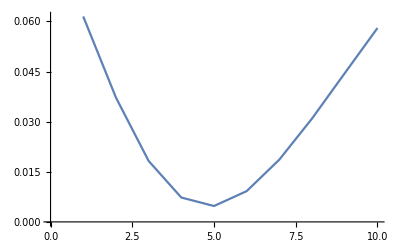

```mathematica
Table[deltae[0.5,-3.8,3.8],100]
```

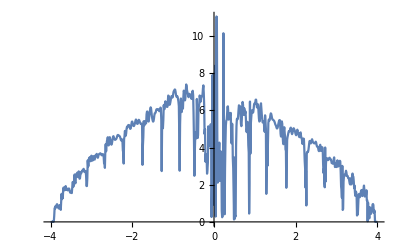

```mathematica
ListPlot[%72,Joined->True]
```

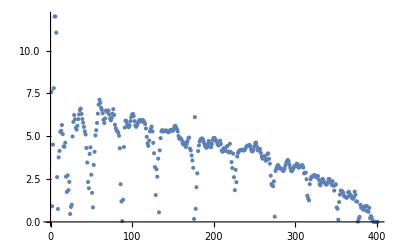

```mathematica
ListPlot[%67]
```

```mathematica
Tally[{imp,imp,imp,imp1,imp3,imp5,imp14,imp,imp,imp,imp2,imp,imp5,imp,imp4,imp,imp12,imp1,imp,imp,imp8,imp,imp,imp8,imp3,imp,imp,imp,imp,imp,imp4,imp,imp11,imp3,imp,imp,imp,imp,imp,imp13,imp7,imp,imp4,imp7,imp9,imp,imp2,imp14,imp5,imp,imp,imp,imp,imp13,imp6,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp14,imp,imp,imp,imp11,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp13,imp9,imp10,imp2,imp10,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp9}]
```

{{imp,58},{imp1,3},{imp3,3},{imp5,3},{imp14,3},{imp2,3},{imp4,3},{imp12,3},{imp8,3},{imp11,3},{imp13,3},{imp7,3},{imp9,3},{imp6,3},{imp10,3}}